# Function

## Temp

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)
```

(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]]//FullSimplify;
ans=Solve[den/CoefficientList[den,v][[3]]==0,v]//FullSimplify;
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)

]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])//Simplify
]
```

## 2Level

```mathematica
Lev2DoppTest[T_,P_,diam_] :=
Module[{d,Δ,Nat,γ21,Γ12,d21,ℏ,e0,c,wcn,wc,u,omegac,f,A,α1,α2,Zα,β1,β2,Zβ,f2,A2,omegac2,d21u,wupper},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
γ21=2*Pi*5.750056 10^6/2;
Γ12=2*Pi*5.750056 10^6;
d21=Sqrt[5/27]*2.537717 10^-29;
d21u=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac=(1/ℏ Sqrt[1/(e0 c)]*d21*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d21u*Sqrt[P/(Pi*(diam/2)^2)]); 
wupper=2Pi(-0.361*10^9);
Zα=c/wc (ⅈ γ21+Δ-wupper);
Zβ=c/wc (ⅈ γ21+Δ-wupper);
α1=(-(√(-c^2 omegac^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c Δ)/wc);
α2=((√(-c^2 omegac^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c Δ)/wc);
β1=(-(√(-c^2 omegac2^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c (Δ-wupper))/wc); 
β2=((√(-c^2 omegac2^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c (Δ-wupper))/wc); 
A= (c d21^2 Nat Γ12)/(e0 √π u ℏ)/(wc Γ12);
A2= (c d21u^2 Nat Γ12)/(e0 √π u ℏ)/(wc Γ12); 
f=A 1/(α1-α2)(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[√(1/u^2) α1]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[√(1/u^2) α2]-Log[-1/α2]-Log[α2]));
f2=A2 1/(β1-β2)(-ⅇ^(-β1^2/u^2) (Zβ+β1) (π Erfi[√(1/u^2) β1]-Log[-1/β1]-Log[β1])+ⅇ^(-β2^2/u^2) (Zβ+β2) (π Erfi[√(1/u^2) β2]-Log[-1/β2]-Log[β2]));
Transpose[{ d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[f+f2]]
}]

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-0.8,0.5,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-0.8,0.5,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=Lev4DoppTestsc[T,P,diam,gam,delt,ab]=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-3,3,0.003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-3,3,0.003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

# Plot

## Increase Power Δ δ

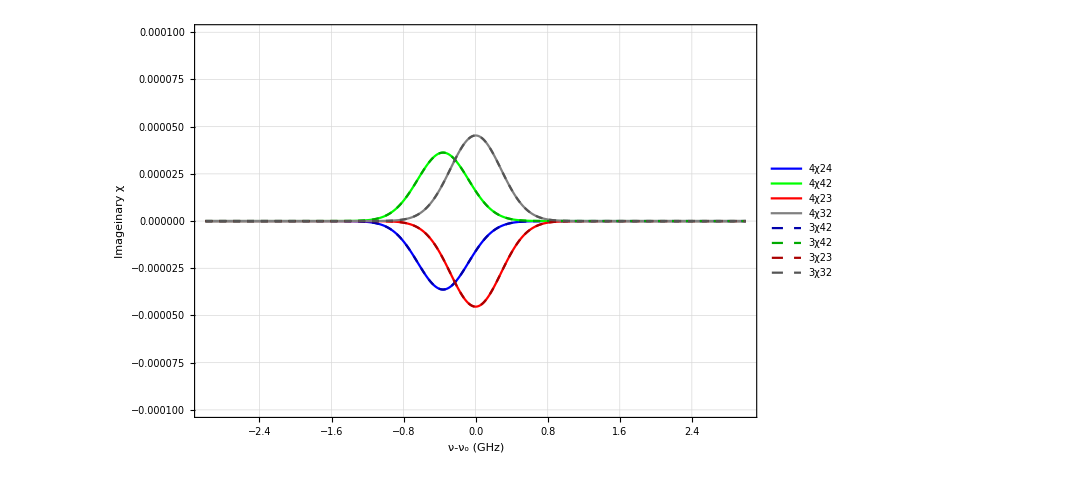

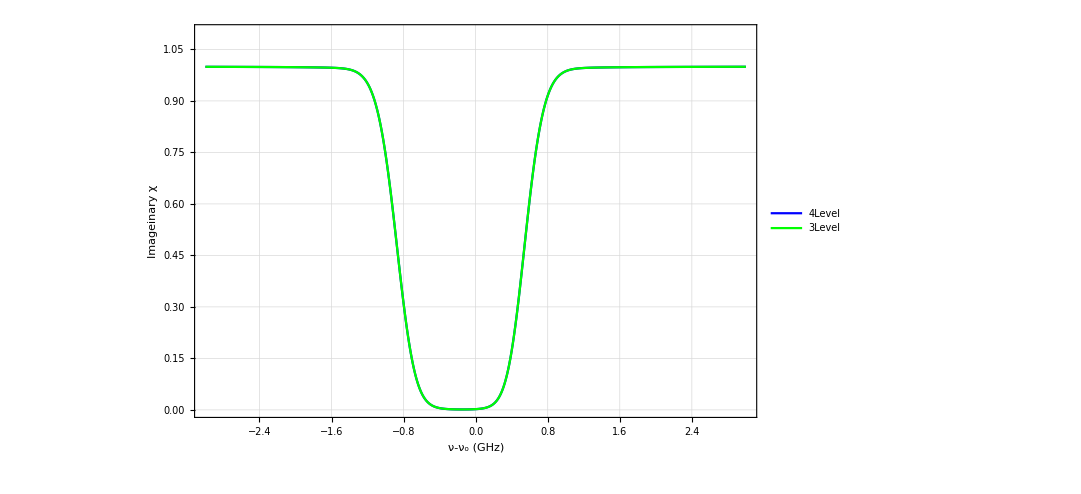

```mathematica
Clear[p,t,g,dc];
t=65(*C*);
p=0(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

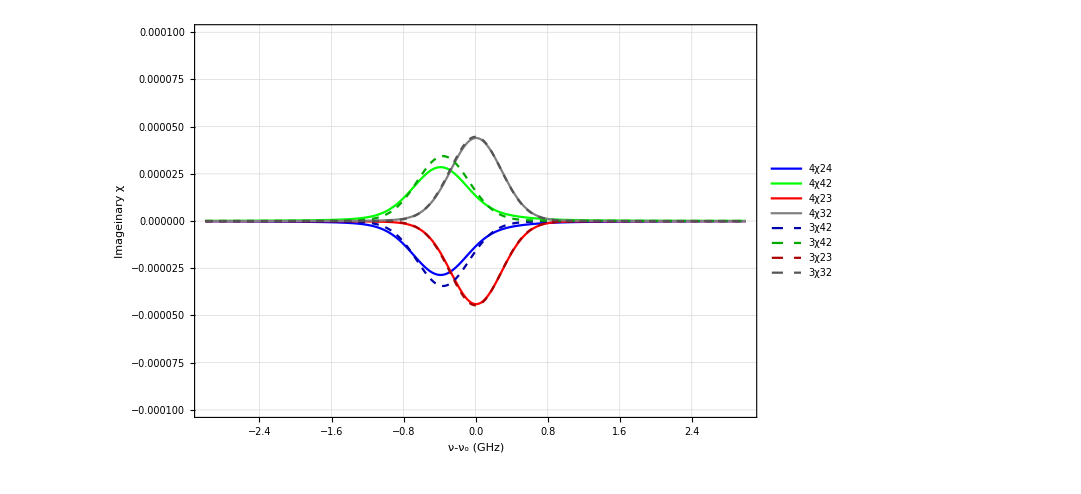

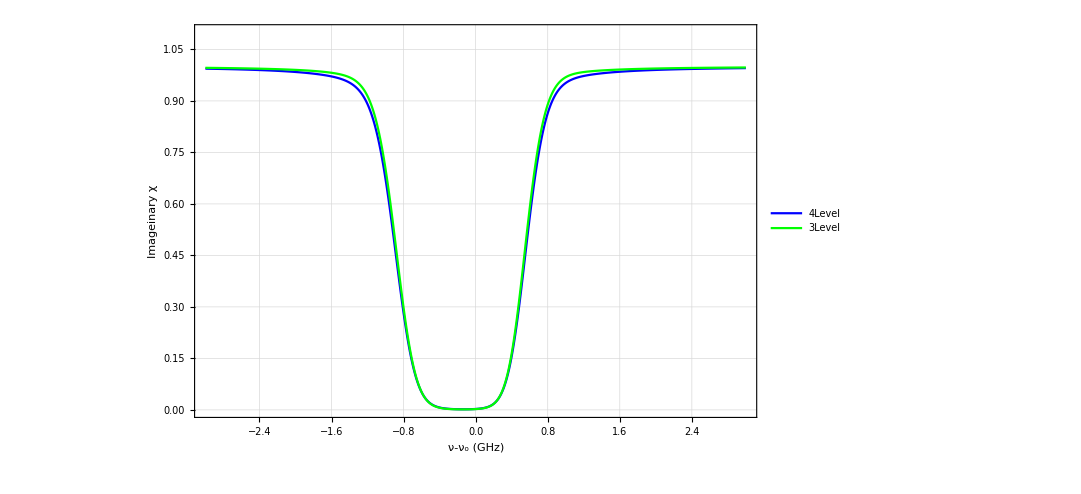

```mathematica
Clear[p,t,g,dc];
t=65(*C*);
p=5(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

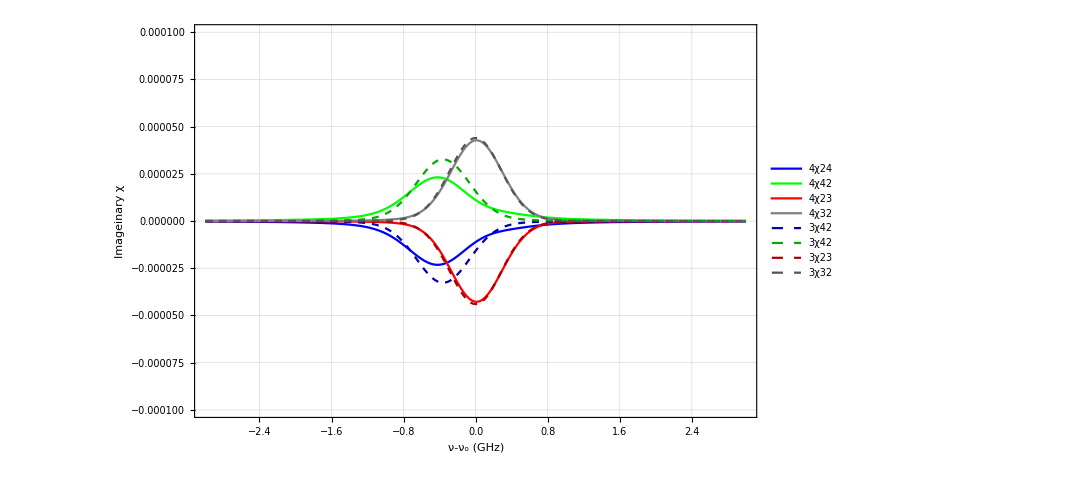

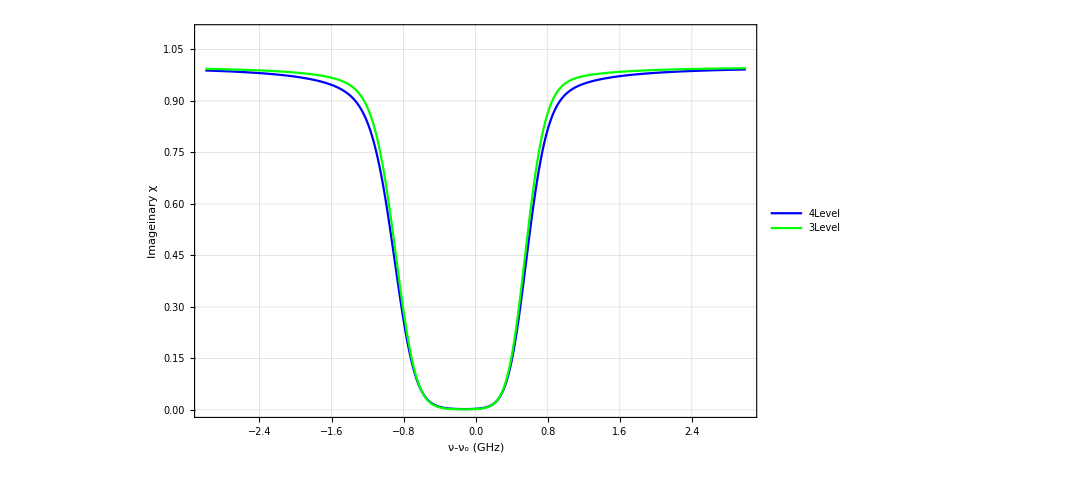

```mathematica
t=65(*C*);
p=10(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

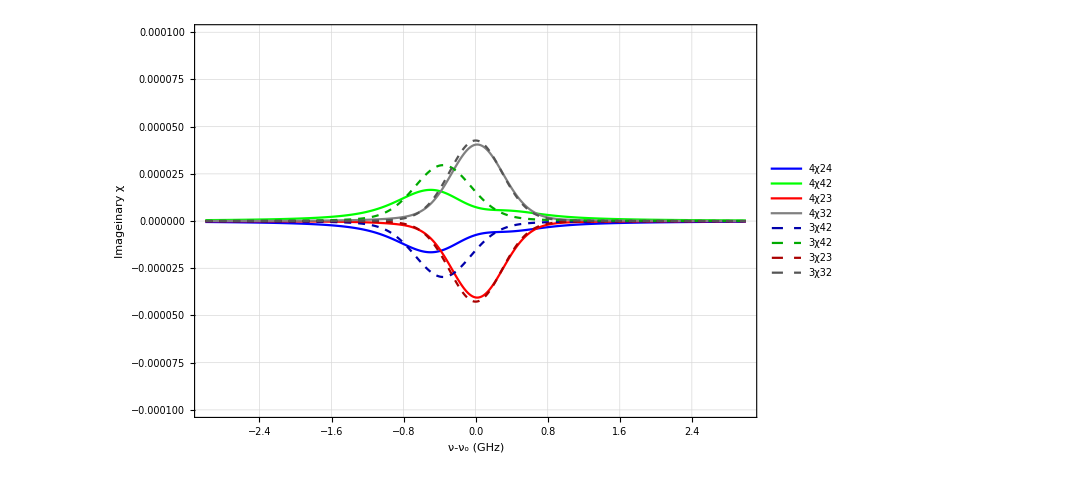

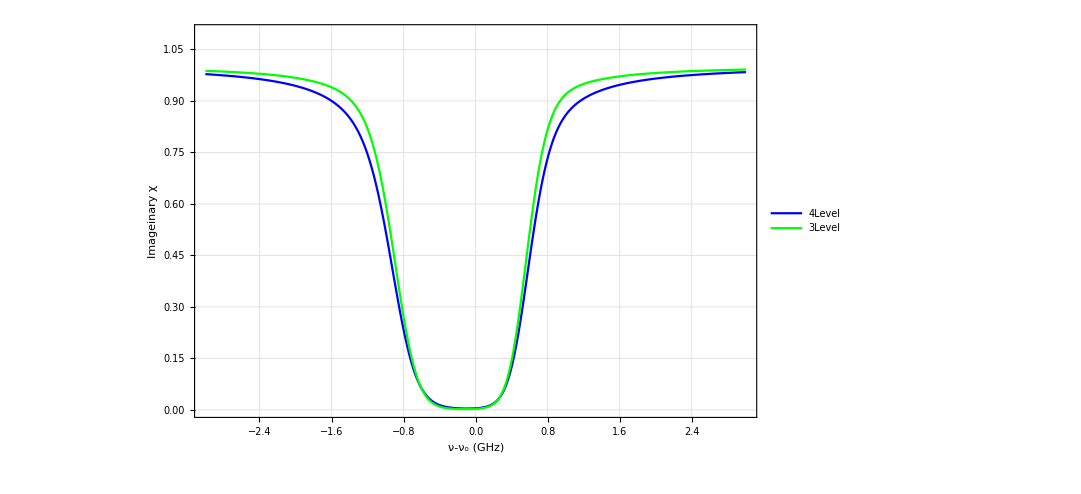

```mathematica
t=65(*C*);
p=20(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

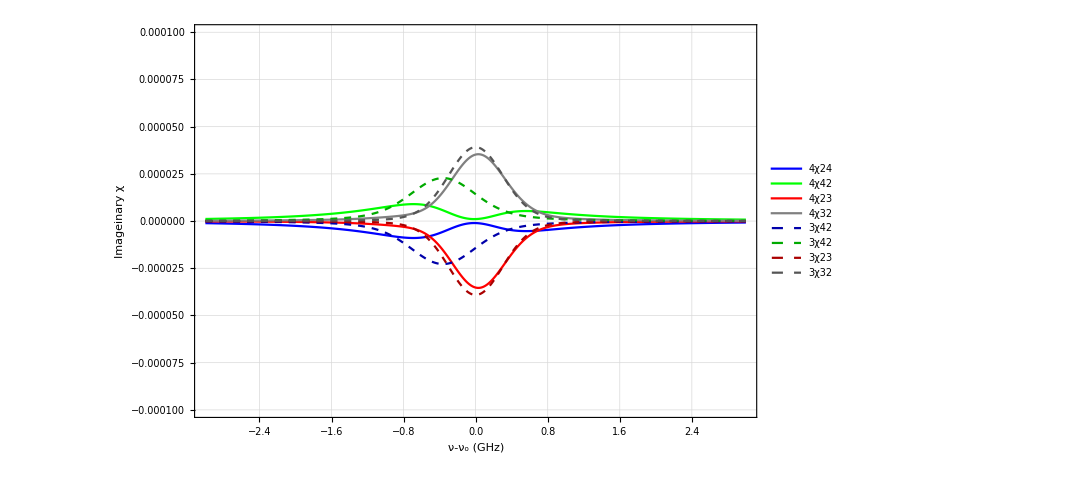

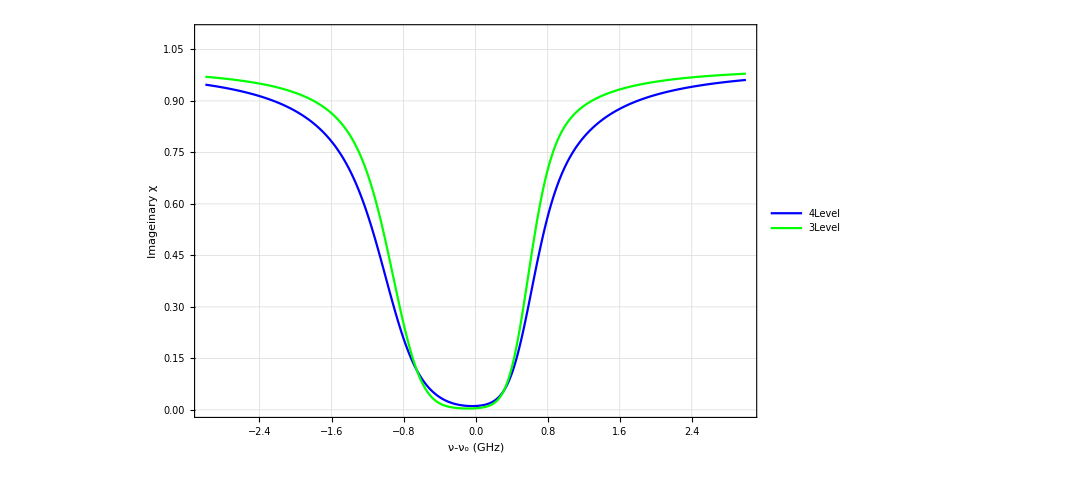

```mathematica
t=65(*C*);
p=50(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

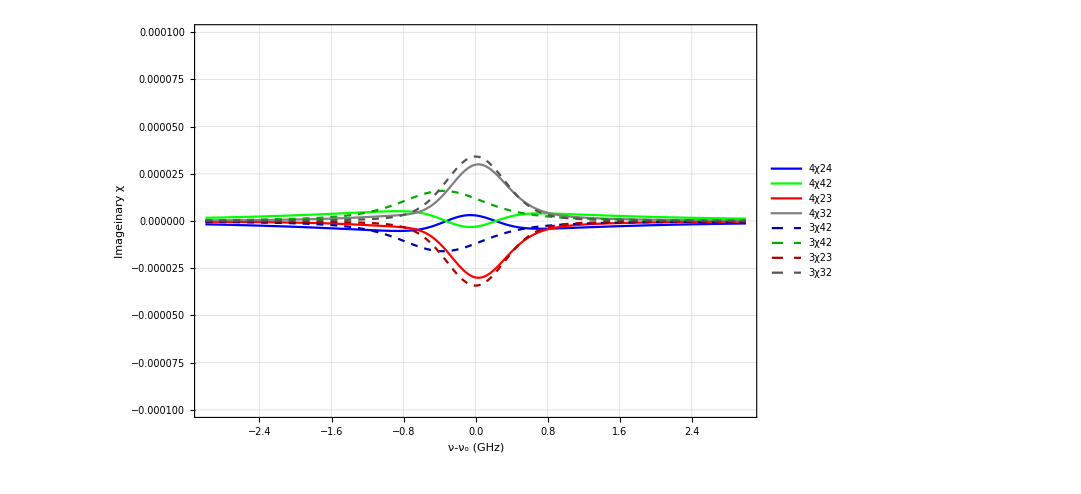

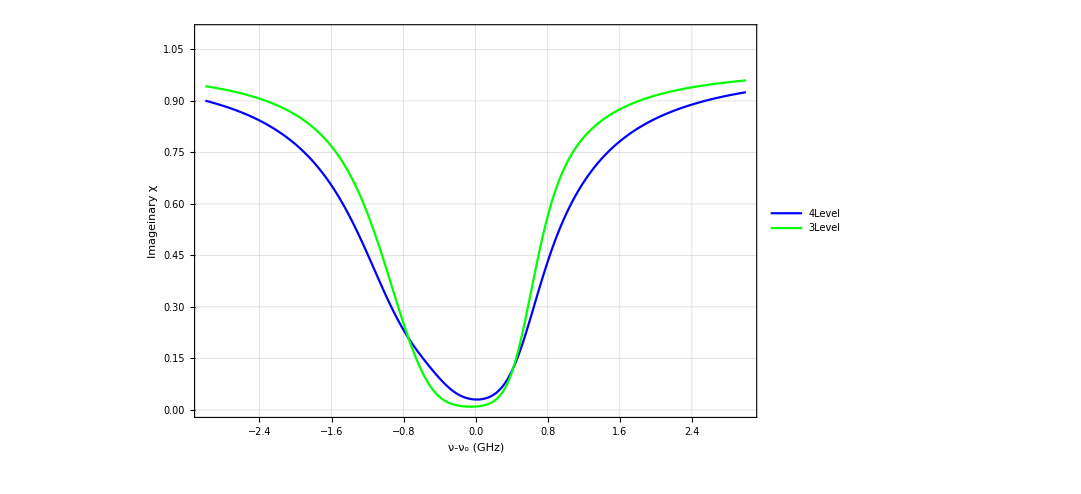

```mathematica
t=65(*C*);
p=100(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

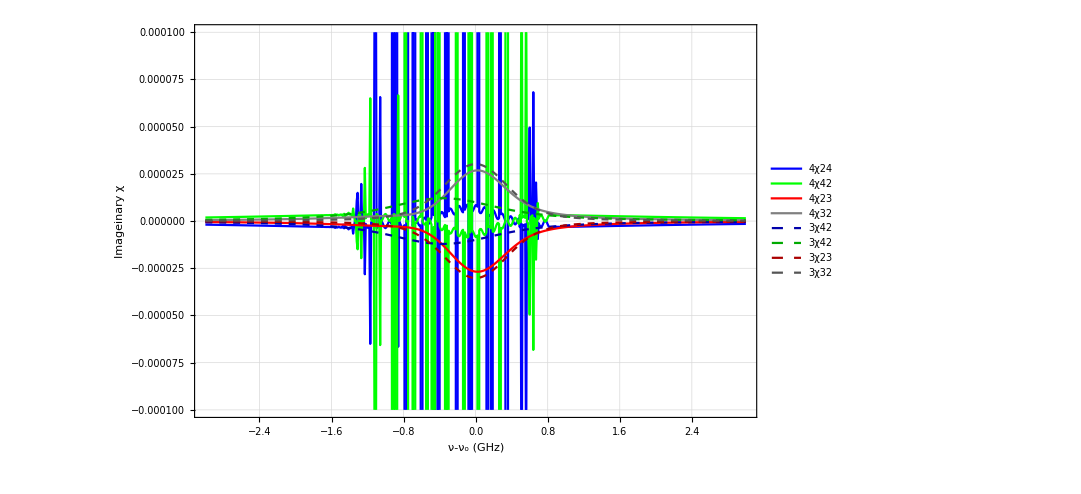

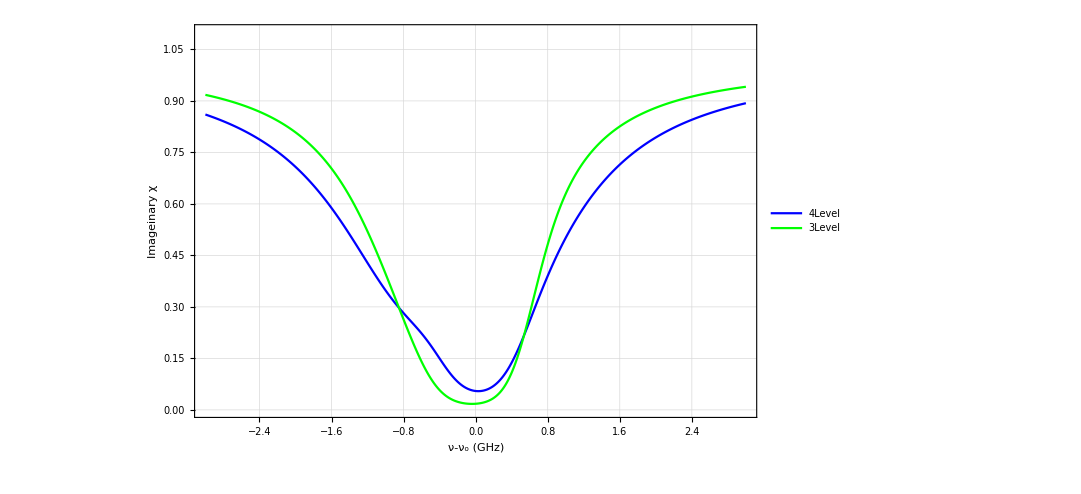

```mathematica
t=65(*C*);
p=150(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

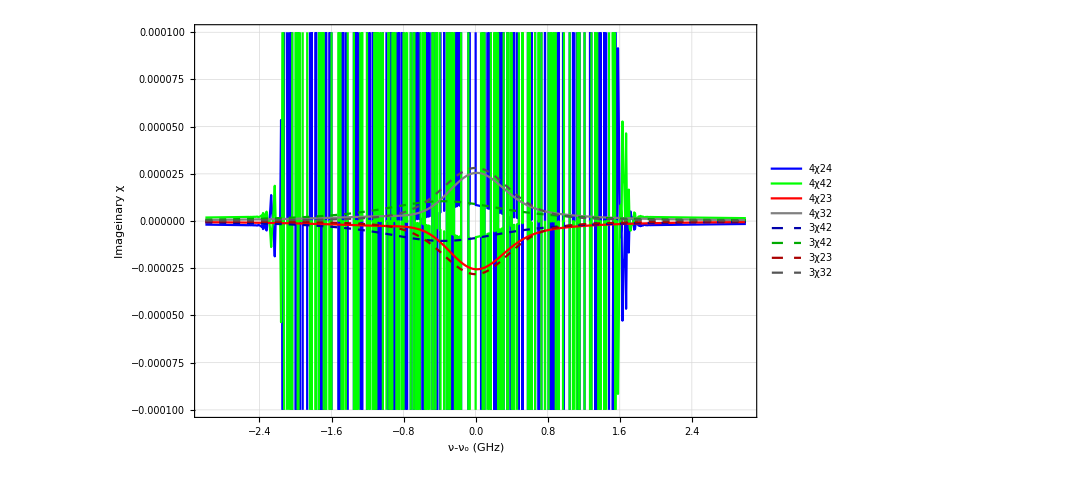

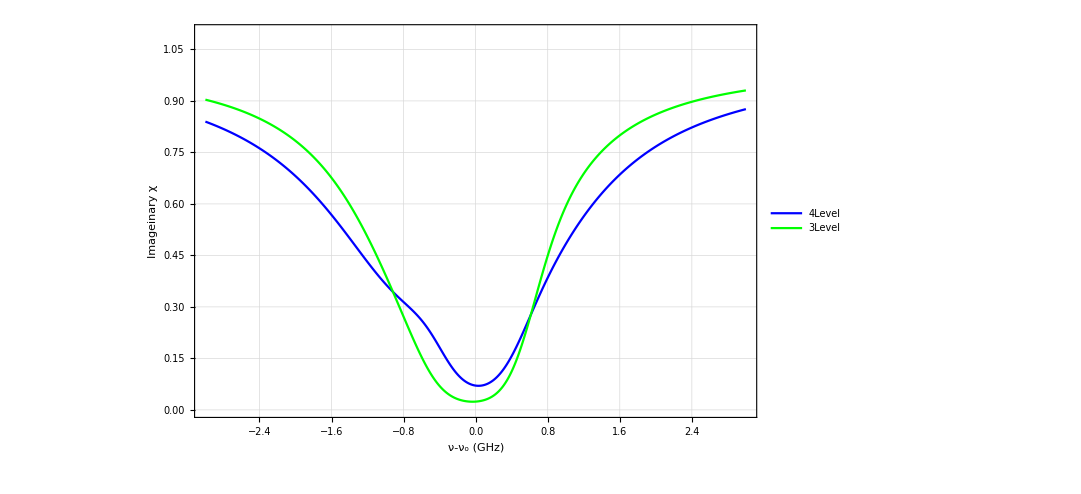

```mathematica
t=65(*C*);
p=180(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

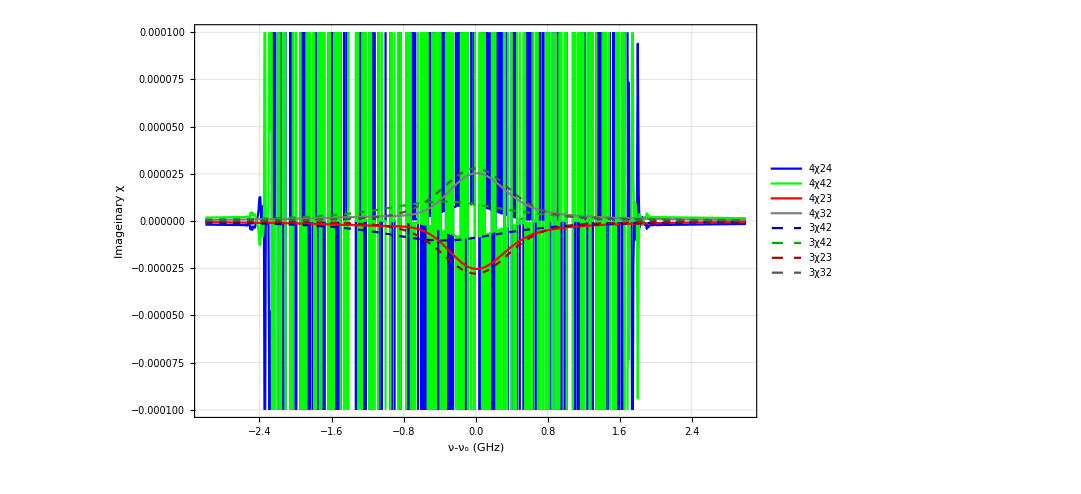

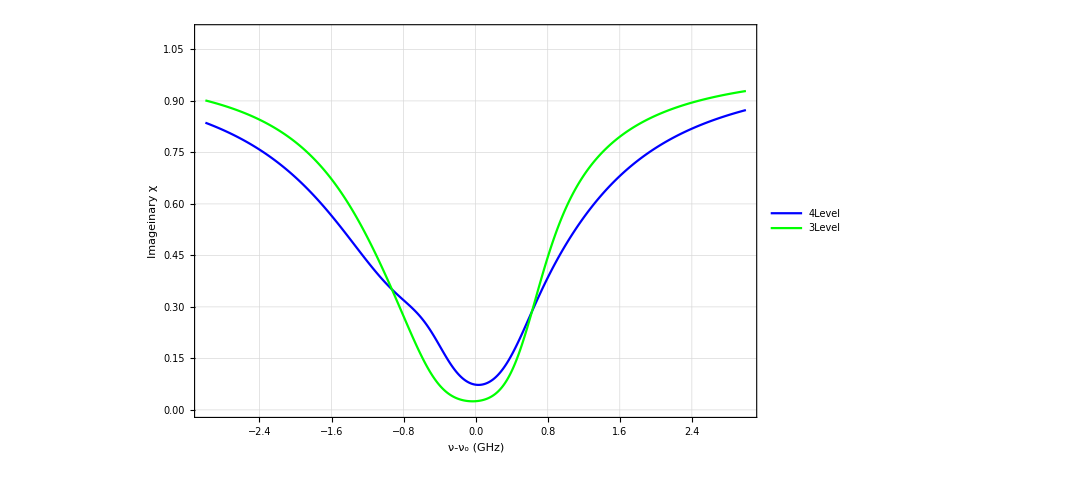

```mathematica
t=65(*C*);
p=185(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

## Change Detuning Δ δ

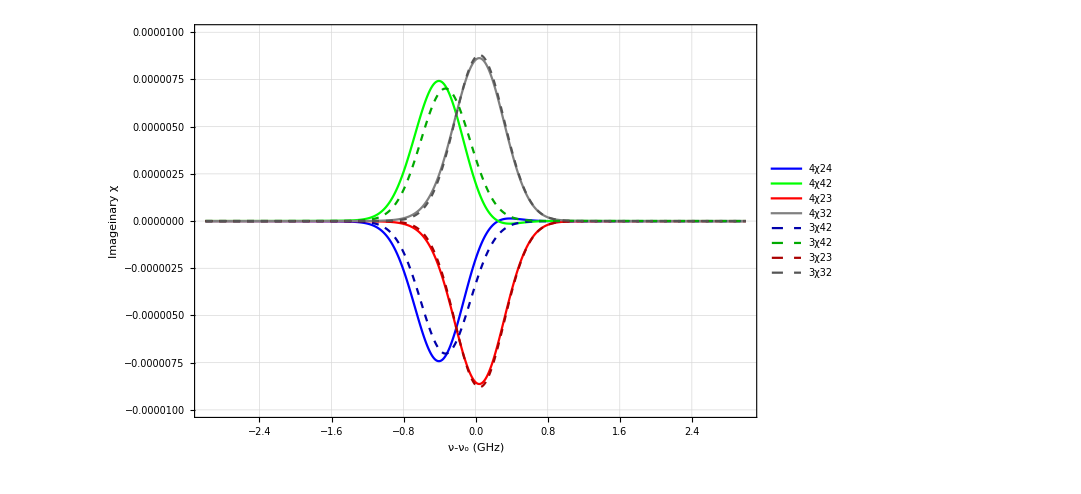

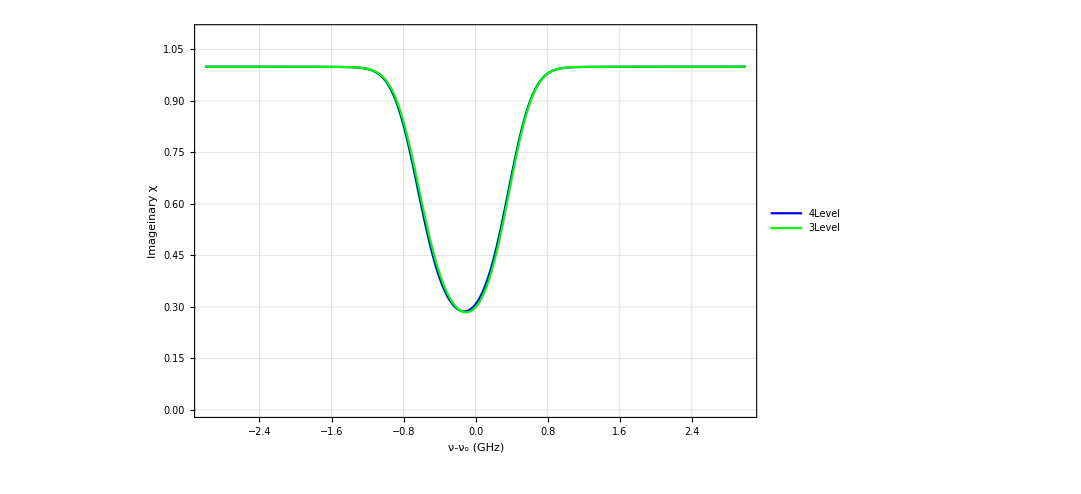

```mathematica
t=45(*C*);
p=100(*mW*);
g=-50(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

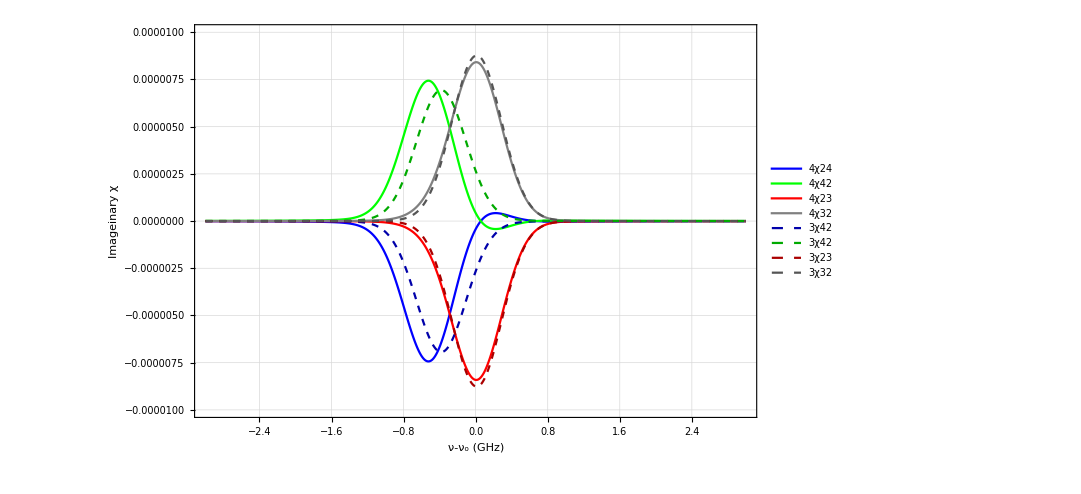

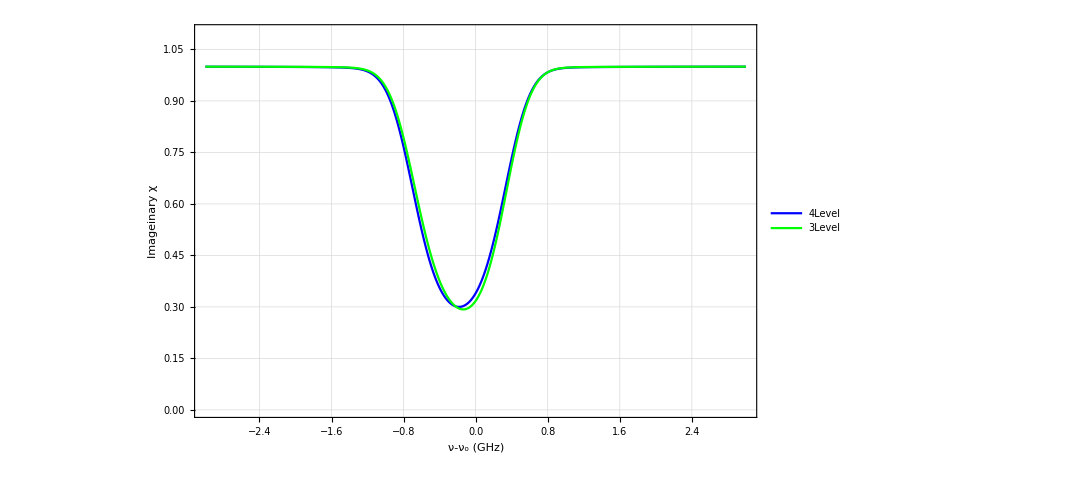

```mathematica
t=45(*C*);
p=100(*mW*);
g=-25(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

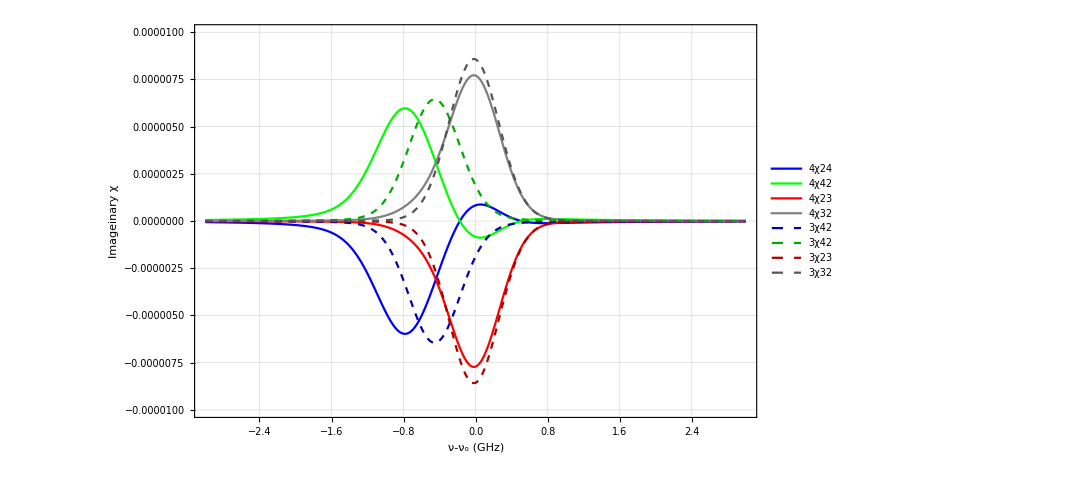

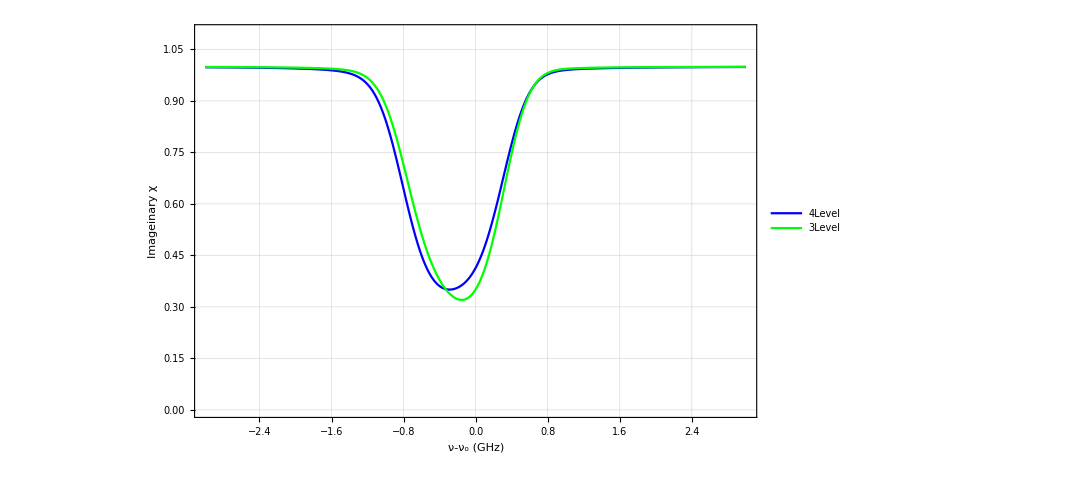

```mathematica
t=45(*C*);
p=100(*mW*);
g=-10(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

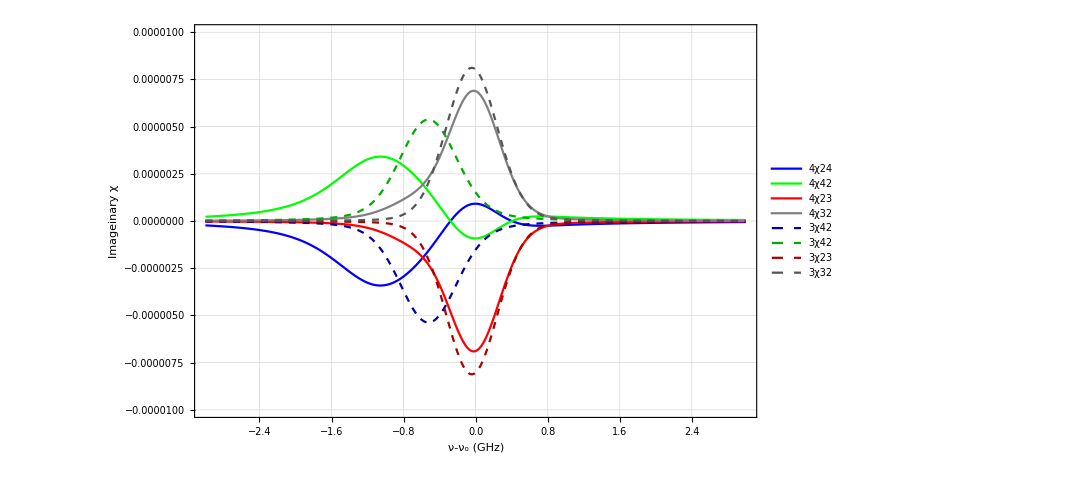

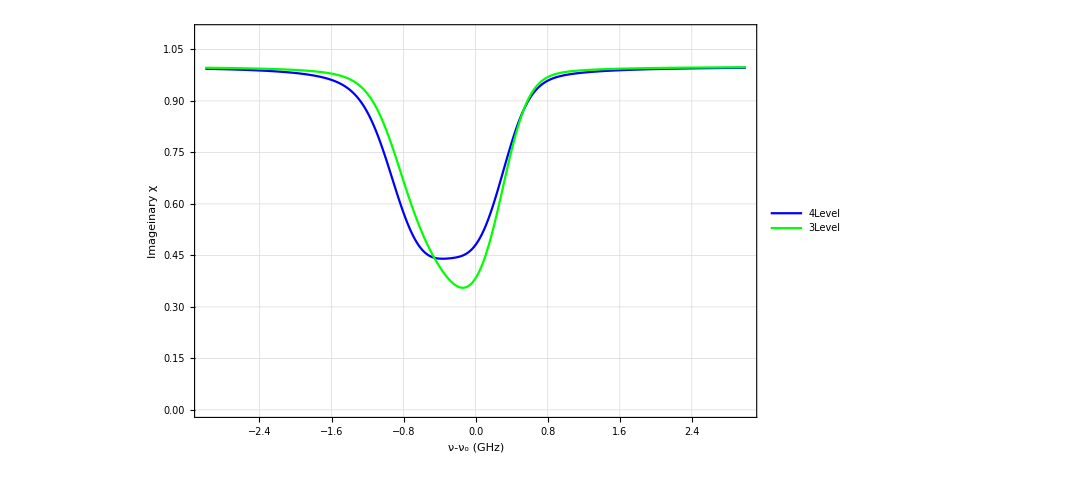

```mathematica
t=45(*C*);
p=100(*mW*);
g=-5(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

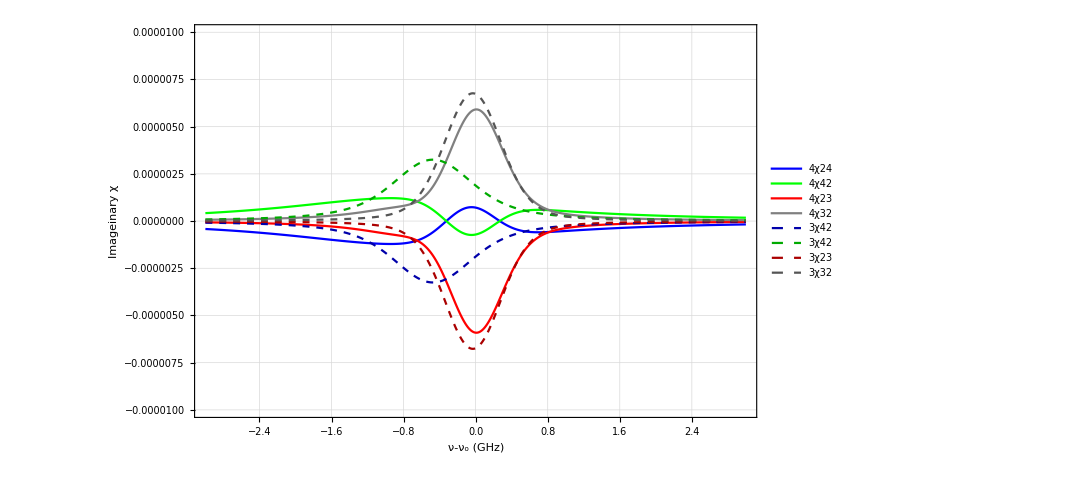

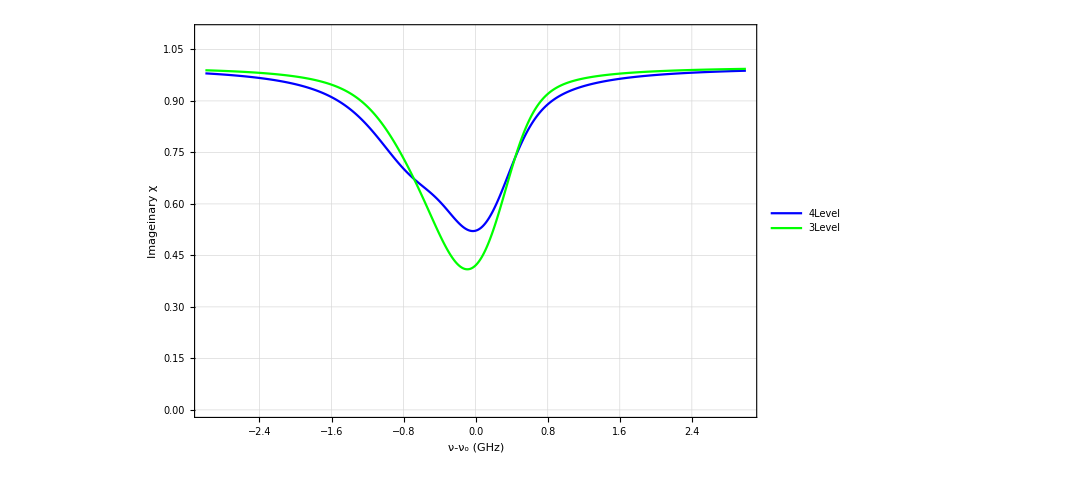

```mathematica
t=45(*C*);
p=100(*mW*);
g=-1(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

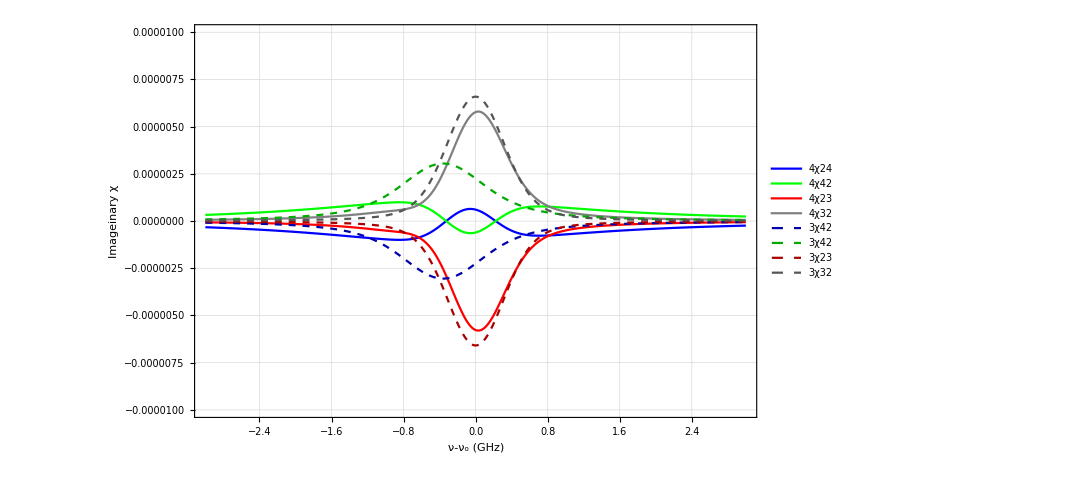

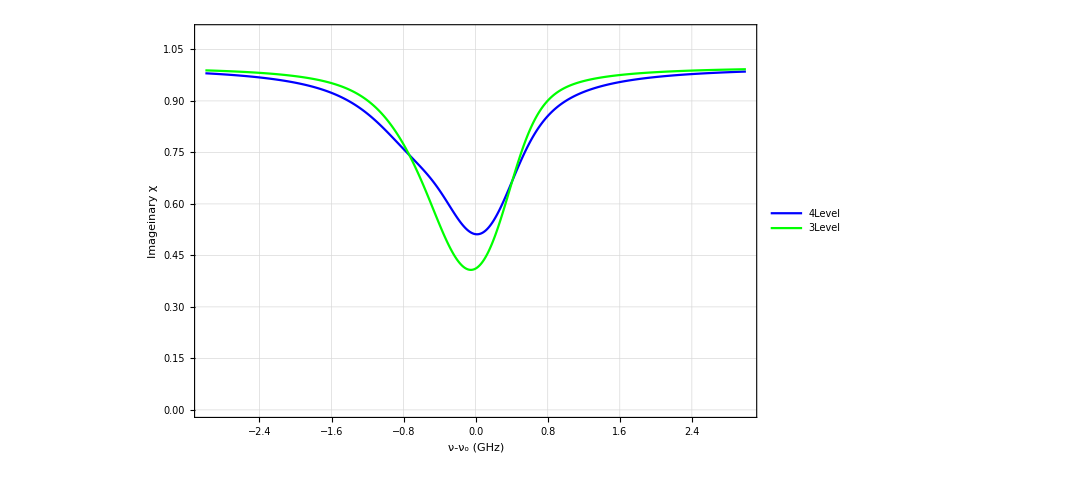

```mathematica
t=45(*C*);
p=100(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

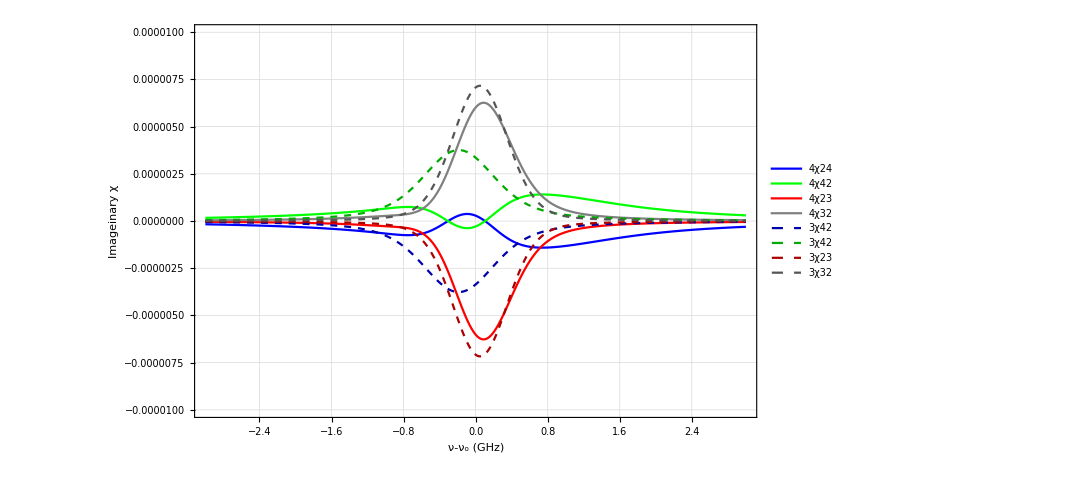

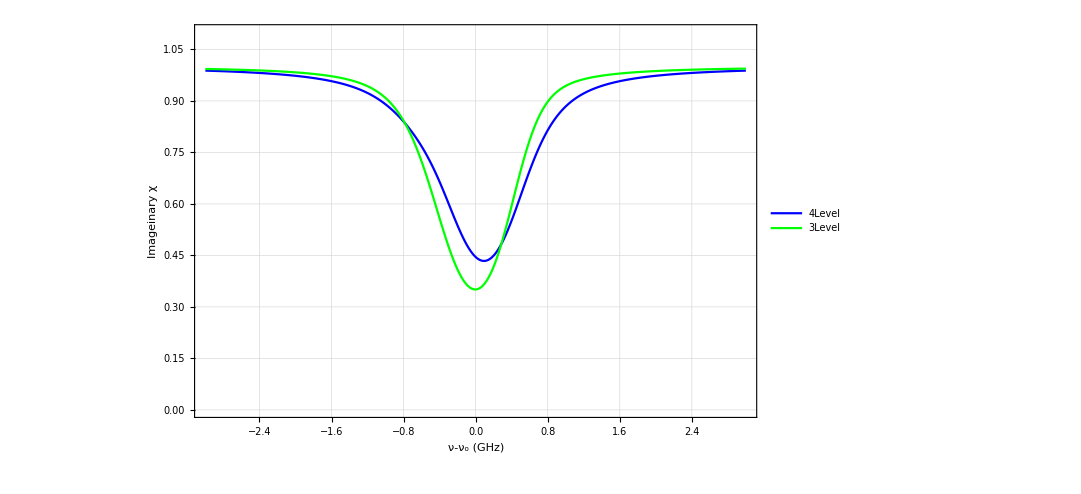

```mathematica
t=45(*C*);
p=100(*mW*);
g=2(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

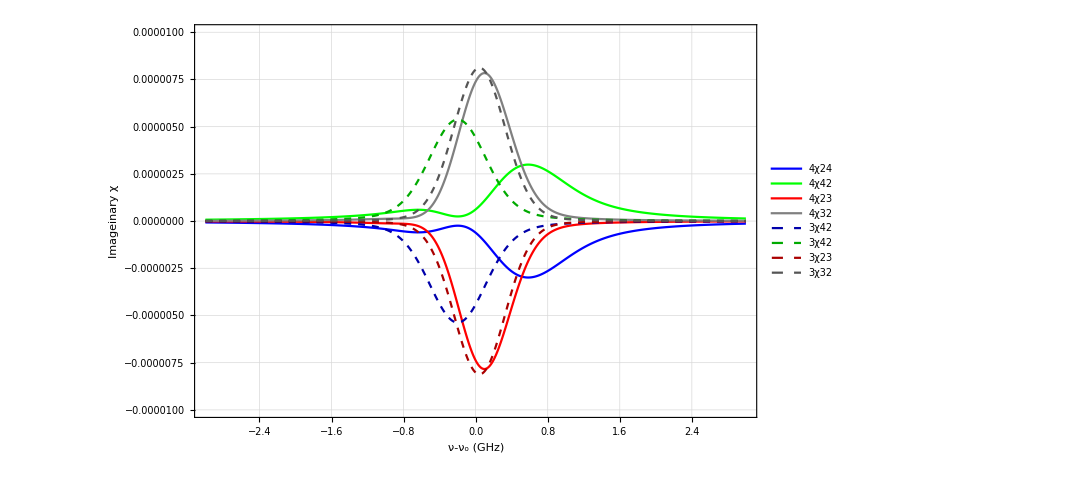

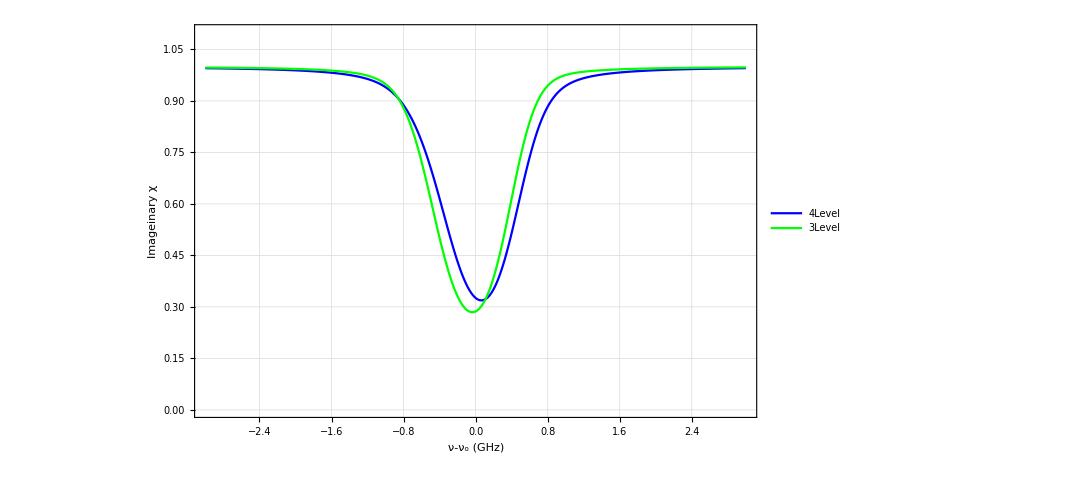

```mathematica
t=45(*C*);
p=100(*mW*);
g=5(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

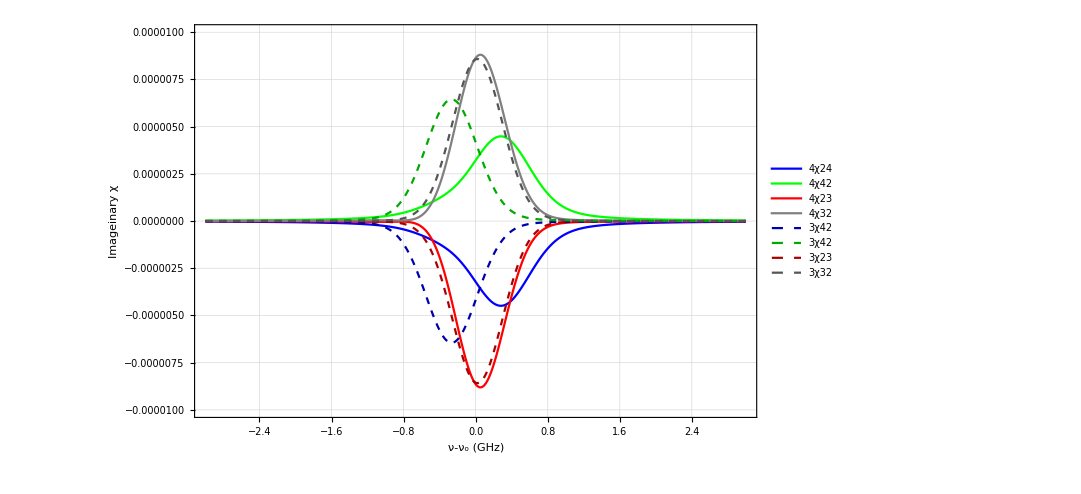

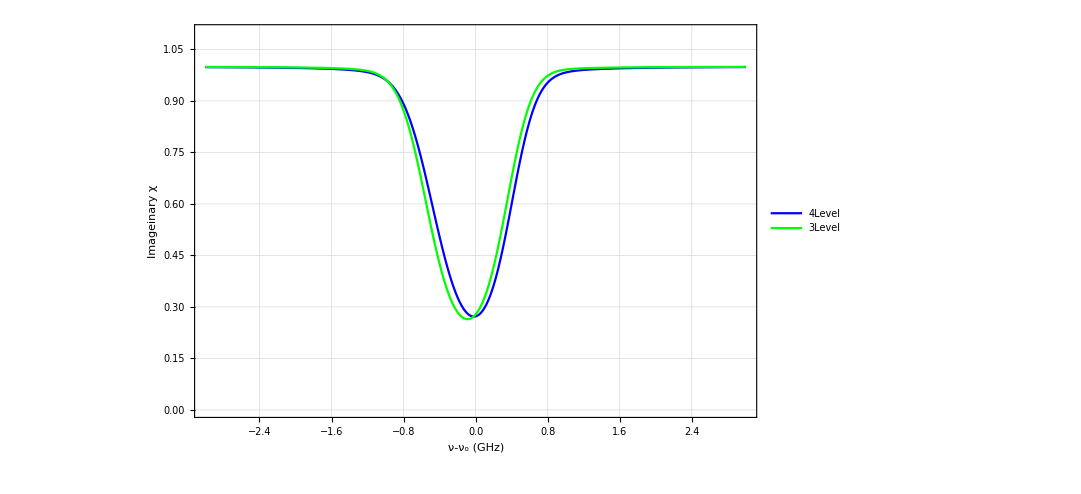

```mathematica
t=45(*C*);
p=100(*mW*);
g=10(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

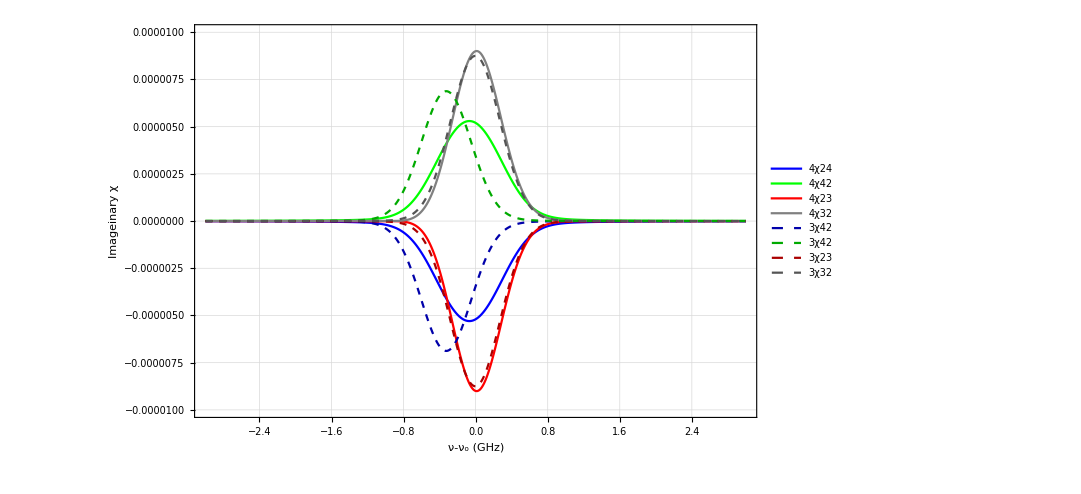

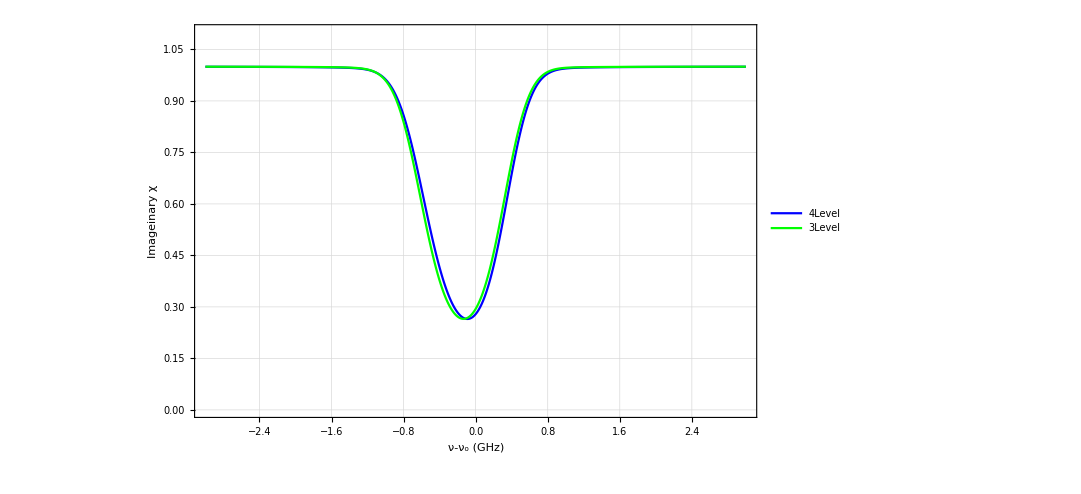

```mathematica
t=45(*C*);
p=100(*mW*);
g=20(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

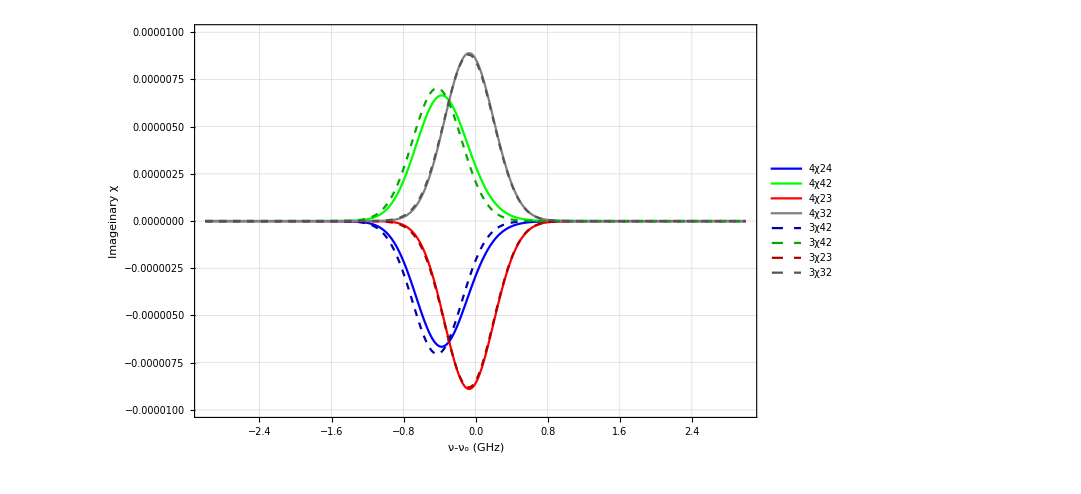

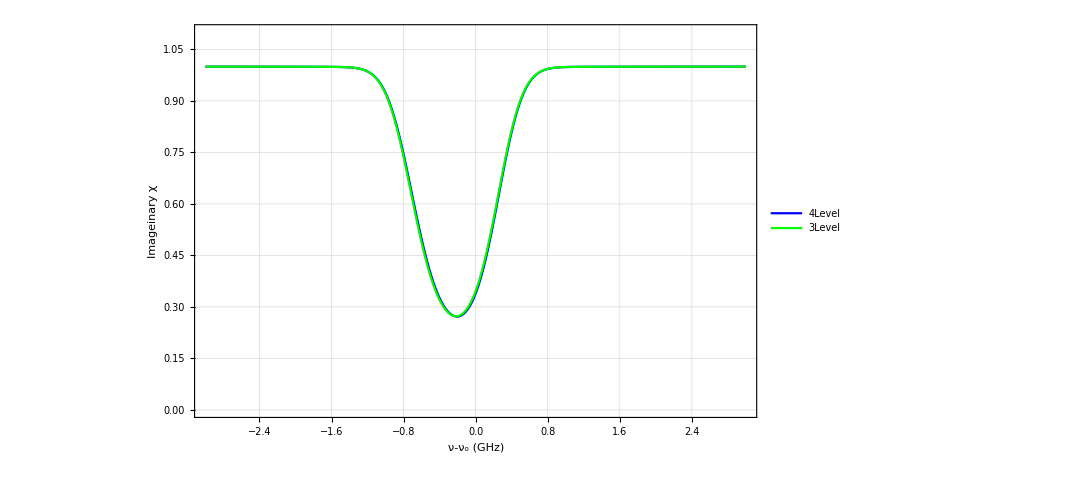

```mathematica
t=45(*C*);
p=100(*mW*);
g=80(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

## Increase Power Δ1 Δ2

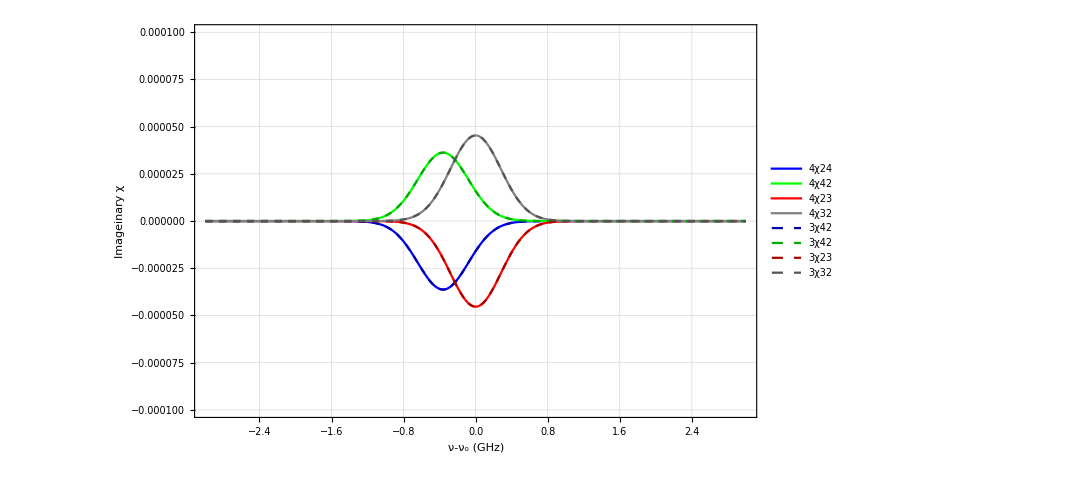

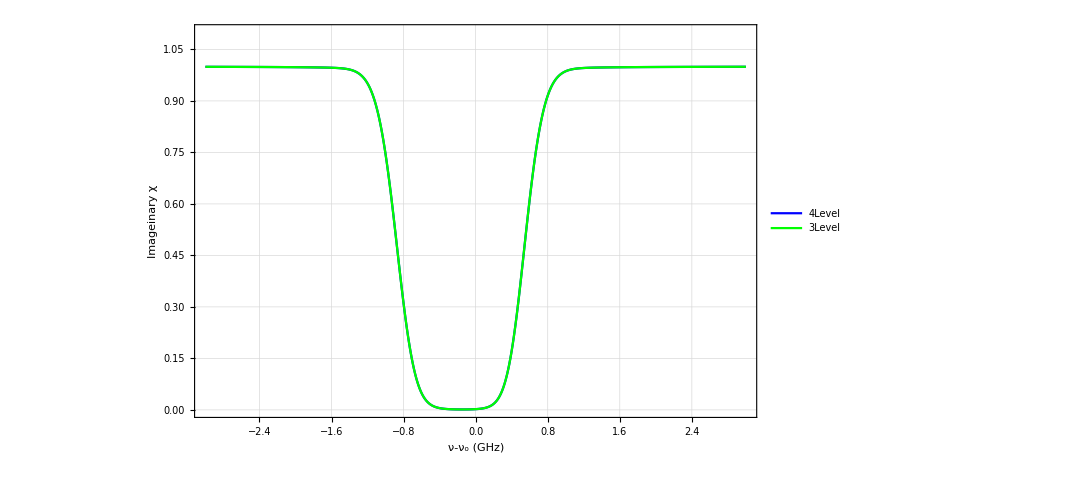

```mathematica
Clear[p,t,g,dc];
t=65(*C*);
p=0(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

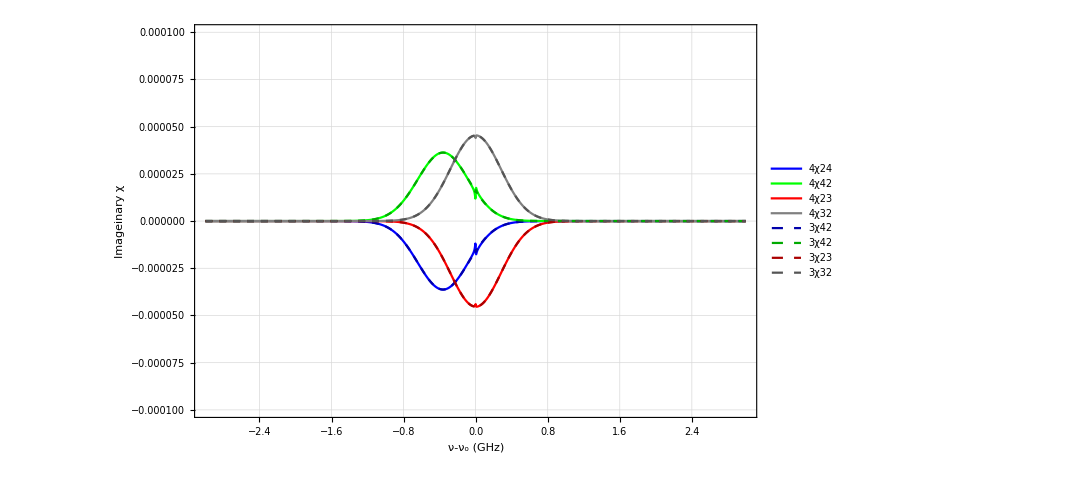

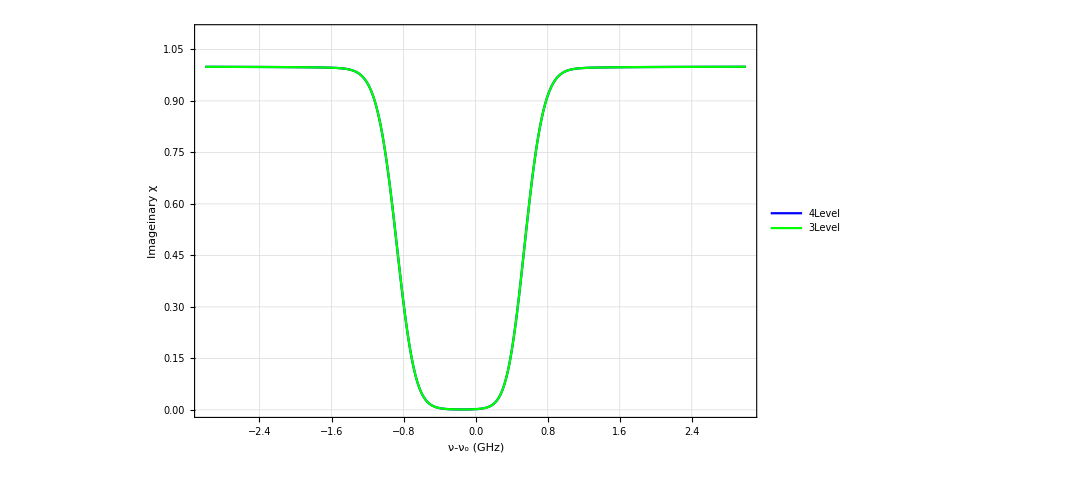

```mathematica
Clear[p,t,g,dc];
t=65(*C*);
p=5(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

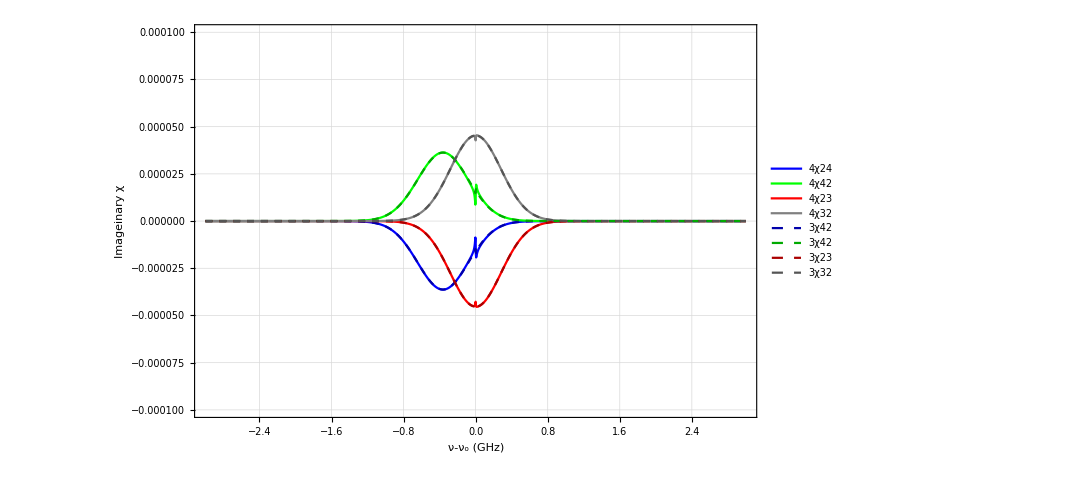

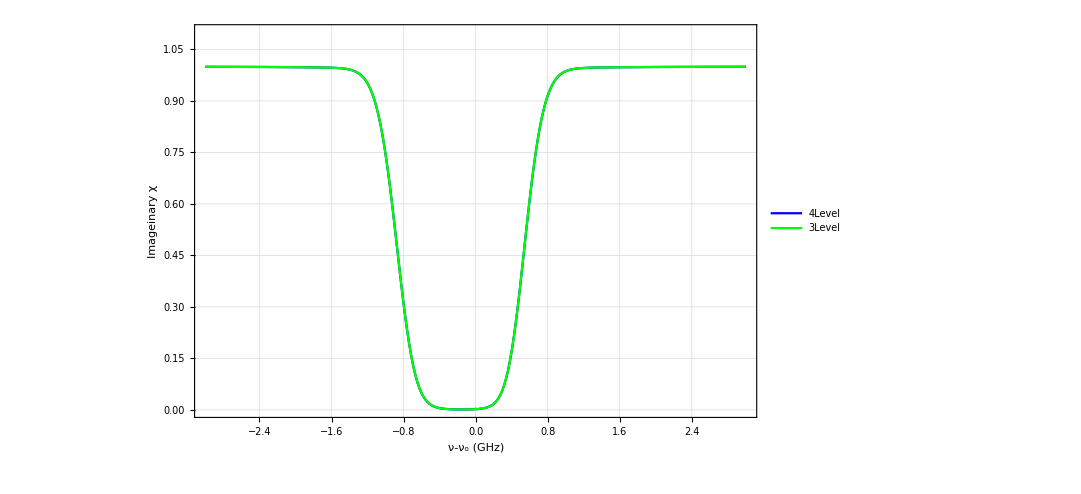

```mathematica
t=65(*C*);
p=10(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

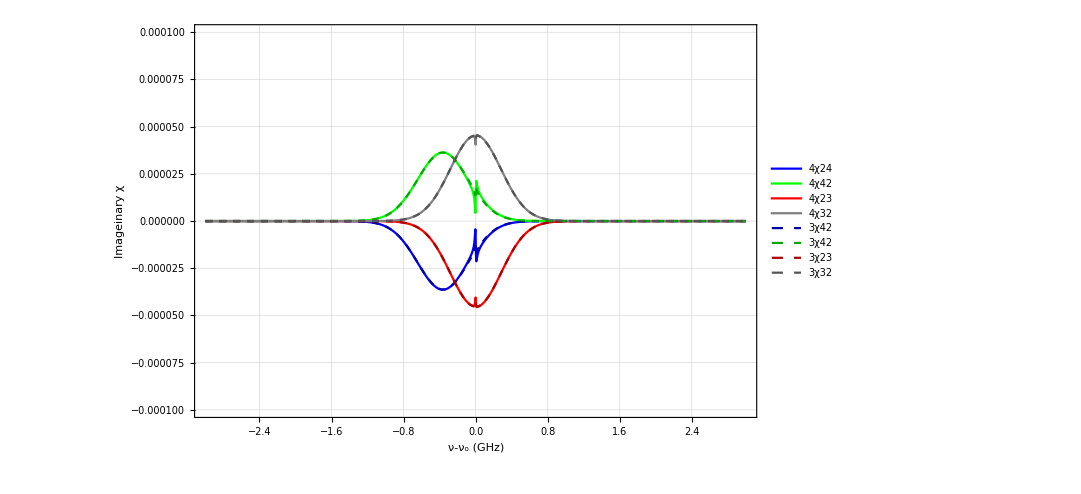

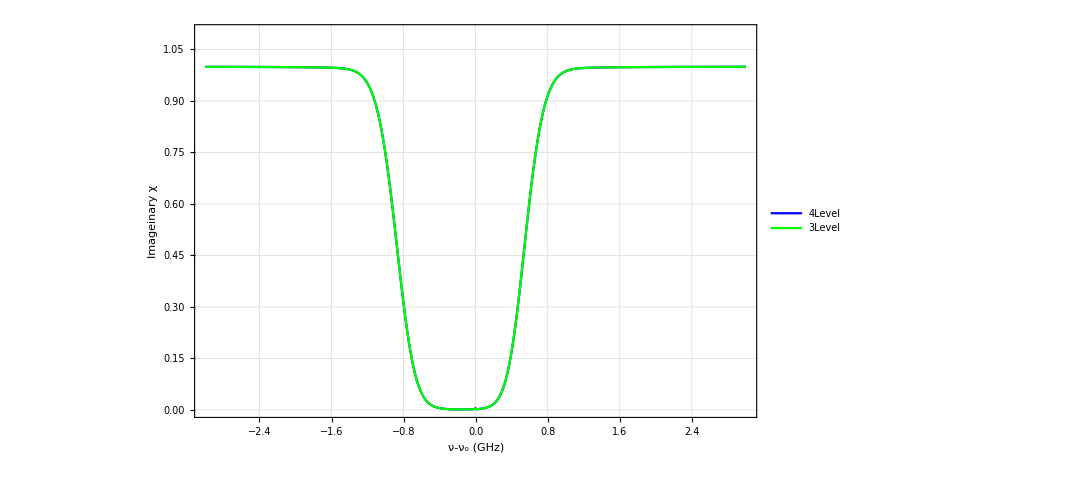

```mathematica
t=65(*C*);
p=20(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

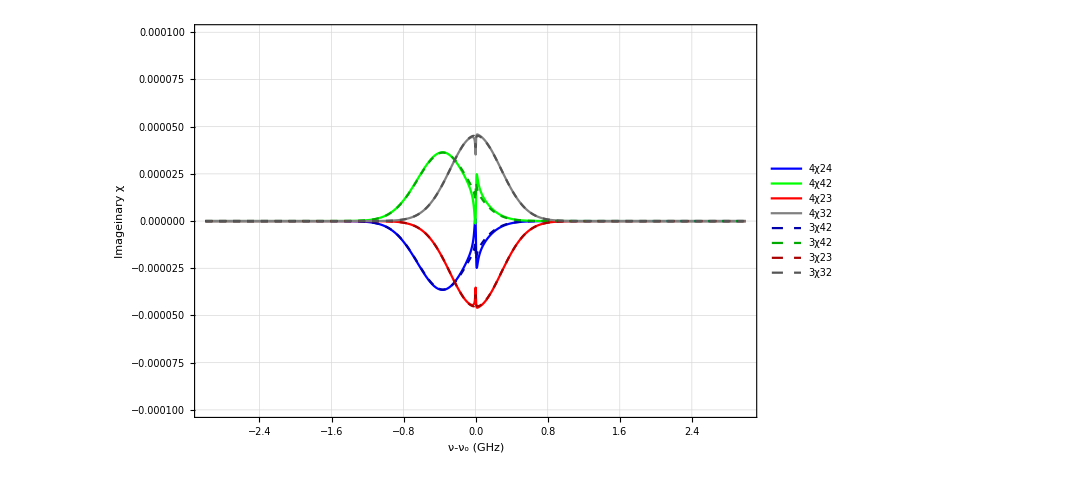

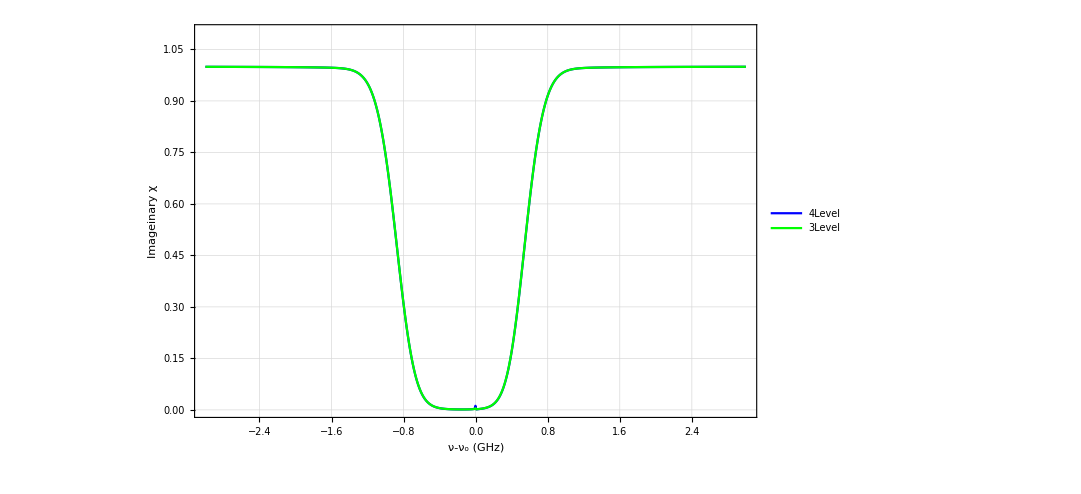

```mathematica
t=65(*C*);
p=50(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

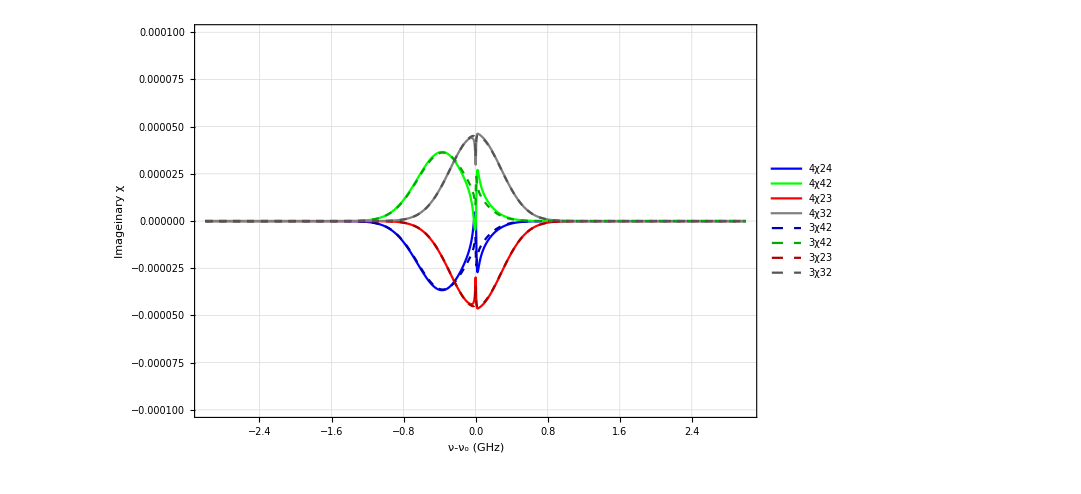

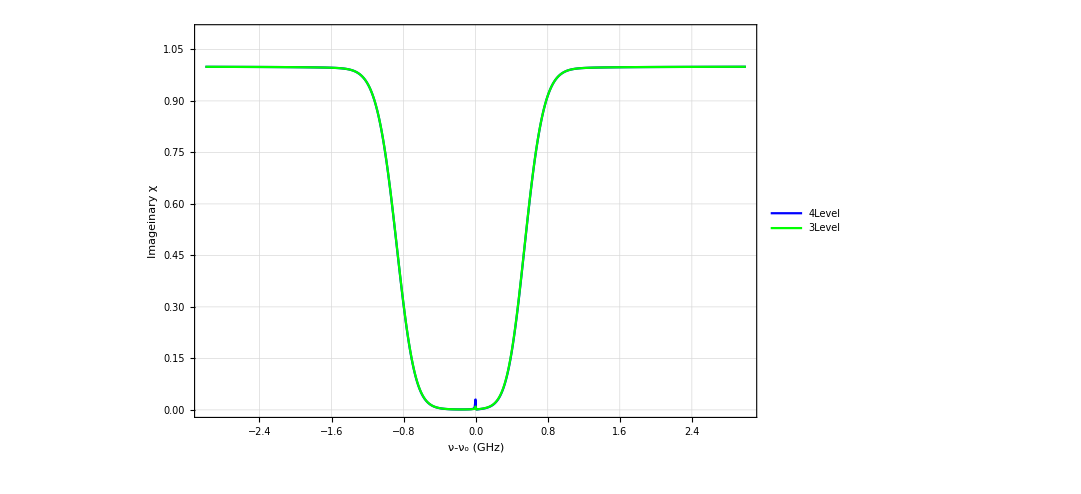

```mathematica
t=65(*C*);
p=100(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

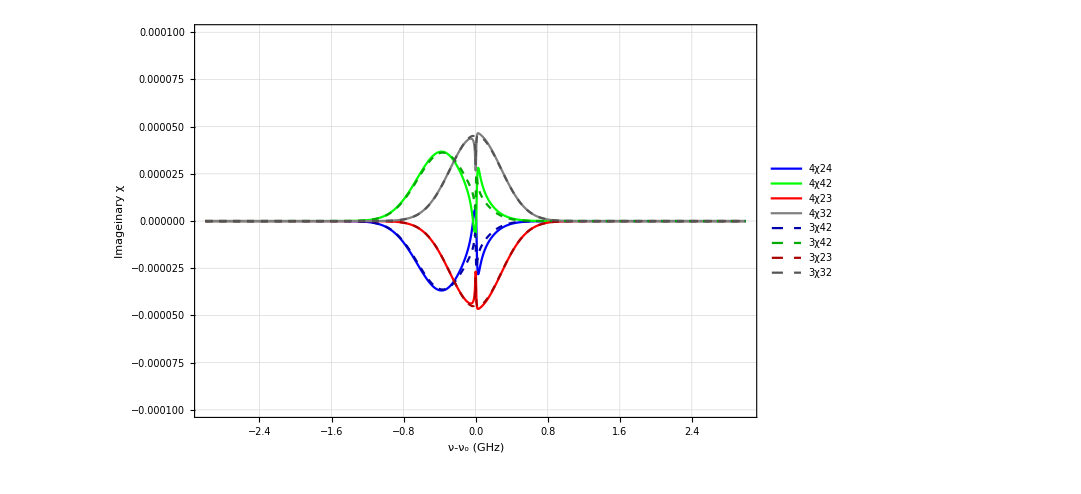

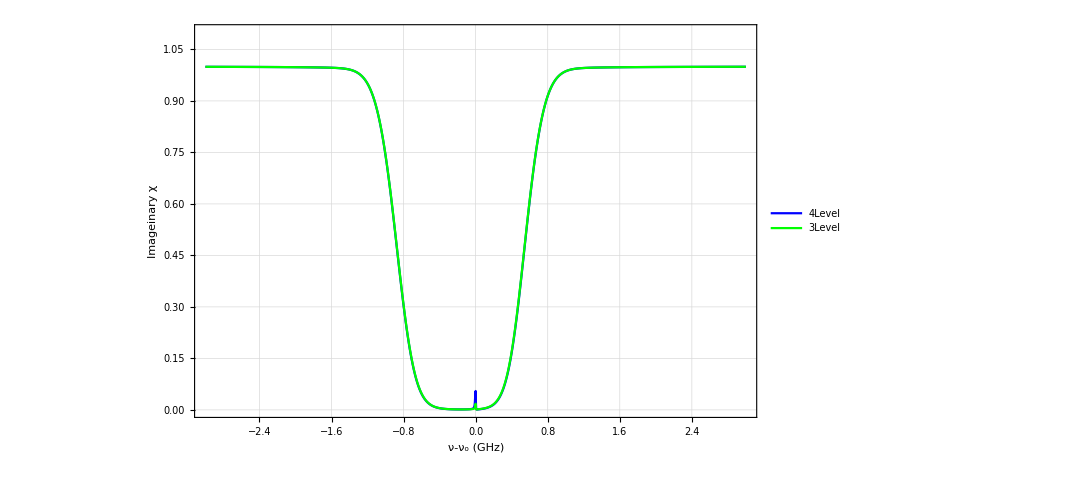

```mathematica
t=65(*C*);
p=150(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

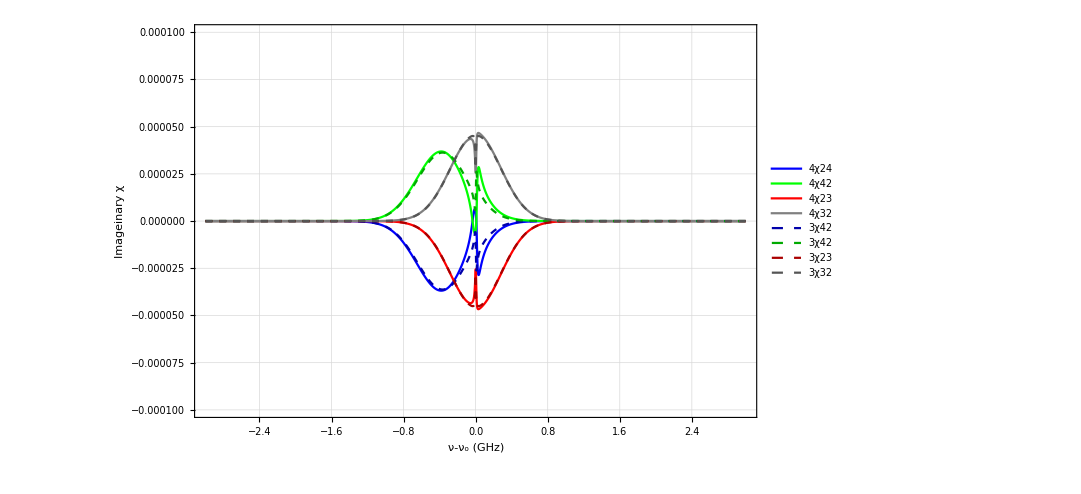

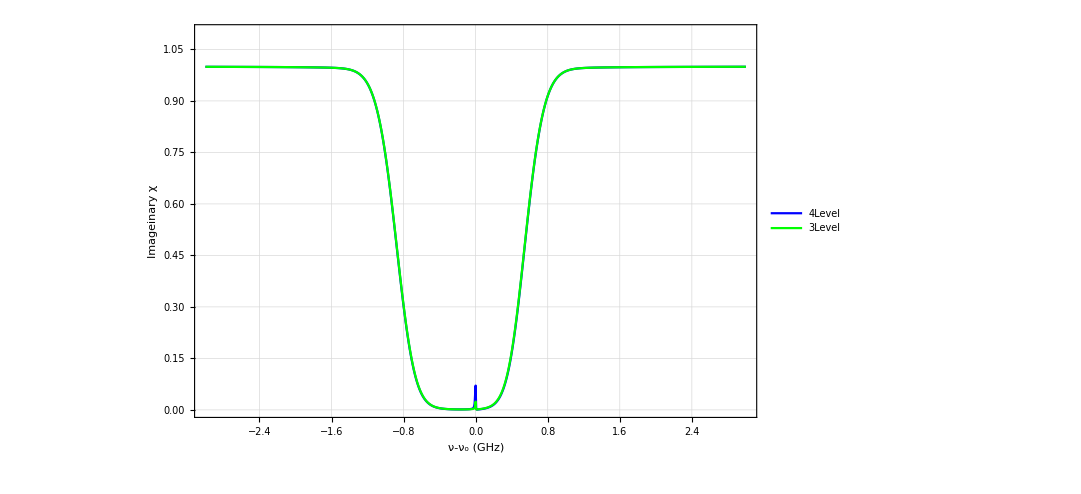

```mathematica
t=65(*C*);
p=180(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

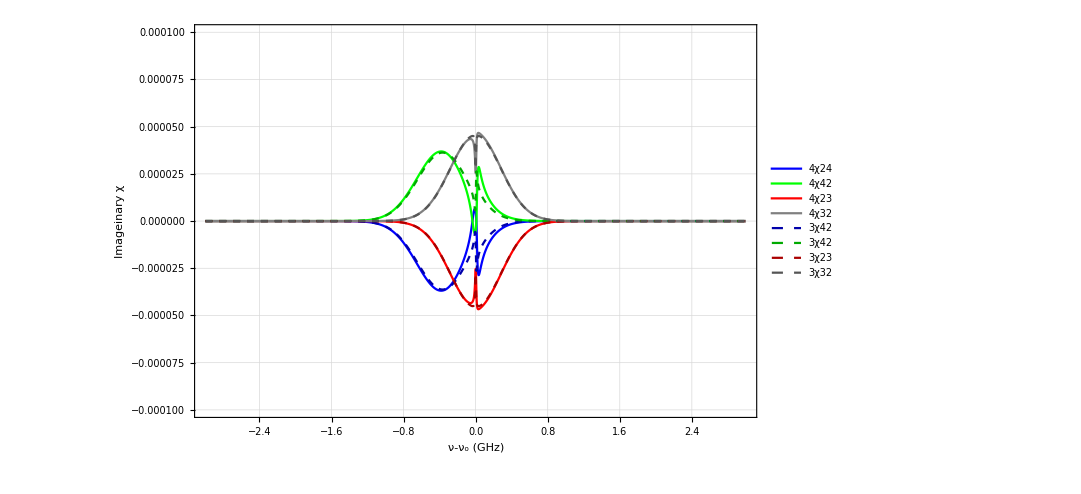

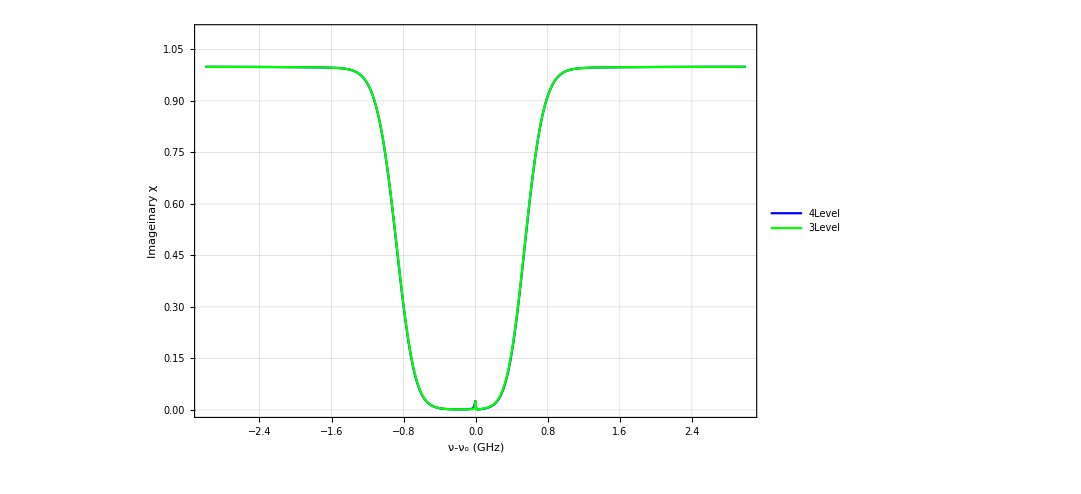

```mathematica
t=65(*C*);
p=185(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

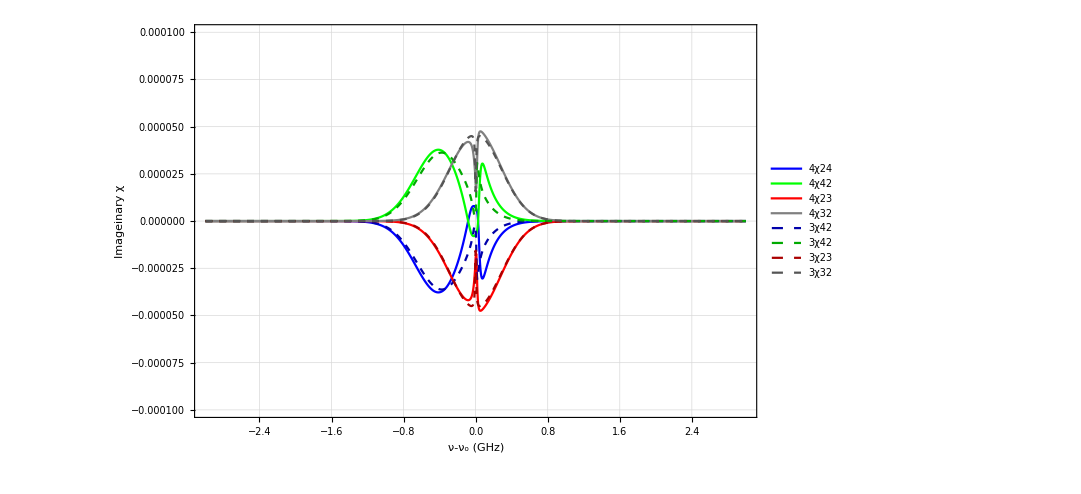

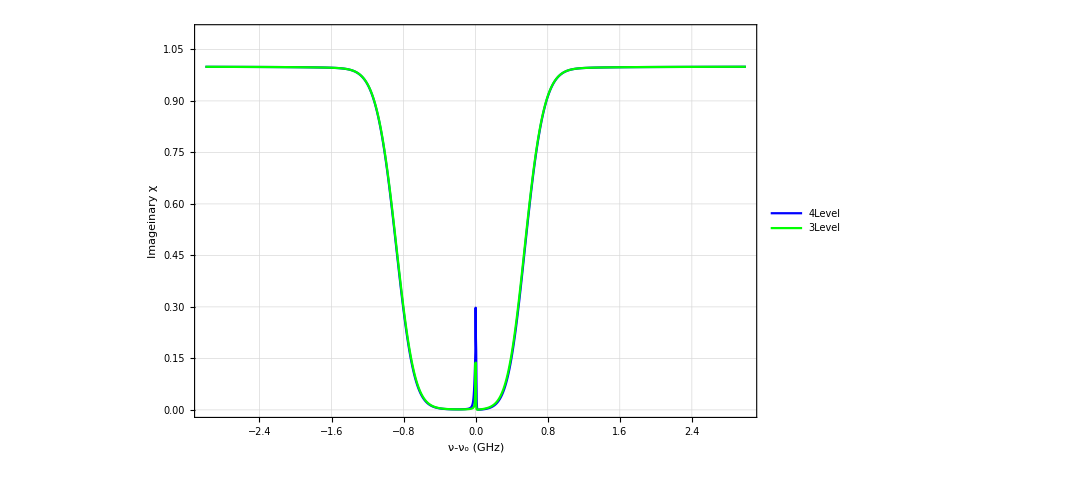

```mathematica
t=65(*C*);
p=500(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

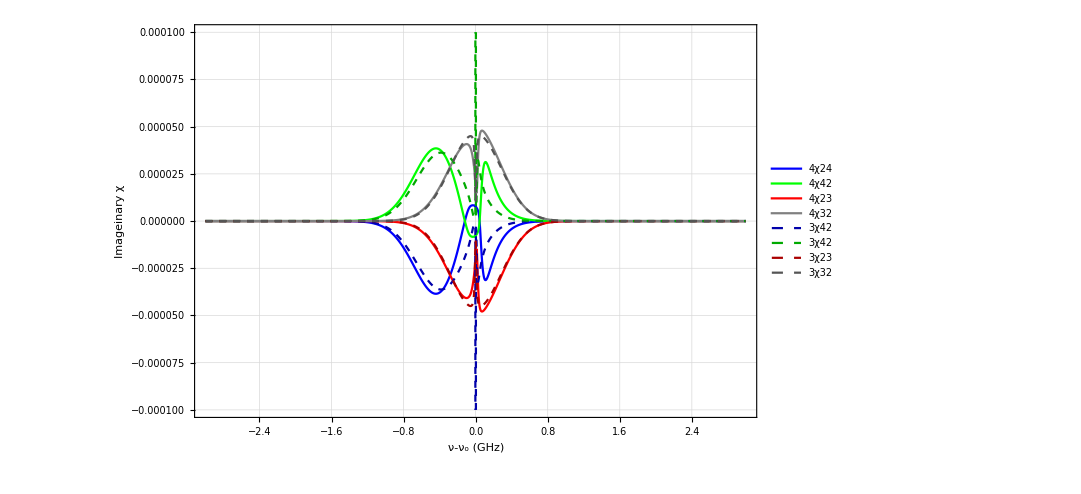

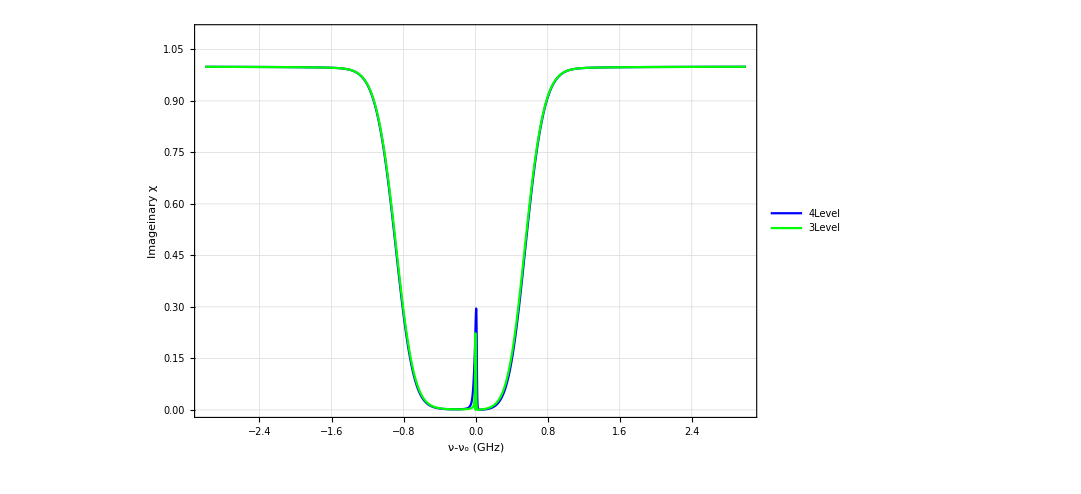

```mathematica
t=65(*C*);
p=800(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

## Change Detuning Δ1 Δ2

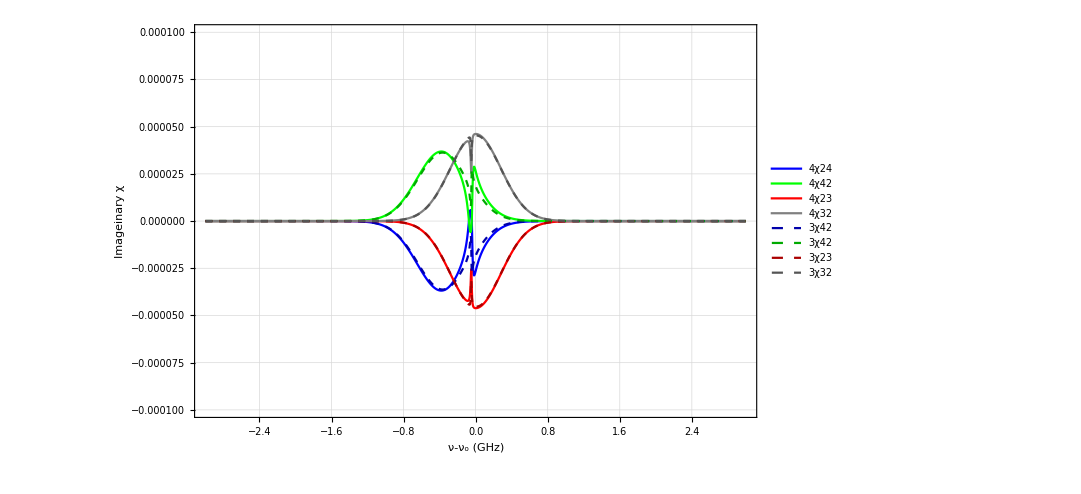

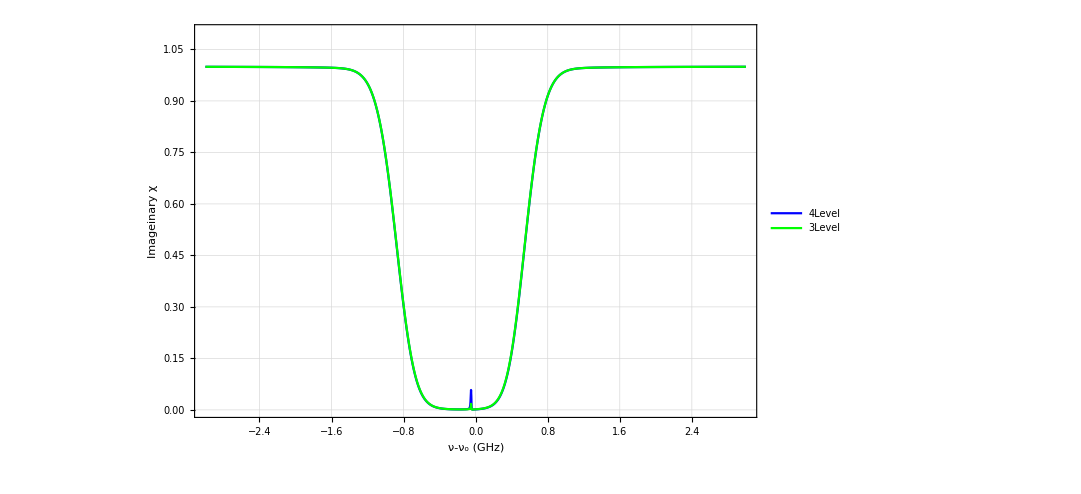

```mathematica
t=65(*C*);
p=150(*mW*);
g=-50(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

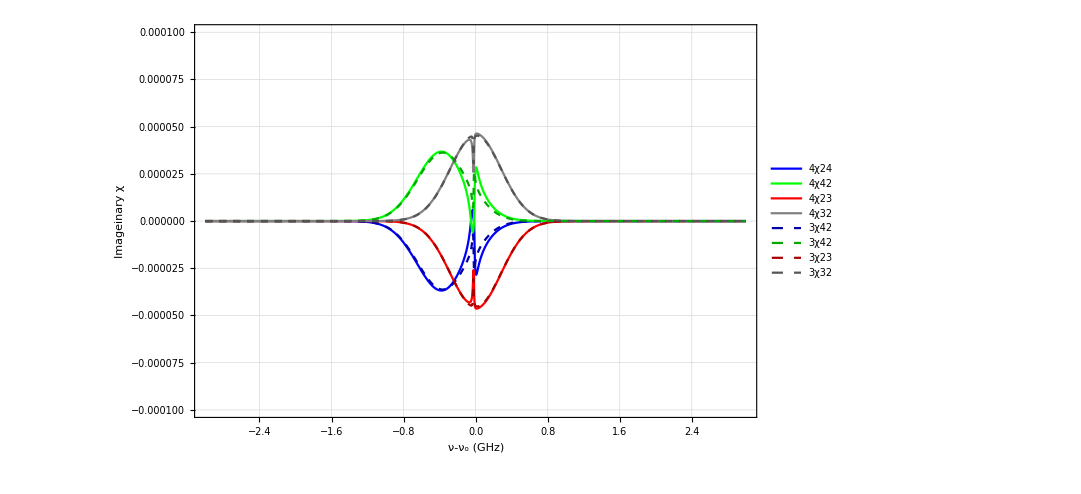

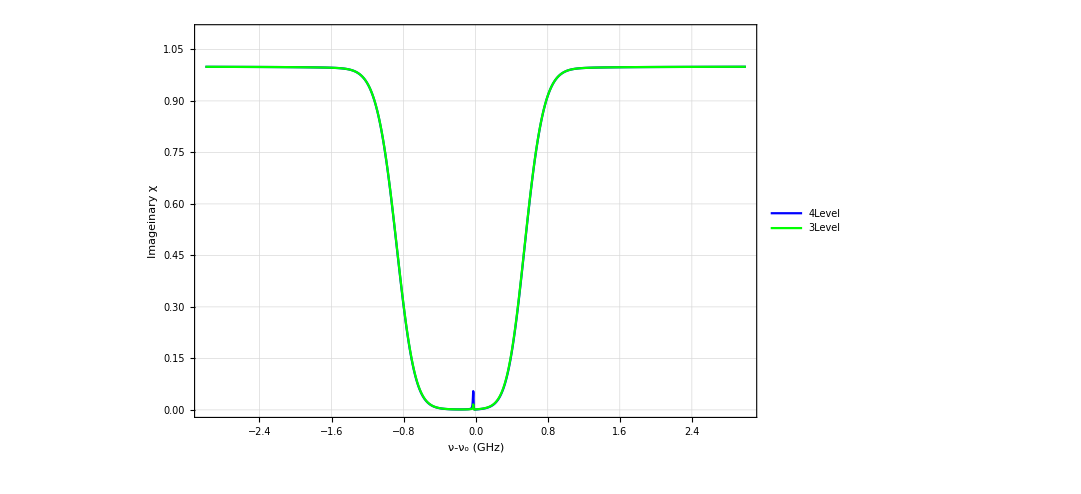

```mathematica
t=65(*C*);
p=150(*mW*);
g=-25(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

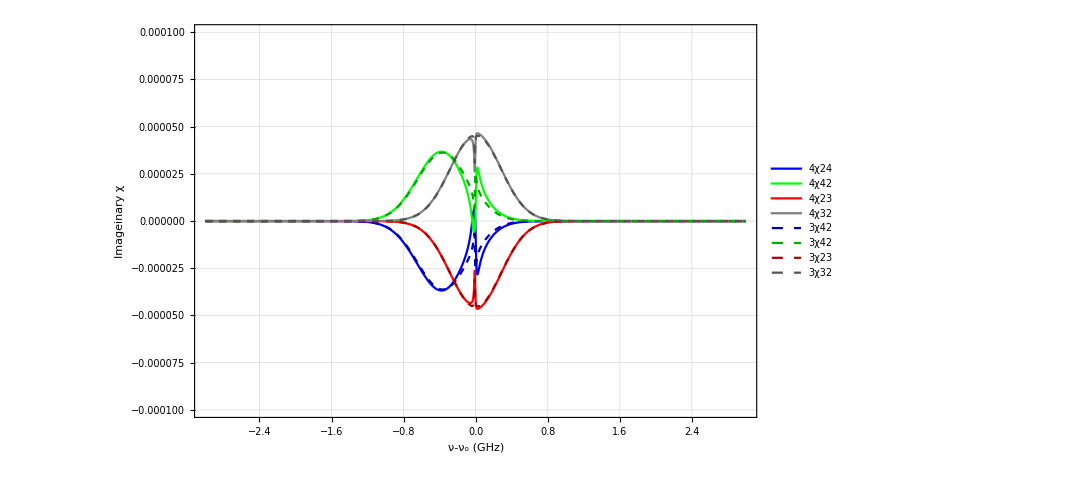

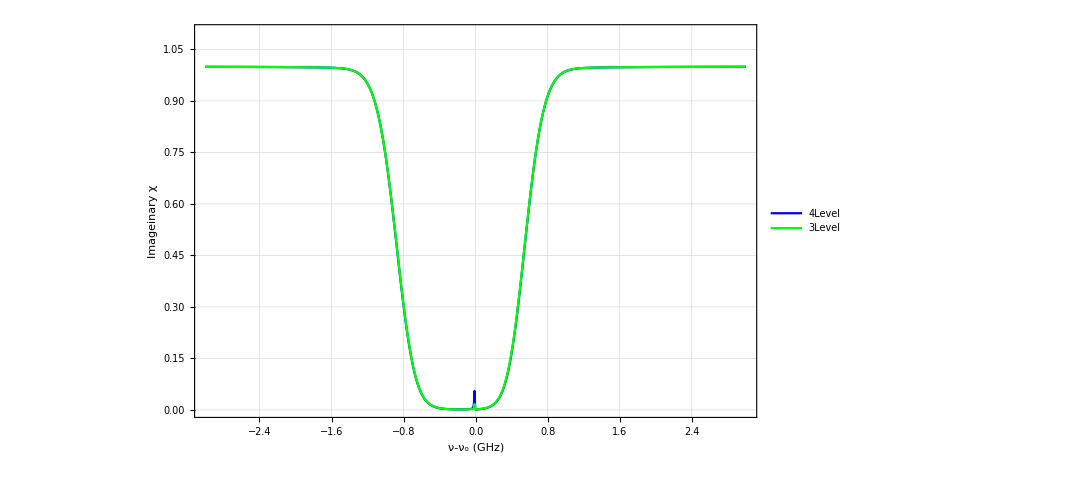

```mathematica
t=65(*C*);
p=150(*mW*);
g=-10(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

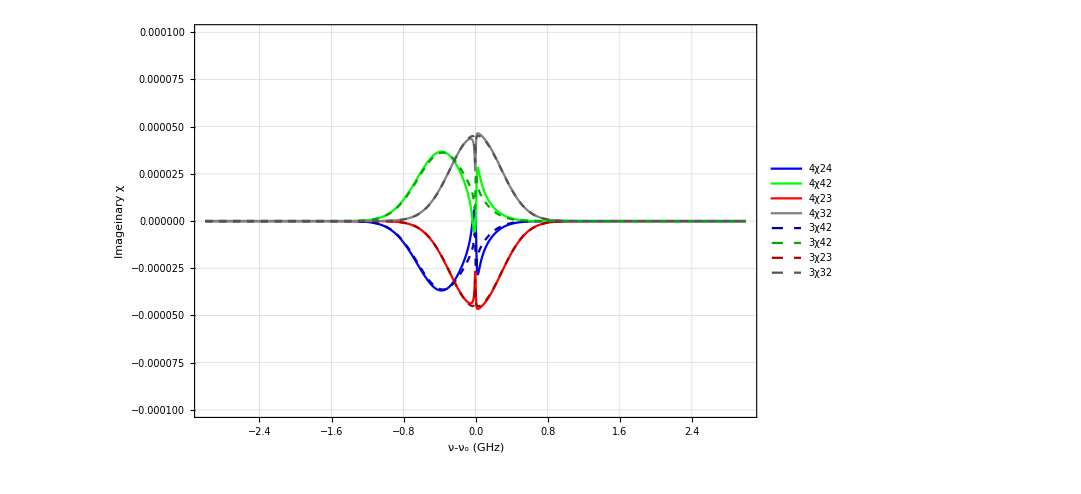

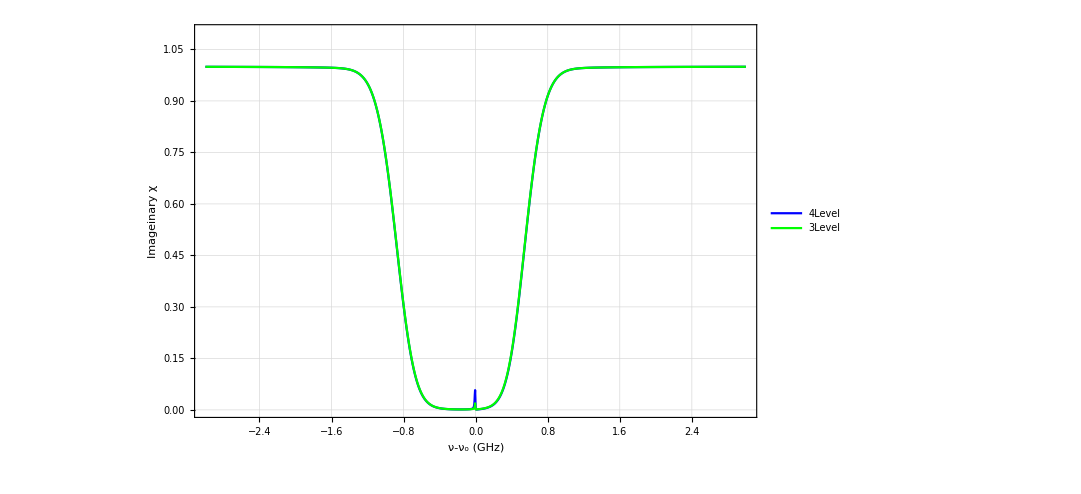

```mathematica
t=65(*C*);
p=150(*mW*);
g=-5(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

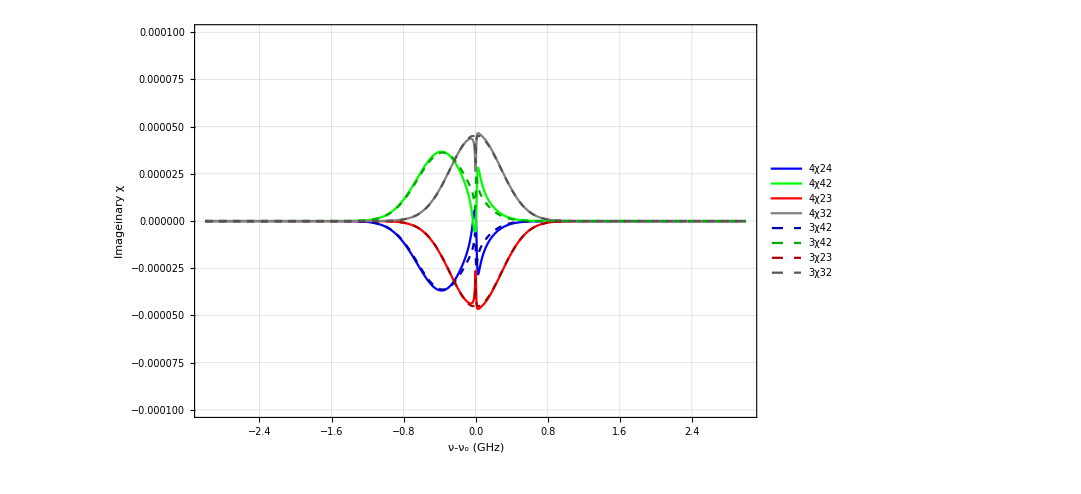

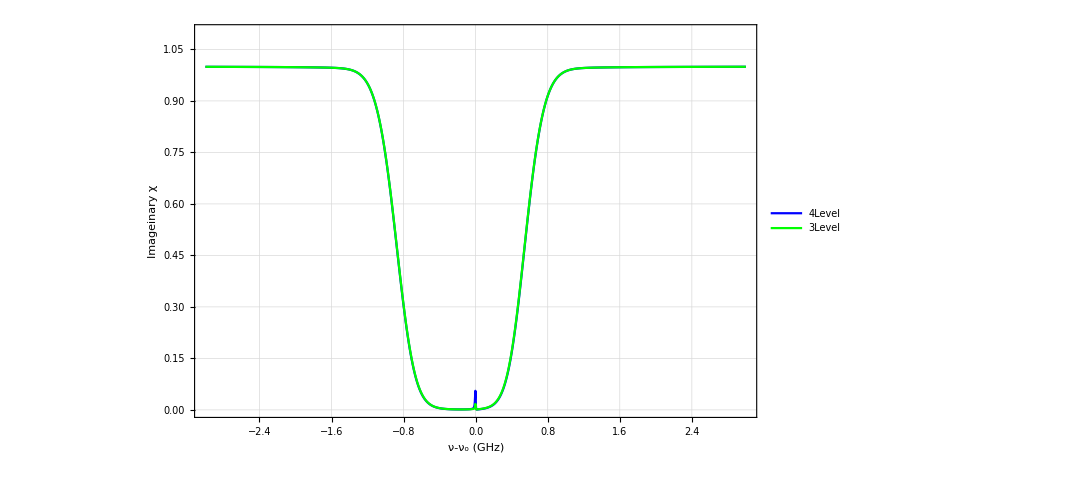

```mathematica
t=65(*C*);
p=150(*mW*);
g=-1(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

```mathematica
t=65(*C*);
p=150(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

-Graphics-

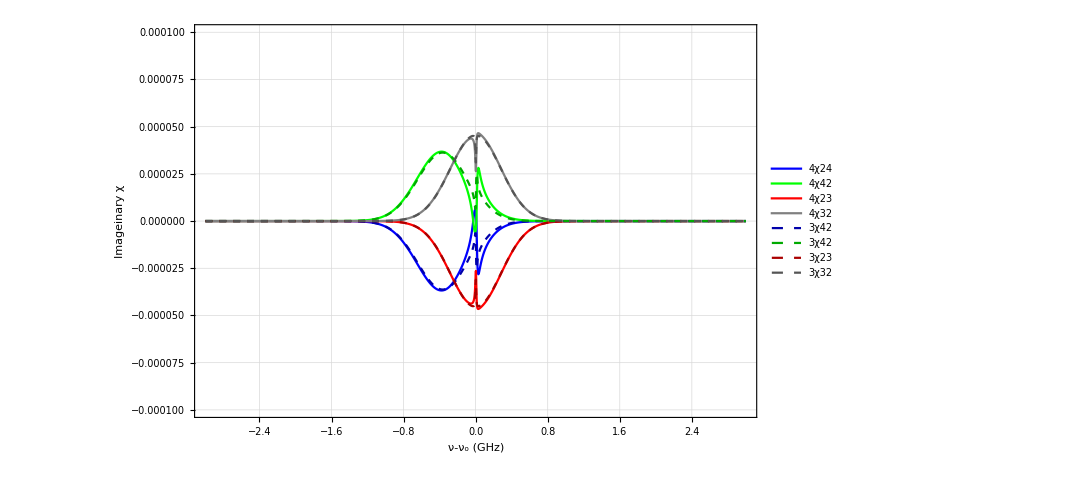

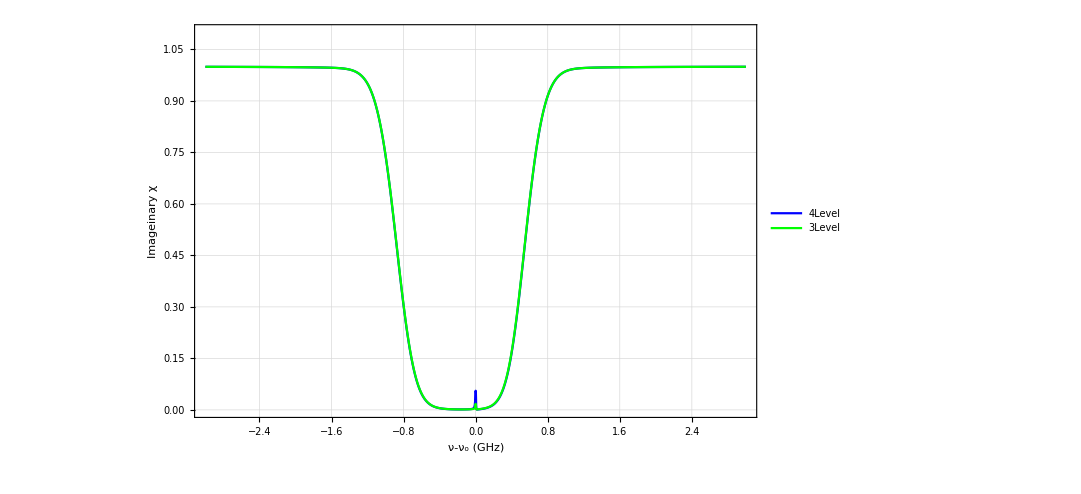

```mathematica
t=65(*C*);
p=150(*mW*);
g=2(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

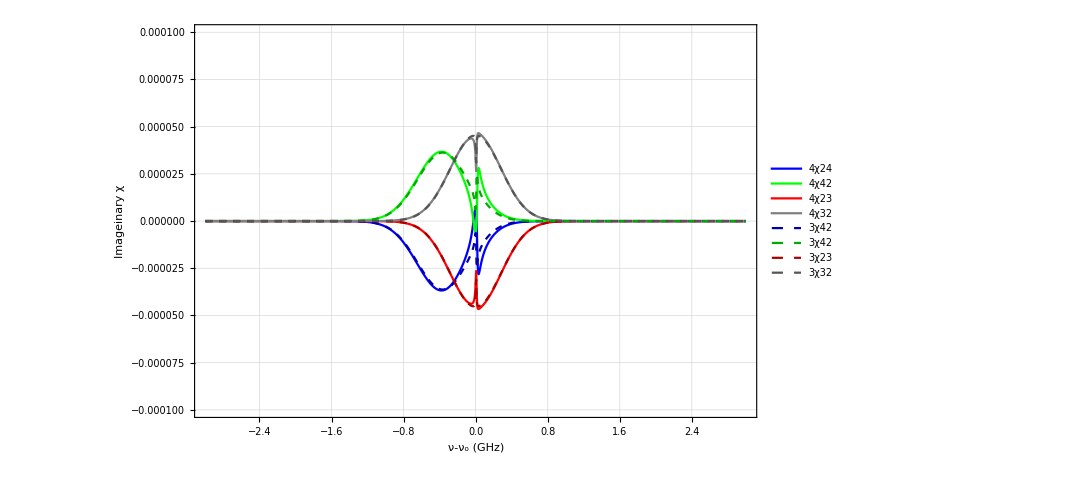

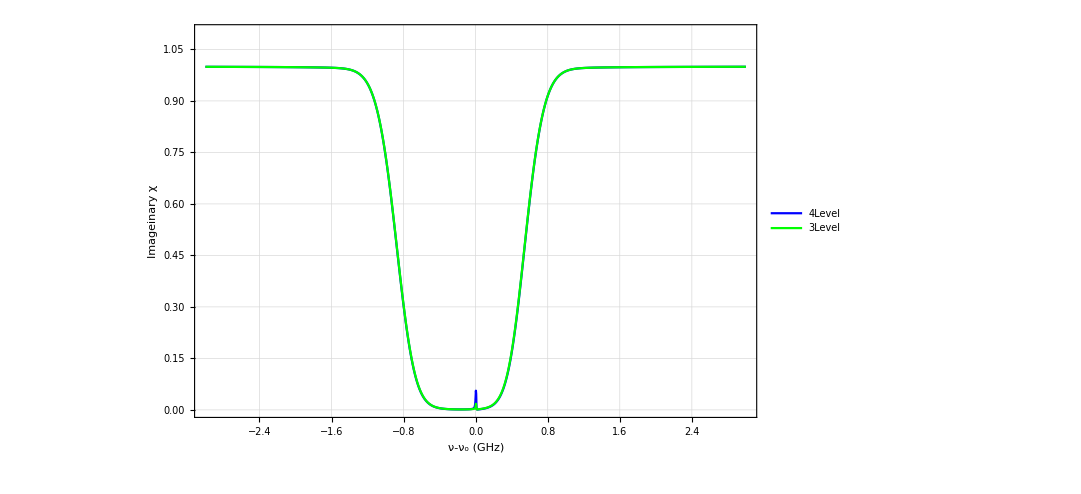

```mathematica
t=65(*C*);
p=150(*mW*);
g=5(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

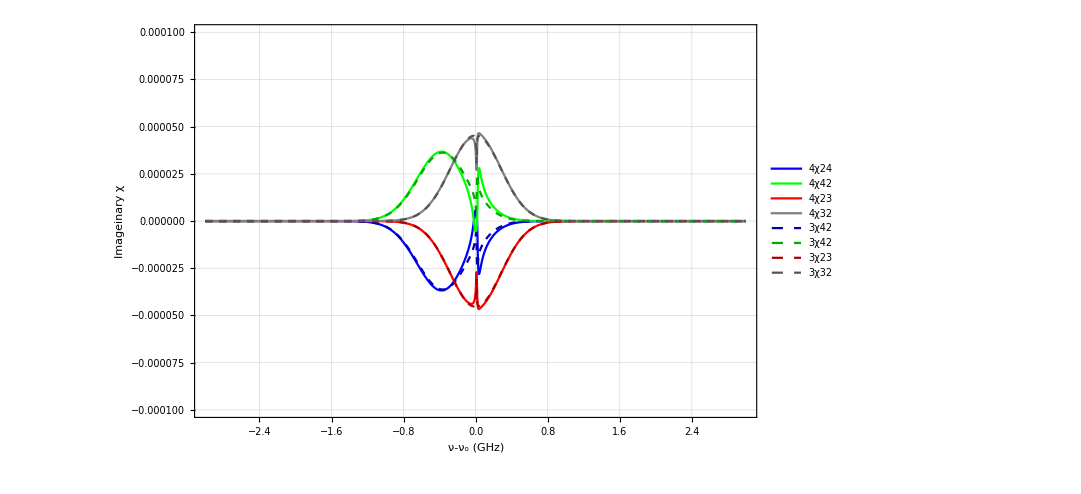

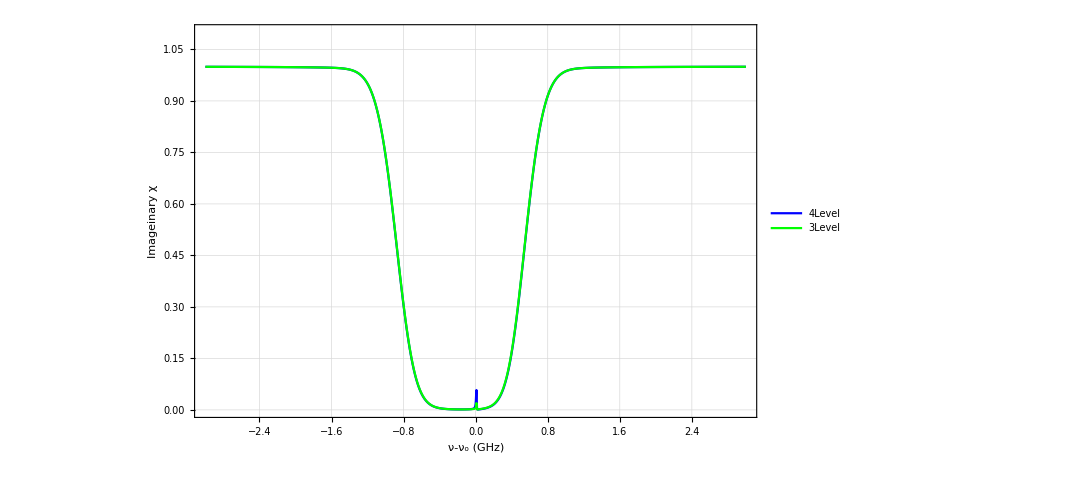

```mathematica
t=65(*C*);
p=150(*mW*);
g=10(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

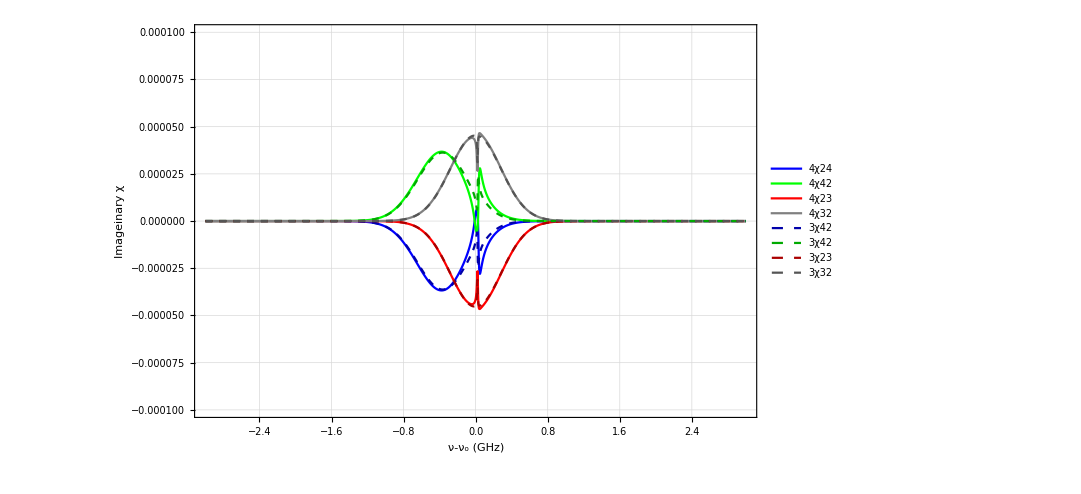

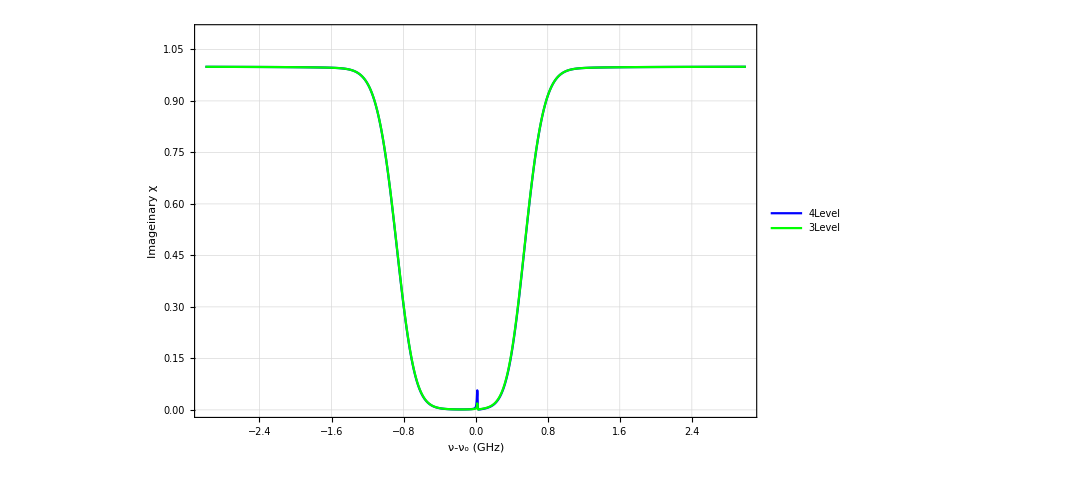

```mathematica
t=65(*C*);
p=150(*mW*);
g=20(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

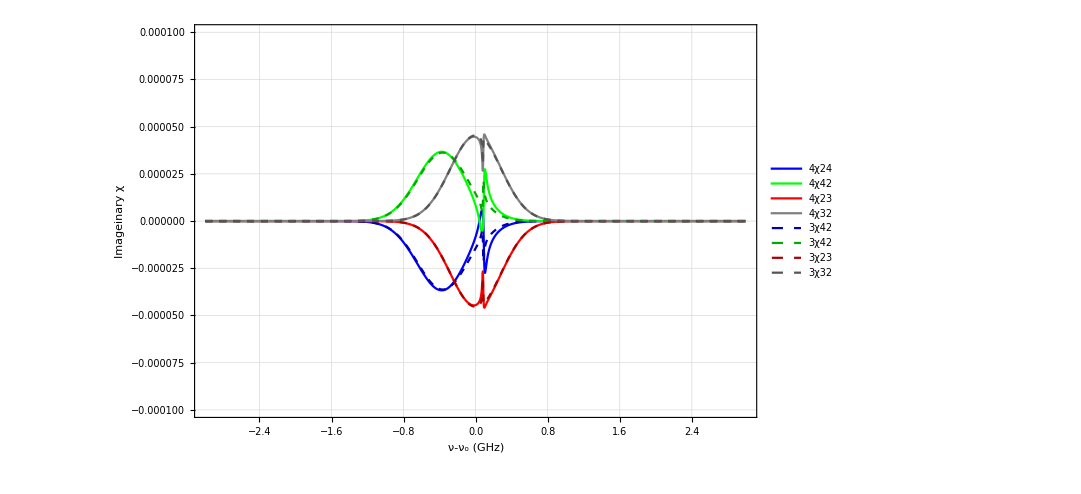

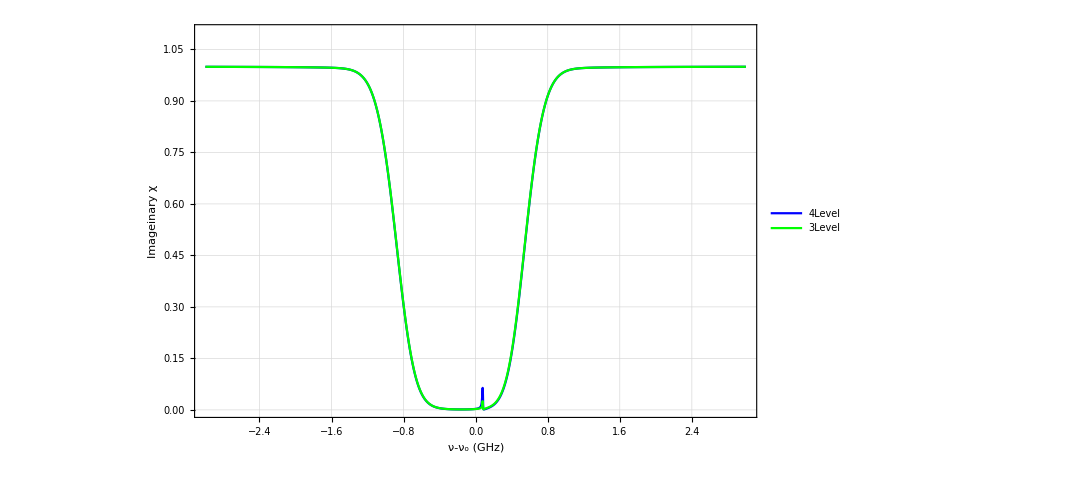

```mathematica
t=65(*C*);
p=150(*mW*);
g=80(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

## Some Cases?

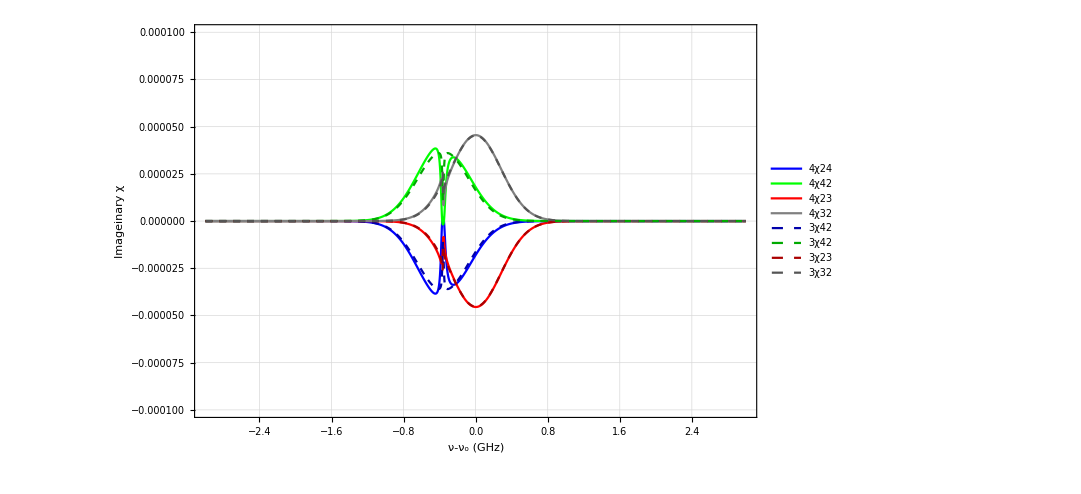

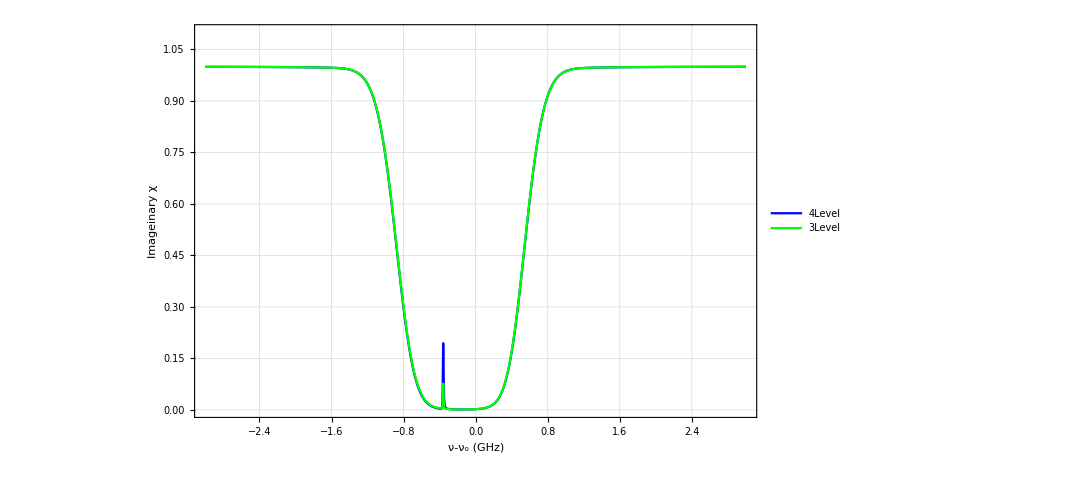

```mathematica
t=65(*C*);
p=180(*mW*);
g=-362(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

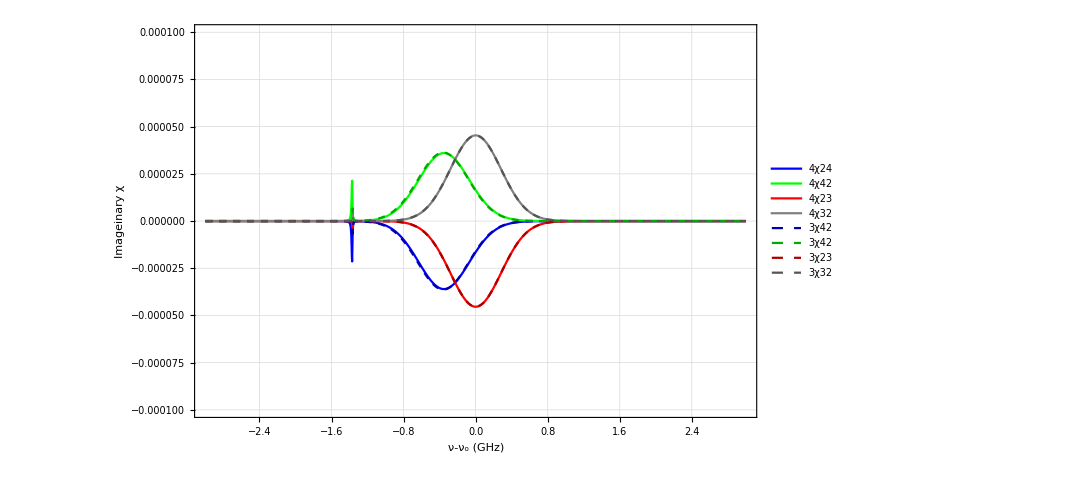

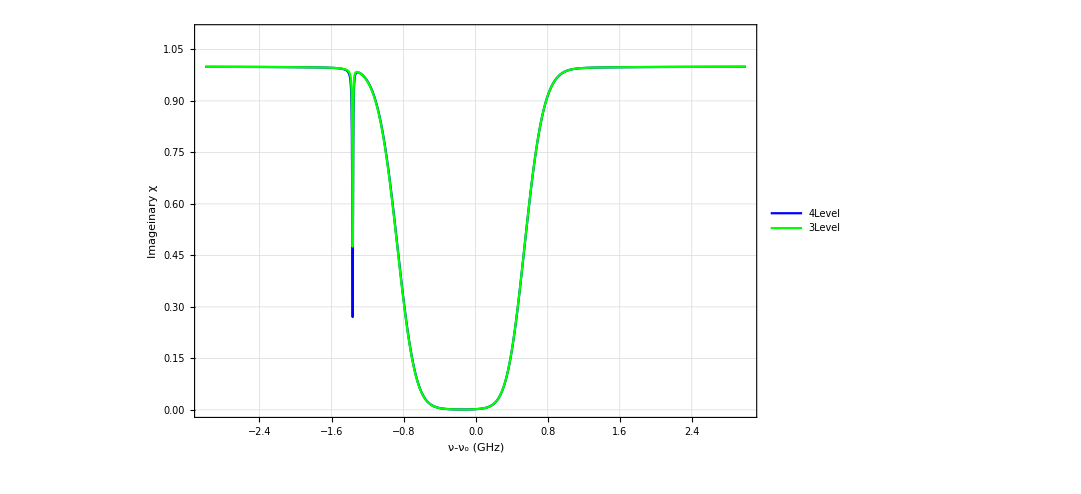

```mathematica
t=65(*C*);
p=180(*mW*);
g=-1362(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

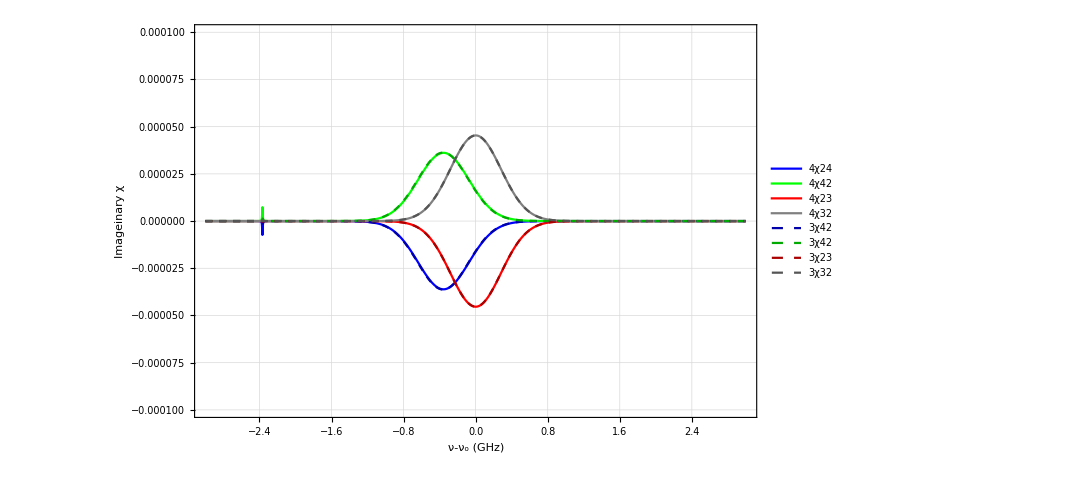

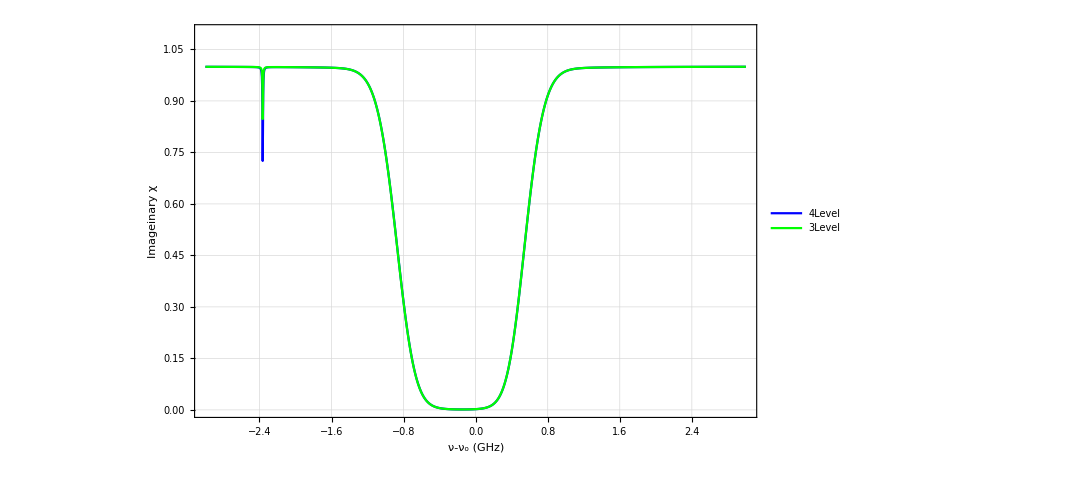

```mathematica
t=65(*C*);
p=180(*mW*);
g=-2362(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

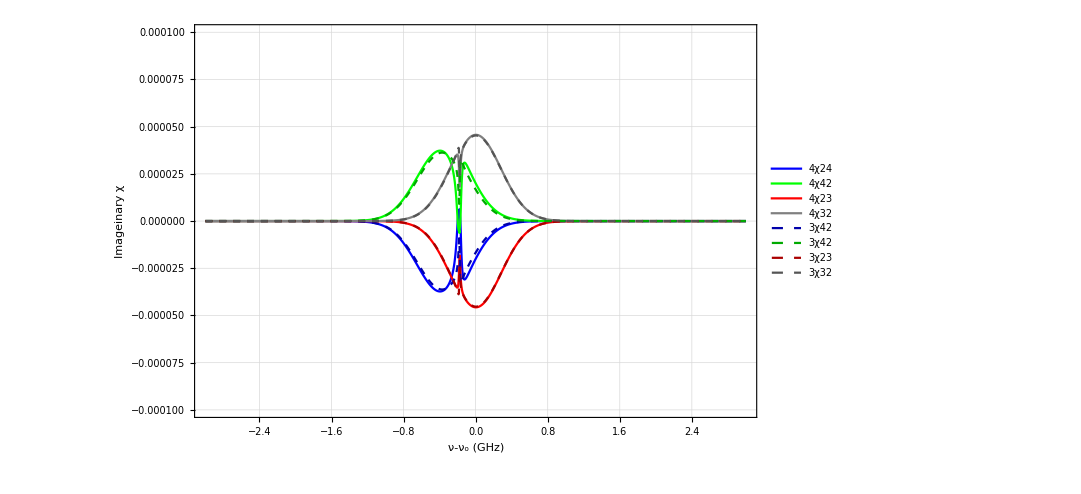

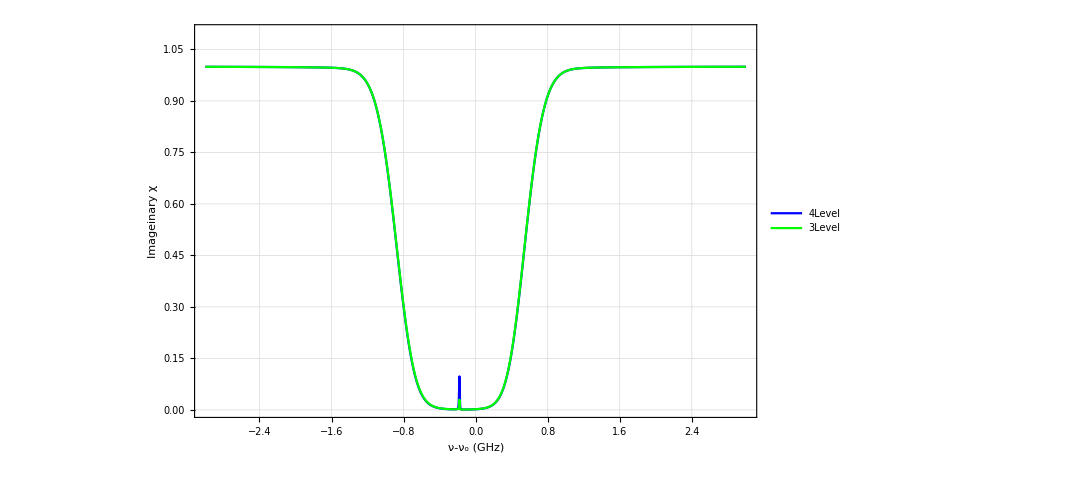

```mathematica
t=65(*C*);
p=180(*mW*);
g=-180(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

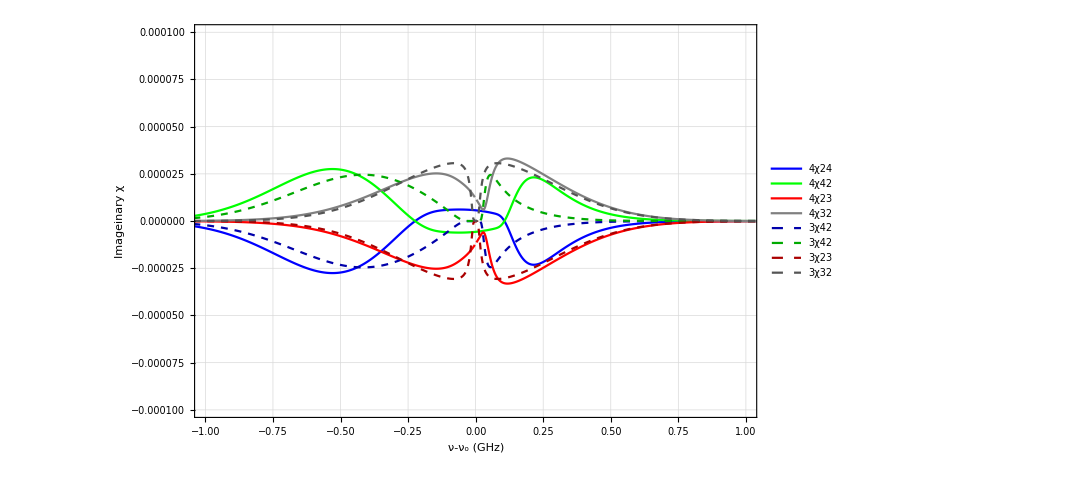

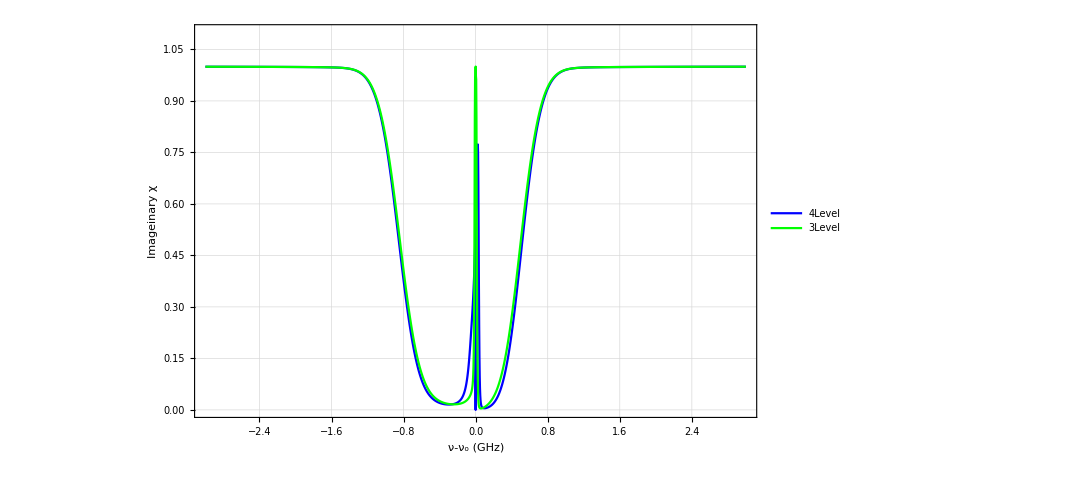

```mathematica
t=60(*C*);
p=2000(*mW*);
g=0(*MHz*);
dc=0.2(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{{-1,1},{-0.0001,0.0001}},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

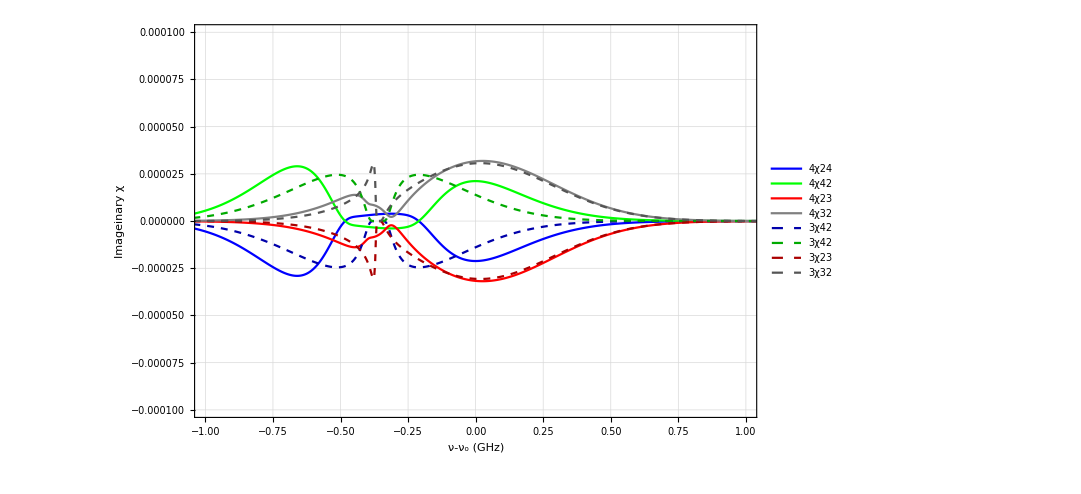

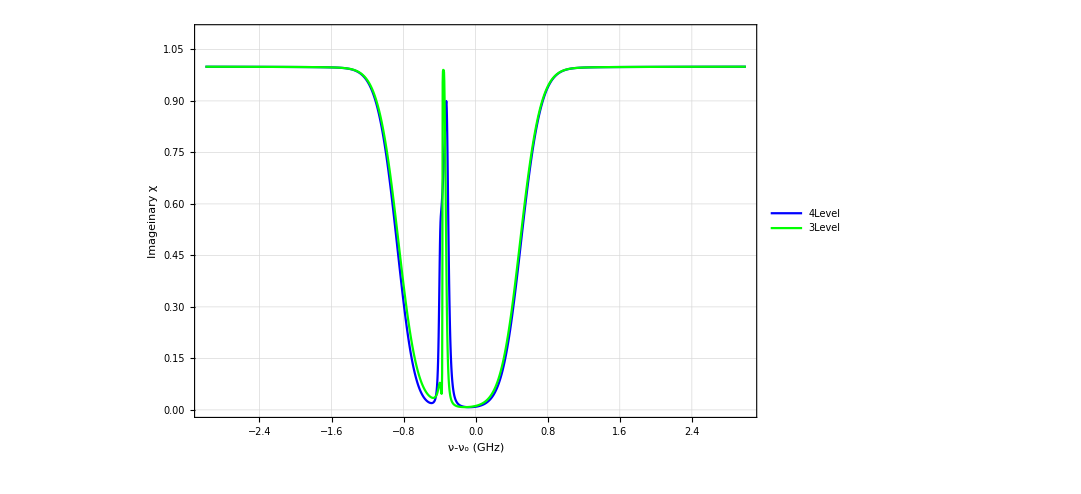

```mathematica
t=60(*C*);
p=2000(*mW*);
g=-361(*MHz*);
dc=.1(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{{-1,1},{-0.0001,0.0001}},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

```mathematica
\
```

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.8,0.5,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
δ=2Pi delt;

Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24+χ23]}],
Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.8,0.5,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
δ=2Pi delt;

Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24+χ23]}],
Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-3,3,0.003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
(*
d=Range[-0.8,0.5,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
δ=2Pi delt;
*)
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24+χ23]}],
Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-3,3,0.003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
(*
d=Range[-0.8,0.5,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
δ=2Pi delt;
*)
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24+χ23]}],
Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
t=50(*C*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
Manipulate[
GraphicsRow[{ListPlot[
Flatten[{Evaluate[Lev4Test[t,p/1000,1.4/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1][[{1,2,3,5,6,7}]]
,PlotRange->{-0.0001,0.00002},PlotStyle->{Blue,{Darker[Blue],Dashed},{Darker[Blue],Dashed},Green,{Darker[Green],Dashed},{Darker[Green],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4","4","4","3","3","3"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800],
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]},ImageSize->2000,AspectRatio->1/1.5]
,{p,0,500}]
```

Part::partw: Part {1,2,3,5,6,7} of {Lev4Test[t,0.5,0.0014,1000000 dc,1000000 g,0],Lev3Test[t,0.5,1/500,1000000 dc,1000000 g,0]} does not exist.

Part::partw: Part {1,2,3,5,6,7} of {Lev4Test[t,0.5,0.0014,1.×10^6 dc,1.×10^6 g,0],Lev3Test[t,0.5,0.002,1.×10^6 dc,1.×10^6 g,0]} does not exist.

Part::partw: Part {1,2,3,5,6,7} of {Lev4Test[t,0.5,0.0014,1.×10^6 dc,1.×10^6 g,0.],Lev3Test[t,0.5,0.002,1.×10^6 dc,1.×10^6 g,0.]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: {Lev4Test[t,0.5,0.0014,1.×10^6 dc,1.×10^6 g,0.],Lev3Test[t,0.5,0.002,1.×10^6 dc,1.×10^6 g,0.]}⟦{1,2,3,5,6,7}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
t=50(*C*);
g=80.3516(*MHz*);
dc=3(*Decoh MHz*);
Manipulate[
GraphicsRow[{ListPlot[
Flatten[{Evaluate[Lev4Testsc[t,p/1000,1.4/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3Testsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1][[{1,2,3,5,6,7}]]
,PlotRange->{-0.0001,0.00002},PlotStyle->{Blue,{Darker[Blue],Dashed},{Darker[Blue],Dashed},Green,{Darker[Green],Dashed},{Darker[Green],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4","4","4","3","3","3"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800],
ListPlot[
{Evaluate[Lev4Testsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Testsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]},ImageSize->2000,AspectRatio->1/1.5]
,{p,0,500}]
```

Part::partw: Part {1,2,3,5,6,7} of {Lev4Testsc[t,0.077,0.0014,1000000 dc,1000000 g,0],Lev3Testsc[t,0.077,1/500,1000000 dc,1000000 g,0]} does not exist.

Part::partw: Part {1,2,3,5,6,7} of {Lev4Testsc[t,0.077,0.0014,1.×10^6 dc,1.×10^6 g,0],Lev3Testsc[t,0.077,0.002,1.×10^6 dc,1.×10^6 g,0]} does not exist.

Part::partw: Part {1,2,3,5,6,7} of {Lev4Testsc[t,0.077,0.0014,1.×10^6 dc,1.×10^6 g,0.],Lev3Testsc[t,0.077,0.002,1.×10^6 dc,1.×10^6 g,0.]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: {Lev4Testsc[t,0.077,0.0014,1.×10^6 dc,1.×10^6 g,0.],Lev3Testsc[t,0.077,0.002,1.×10^6 dc,1.×10^6 g,0.]}⟦{1,2,3,5,6,7}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partw: Part {1,2,3,5,6,7} of {Lev4Testsc[t,0.077,0.0014,1000000 dc,1000000 g,0],Lev3Testsc[t,0.077,1/500,1000000 dc,1000000 g,0]} does not exist.

Part::partw: Part {1,2,3,5,6,7} of {Lev4Testsc[t,0.077,0.0014,1.×10^6 dc,1.×10^6 g,0],Lev3Testsc[t,0.077,0.002,1.×10^6 dc,1.×10^6 g,0]} does not exist.

Part::partw: Part {1,2,3,5,6,7} of {Lev4Testsc[t,0.077,0.0014,1.×10^6 dc,1.×10^6 g,0.],Lev3Testsc[t,0.077,0.002,1.×10^6 dc,1.×10^6 g,0.]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: {Lev4Testsc[t,0.077,0.0014,1.×10^6 dc,1.×10^6 g,0.],Lev3Testsc[t,0.077,0.002,1.×10^6 dc,1.×10^6 g,0.]}⟦{1,2,3,5,6,7}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

## Test

```mathematica
f[T_,ν_]:=ⅇ^(0.025400000000000002 (0.-(5.465628557935481*^8 10^(9.318-4040/T) ⅇ^(-(3228.4977444161646 (1.1139875000000001+ν)^2)/T))/T^(3/2)-(6.832035697419351*^8 10^(9.318-4040/T) ⅇ^(-(3228.4977444161646 (1.4761475000000002+ν)^2)/T))/T^(3/2)))
```

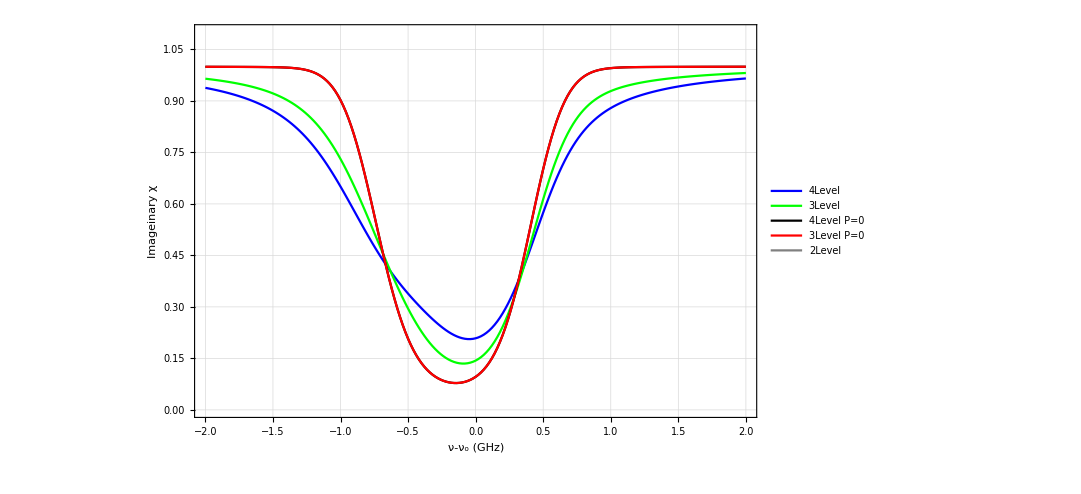

```mathematica
t=53(*C*);
p=10(*mW*);
p2=.5(*mW*);
g=-0.1(*MHz*);
dc=0.5(*Decoh MHz*);
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]],
Evaluate[Lev4DoppTest[t,0/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,0/1000,2/1000,dc*10^6,g*10^6,1]],
Evaluate[Lev2DoppTest[t,p2/1000,2/1000]]
}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green,Black,Red,Gray},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level","4Level P=0","3Level P=0","2Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

```mathematica
Manipulate[ListLinePlot[{Evaluate[Lev4DoppTest[t,15/1000,1.4/1000,0.5*10^6 ,det*10^6,1]],Evaluate[Lev2DoppTest[t,0.2/1000,0.5/1000]]},PlotRange->{0,1}],{{det,0},-2,2,0.001}]
```

```mathematica
Manipulate[ListLinePlot[{Evaluate[Lev4DoppTest[50,100/1000,1.4/1000,0.5*10^6 ,det*10^6,1]],Evaluate[Lev3DoppTest[50,100/1000,1.4/1000,0.5*10^6 ,det*10^6,1]]},PlotRange->{0,1}],{{det,0},-2,2,0.001}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

```mathematica
t=65(*C*);
p=150(*mW*);
g=80(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Flatten[{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,0]]},1]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

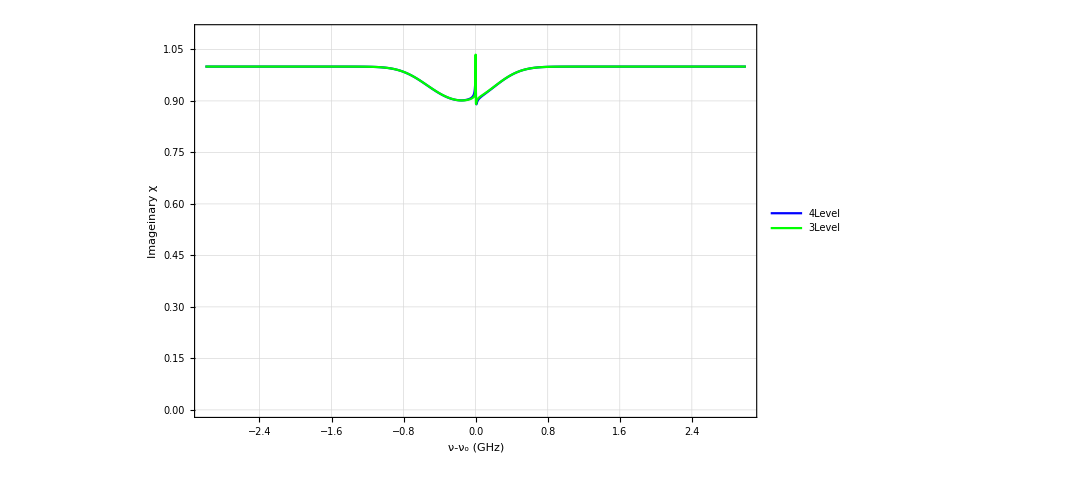

```mathematica
t=20(*C*);
p=100(*mW*);
g=0.1(*MHz*);
dc=0.5(*Decoh MHz*);
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

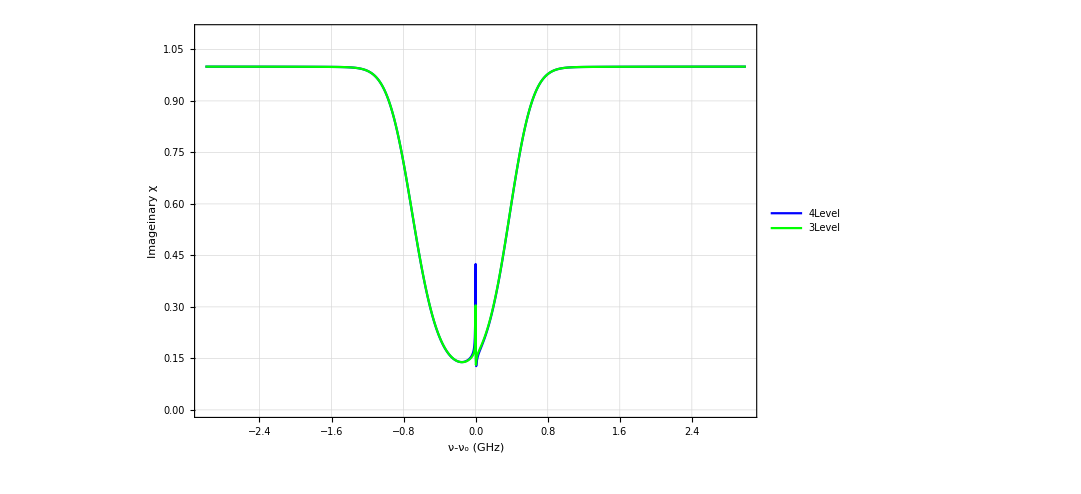

```mathematica
t=50(*C*);
p=50(*mW*);
g=0(*MHz*);
dc=1(*Decoh MHz*);
ListPlot[
{Evaluate[Lev4DoppTestsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],Evaluate[Lev3DoppTestsc[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

# 10mW

Fun

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi(d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;

ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{(d-1.264)/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{(d-1.264)/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

Data

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\Plasmonics With 4WM Lab Books\\Lab Book 4 (April 16 -)\\16-9-26\\Testing EIT\\Pump 10mW"]
```

C:\Users\Admin\Qsync\QOLab\Data\Plasmonics With 4WM Lab Books\Lab Book 4 (April 16 -)\16-9-26\Testing EIT\Pump 10mW

```mathematica
name=FileNames["*.csv"];
order=Ordering[StringSplit[#,"-"]&/@name];
name=name[[order]];
```

```mathematica
Take[name,{27,39}]
```

{Spectrum-0-0.01-1.515-56.281-Sep16-.csv,Spectrum-0-0.01-1.5155-56.7529-Sep16-.csv,Spectrum-0-0.01-1.516-57.1383-Sep16-.csv,Spectrum-0-0.01-1.5165-56.6712-Sep16-.csv,Spectrum-0-0.01-1.517-57.1383-Sep16-.csv,Spectrum-0-0.01-1.5173-57.0565-Sep16-.csv,Spectrum-0-0.01-1.5176-57.0565-Sep16-.csv,Spectrum-0-0.01-1.5179-57.519-Sep16-.csv,Spectrum-0-0.01-1.5182-57.519-Sep16-.csv,Spectrum-0-0.01-1.5188-57.9774-Sep16-.csv,Spectrum-0-0.01-1.5191-57.9774-Sep16-.csv,Spectrum-0-0.01-1.5194-57.895-Sep16-.csv,Spectrum-0-0.01-1.5197-57.9774-Sep16-.csv}

```mathematica
data=Import[#]&/@name;
data1=data[[All,{1,2,3,4,5}]];
```

```mathematica
cutoff[i_]:=Module[{ini,fin},
ini=Position[data1[[i,5]],Max[data1[[i,5]]]][[1,1]];
fin=Position[data1[[i,5]],Min[data1[[i,5]]]][[1,1]];
{Take[data1[[i,3]],{ini,fin}],Take[data1[[i,4]],{ini,fin}]}
]
```

```mathematica
test[i_]:=Module[{λSF3,λSF3PF2,λSF3PF3,ans,points,cc,list1},
points=Select[
FindPeaks[
cutoff[i][[2]],9,0.00005,InterpolationOrder->3]
,500<#[[1]]<1000&];
If[Length[points]>3,
cc=ClusterClassify[points,Method->"DBSCAN"];
points=Table[Mean[GatherBy[points,cc][[j]]],{j,1,3}];
];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF2,points[[3,1]]/m+a==-λSF3PF3},{m,a}][[1]];
list1=Transpose[{Table[j,{j,1,Length[cutoff[i][[1]]]}]/m+a,cutoff[i][[1]]}]/.ans
]
```

```mathematica
normal[i_]:=Module[{Hello,f},
Hello=test[i];
f[x_]:=Evaluate[Fit[Flatten[{Select[Hello,-3.8≤ #[[1]]≤ -2.8&],Select[Hello,0.5≤ #[[1]]≤ 1&]},1],{1,x},x]];
Transpose[{Hello[[All,1]],Table[Hello[[x,2]]/f[Hello[[x,1]]],{x,1,Length[Hello]}]}]
]
```

```mathematica
Manipulate[ListPlot[normal[i]],{i,27,39,1}]
```

Plot

```mathematica
hhh1=Flatten[Table[
Transpose[{Table[1.515+0.0005(i-1),{j,1,Length[normal[26+i]]}],
normal[26+i][[All,1]],
normal[26+i][[All,2]]}]
,{i,1,12}],1]
```

{{1.515,0.945214,0.997201},{1.515,0.942216,0.997198},{1.515,0.939218,0.997196},{1.515,0.93622,1.01014},{1.515,0.933222,0.997191},{1.515,0.930224,0.997188},{1.515,0.927227,0.997186},{1.515,0.924229,1.01013},{1.515,0.921231,0.997181},{1.515,0.918233,0.997178},{1.515,0.915235,0.997176},21732,{1.5205,-4.36002,0.683746},{1.5205,-4.3631,0.671246},{1.5205,-4.36618,0.671179},{1.5205,-4.36926,0.671111},{1.5205,-4.37233,0.671044},{1.5205,-4.37541,0.670976},{1.5205,-4.37849,0.670909},{1.5205,-4.38157,0.670841},{1.5205,-4.38464,0.670774},{1.5205,-4.38772,0.670706}}
 |  |  |  |

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

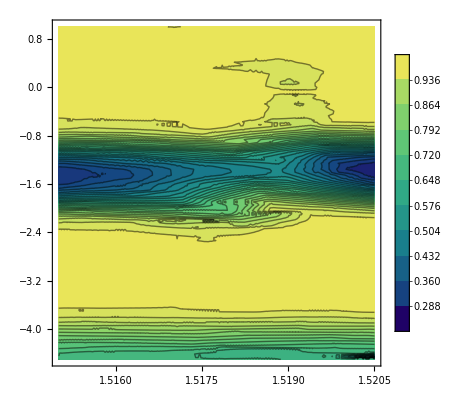

```mathematica
hhh1i=Interpolation[hhh1];
ContourPlot[hhh1i[x,y],{x,1.515,1.5205},{y,-4.5,1},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,Contours->25,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk5=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev4DoppTest[45,10/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

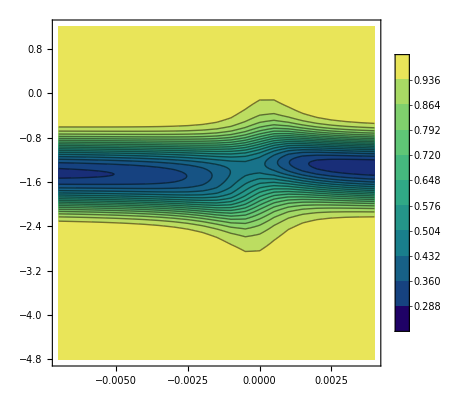

```mathematica
ListContourPlot[kkk5,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk5=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev4Test[44,10/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

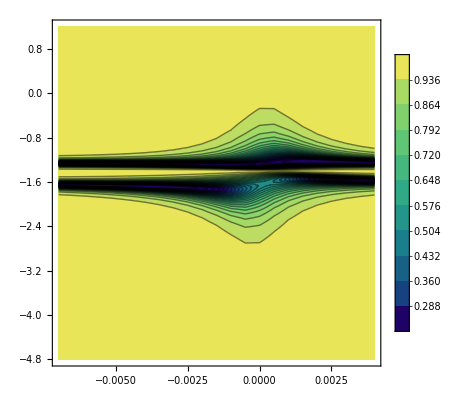

```mathematica
ListContourPlot[kkk5,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk6=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev3DoppTest[45,10/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

```mathematica
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk6=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev3Test[45,10/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

```mathematica
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

# 20mW

Fun

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi(d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{(d-1.264)/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-4.8,1.2,0.02]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{(d-1.264)/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

Data

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\Plasmonics With 4WM Lab Books\\Lab Book 4 (April 16 -)\\16-9-26\\Testing EIT\\Pump 10mW"]
```

C:\Users\Admin\Qsync\QOLab\Data\Plasmonics With 4WM Lab Books\Lab Book 4 (April 16 -)\16-9-26\Testing EIT\Pump 10mW

```mathematica
name=FileNames["*.csv"];
order=Ordering[StringSplit[#,"-"]&/@name];
name=name[[order]];
```

```mathematica
Take[name,{27,39}]
```

{Spectrum-0-0.01-1.515-56.281-Sep16-.csv,Spectrum-0-0.01-1.5155-56.7529-Sep16-.csv,Spectrum-0-0.01-1.516-57.1383-Sep16-.csv,Spectrum-0-0.01-1.5165-56.6712-Sep16-.csv,Spectrum-0-0.01-1.517-57.1383-Sep16-.csv,Spectrum-0-0.01-1.5173-57.0565-Sep16-.csv,Spectrum-0-0.01-1.5176-57.0565-Sep16-.csv,Spectrum-0-0.01-1.5179-57.519-Sep16-.csv,Spectrum-0-0.01-1.5182-57.519-Sep16-.csv,Spectrum-0-0.01-1.5188-57.9774-Sep16-.csv,Spectrum-0-0.01-1.5191-57.9774-Sep16-.csv,Spectrum-0-0.01-1.5194-57.895-Sep16-.csv,Spectrum-0-0.01-1.5197-57.9774-Sep16-.csv}

```mathematica
data=Import[#]&/@name;
data1=data[[All,{1,2,3,4,5}]];
```

```mathematica
cutoff[i_]:=Module[{ini,fin},
ini=Position[data1[[i,5]],Max[data1[[i,5]]]][[1,1]];
fin=Position[data1[[i,5]],Min[data1[[i,5]]]][[1,1]];
{Take[data1[[i,3]],{ini,fin}],Take[data1[[i,4]],{ini,fin}]}
]
```

```mathematica
test[i_]:=Module[{λSF3,λSF3PF2,λSF3PF3,ans,points,cc,list1},
points=Select[
FindPeaks[
cutoff[i][[2]],9,0.00005,InterpolationOrder->3]
,500<#[[1]]<1000&];
If[Length[points]>3,
cc=ClusterClassify[points,Method->"DBSCAN"];
points=Table[Mean[GatherBy[points,cc][[j]]],{j,1,3}];
];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF2,points[[3,1]]/m+a==-λSF3PF3},{m,a}][[1]];
list1=Transpose[{Table[j,{j,1,Length[cutoff[i][[1]]]}]/m+a,cutoff[i][[1]]}]/.ans
]
```

```mathematica
normal[i_]:=Module[{Hello,f},
Hello=test[i];
f[x_]:=Evaluate[Fit[Flatten[{Select[Hello,-3.8≤ #[[1]]≤ -2.8&],Select[Hello,-0.7≤ #[[1]]≤ 0.5&]},1],{1,x},x]];
Transpose[{Hello[[All,1]],Table[Hello[[x,2]]/f[Hello[[x,1]]],{x,1,Length[Hello]}]}]
]
```

```mathematica
Manipulate[ListPlot[normal[i]],{i,27,39,1}]
```

Plot

```mathematica
hhh2=Flatten[Table[
Transpose[{Table[1.515+0.0005(i-1),{j,1,Length[normal[26+i]]}],
normal[26+i][[All,1]],
normal[26+i][[All,2]]}]
,{i,1,12}],1]
```

{{1.515,0.945214,0.995112},{1.515,0.942216,0.995112},{1.515,0.939218,0.995112},{1.515,0.93622,1.00803},{1.515,0.933222,0.995111},{1.515,0.930224,0.995111},{1.515,0.927227,0.995111},{1.515,0.924229,1.00803},{1.515,0.921231,0.99511},{1.515,0.918233,0.99511},{1.515,0.915235,0.99511},21732,{1.5205,-4.36002,0.686359},{1.5205,-4.3631,0.673817},{1.5205,-4.36618,0.673754},{1.5205,-4.36926,0.673691},{1.5205,-4.37233,0.673628},{1.5205,-4.37541,0.673565},{1.5205,-4.37849,0.673502},{1.5205,-4.38157,0.673439},{1.5205,-4.38464,0.673376},{1.5205,-4.38772,0.673313}}
 |  |  |  |

```mathematica
hhh2i=Interpolation[hhh2];
ContourPlot[hhh2i[x,y],{x,1.515,1.5205},{y,-4.5,1},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,Contours->25,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk5=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev4DoppTest[45,20/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

```mathematica
ListContourPlot[kkk5,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk5=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev4Test[45,20/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

```mathematica
ListContourPlot[kkk5,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk6=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev3DoppTest[45,20/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

```mathematica
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk6=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,301}],
Lev3Test[45,20/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.007,0.004,0.0005}]],3];
```

```mathematica
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

# 200 mW

Fun

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-6.3,0.3,0.01]*10^9;
Δ=2Pi(d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-6.3,0.3,0.01]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-6.3,0.3,0.05]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{(d+1.264)/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d41,d31},
d=Range[-6.3,0.3,0.05]*10^9;
Δ=2Pi (d+1.264*10^9);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

Data

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\Plasmonics With 4WM Lab Books\\Lab Book 4 (April 16 -)\\16-9-26\\Testing EIT\\Deep shift 200mW without Shield"];
name=FileNames["*.csv"];
```

```mathematica
data=Import[#]&/@name;
data1=data[[All,{1,2,3,4,5}]];
```

```mathematica
cutoff[i_]:=Module[{ini,fin},
ini=Position[data1[[i,5]],Max[data1[[i,5]]]][[1,1]];
fin=Position[data1[[i,5]],Min[data1[[i,5]]]][[1,1]];
{Take[data1[[i,3]],{ini,fin}],Take[data1[[i,4]],{ini,fin}]}
]
```

```mathematica
test[i_]:=Module[{λSF3,λSF3PF2,λSF3PF3,ans,points,cc,list1},
points=Select[
FindPeaks[
cutoff[i][[2]],9,0.00005,InterpolationOrder->3]
,0<#[[1]]<700&];
If[Length[points]>3,
cc=ClusterClassify[points,Method->"DBSCAN"];
points=Table[Mean[GatherBy[points,cc][[j]]],{j,1,3}];
];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF2,points[[3,1]]/m+a==-λSF3PF3},{m,a}][[1]];
list1=Transpose[{Table[j,{j,1,Length[cutoff[i][[1]]]}]/m+a,cutoff[i][[1]]}]/.ans
]
```

```mathematica
normal[i_]:=Module[{Hello,f},
Hello=test[i];
f[x_]:=Evaluate[Fit[Select[Hello,-6≤ #[[1]]≤ -5&],{1,x},x]];
Transpose[{Hello[[All,1]],Table[Hello[[x,2]]/f[Hello[[x,1]]],{x,1,Length[Hello]}]}]
]
```

Plot

```mathematica
hhh3=Flatten[Table[
Transpose[{Table[1.508+0.001(i-1),{j,1,Length[normal[i]]}],
normal[i][[All,1]],
normal[i][[All,2]]}]
,{i,1,29}],1]
```

{{1.508,0.192365,1.03667},{1.508,0.188903,1.02701},{1.508,0.18544,1.03655},{1.508,0.181977,1.0269},{1.508,0.178515,1.03644},{1.508,0.175052,1.02679},{1.508,0.171589,1.02673},{1.508,0.168127,1.02667},{1.508,0.164664,1.02662},{1.508,0.161201,1.03615},{1.508,0.157739,1.0361},52876,{1.536,-6.05429,0.998461},{1.536,-6.0578,0.998419},{1.536,-6.06131,0.998377},{1.536,-6.06482,0.998334},{1.536,-6.06833,0.998292},{1.536,-6.07184,0.99825},{1.536,-6.07535,0.998207},{1.536,-6.07886,0.998165},{1.536,-6.08237,0.998123},{1.536,-6.08588,0.99808}}
 |  |  |  |

```mathematica
hhh3i=Interpolation[hhh3];
ContourPlot[hhh3i[x,y],{x,1.508,1.536},{y,0.2,-6},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,Contours->25,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk5=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,133}],
Lev4DoppTest[45,200/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.028,0.028,0.000575}]],3];
```

```mathematica
ListContourPlot[kkk5,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk5=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,661}],
Lev4Test[45,200/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.028,0.028,0.001}]],3];
```

```mathematica
ListContourPlot[kkk5,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk6=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,133}],
Lev3DoppTest[45,200/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.028,0.028,0.00057}]],3];
```

```mathematica
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
Off[General::ovfl]
Off[General::unfl]
kkk6=
Partition[Flatten[Table[
Transpose[{Table[delt,{i,1,661}],
Lev3Test[45,200/1000,1.4/1000,1.125*10^6,delt*10^9,1]}]
,{delt,-0.028,0.028,0.00057}]],3];
```

```mathematica
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

Extract Decoherence Rate

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-4,2,0.1]*10^9;
Δ=2Pi  (d);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]]}],

Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]+sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]]}]
}
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-4,2,0.1]*10^9;
Δ=2Pi  (d);(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_]:=Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-3,3,0.0005] 10^9;Δ=2 π d;Nat=Rbpress[T]⟦1⟧;δ=2 π delt;γ21=2 π gam;γ32=2/2 π 5.750056 10^6;γ42=2/2 π 5.750056 10^6;d32=(√(5/27) 2.537717)/10^29;d42=(√(4/27) 2.537717)/10^29;d31=(√(2/27) 2.537717)/10^29;d41=(√(7/27) 2.537717)/10^29;ℏ=1.0546/10^34;e0=8.8542/10^12;c=2.9979 10^8;wcn=794.76728224/10^9;wc=2 π 377.107385 10^12;w43=2 π (210.923 10^6)+2 π (150.659 10^6);u=Rbpress[T]⟦4⟧;omegac1=(√(1/(e0 c)) d31 √(P/(π (diam/2)^2)))/ℏ;omegac2=(√(1/(e0 c)) d41 √(P/(π (diam/2)^2)))/ℏ;χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);If[ab==0,{Transpose[{d/10^9,Im[χ24]}],Transpose[{d/10^9,Im[χ42]}],Transpose[{d/10^9,Im[χ23]}],Transpose[{d/10^9,Im[χ32]}]},
{Transpose[{d/10^9,Exp[-(2 π 0.0254 (Im[χ42]))/(2 wcn)]}],
Transpose[{d/10^9,Exp[-(2 π 0.0254 (Im[χ32]))/(2 wcn)]}],
Transpose[{d/10^9,Exp[-(2 π 0.0254 (Im[χ42]+Im[χ32]))/(2 wcn)]}]
}

]]
```

```mathematica
Lev4Test[10,10/1000,2/1000,0*10^6 ,0.1*10^6,1]
```

{{-0.8,0.999991},{-0.7995,0.999991},{-0.799,0.999991},{-0.7985,0.999991},{-0.798,0.999991},{-0.7975,0.999991},{-0.797,0.999991},{-0.7965,0.999991},{-0.796,0.999991},{-0.7955,0.999991},{-0.795,0.999991},{-0.7945,0.999991},{-0.794,0.999991},{-0.7935,0.999991},2573,{0.4935,0.999948},{0.494,0.999948},{0.4945,0.999948},{0.495,0.999948},{0.4955,0.999948},{0.496,0.999947},{0.4965,0.999947},{0.497,0.999947},{0.4975,0.999947},{0.498,0.999947},{0.4985,0.999947},{0.499,0.999947},{0.4995,0.999947},{0.5,0.999947}}
 |  |  |  |

```mathematica
Manipulate[
ListPlot[
{Lev4TestNum[t,100/1000000,0.5/1000,p/1000,1/1000,dc 10^6,g 10^6],Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1][[3]]},Joined->True,PlotRange->{0,1.5}]
,{{t,41},0,80},{{p,200},0,200},{{dc,0.85},0.001,3},{{g,-4},-20,20}]
```

```mathematica
Manipulate[
ListPlot[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1],Joined->True,PlotRange->{0,1.5}]


,{{t,41},0,80},{{p,200},0,200},{{dc,0.85},0.001,3},{{g,-4},-20,20}]
```

```mathematica
Manipulate[
Show[ListPlot[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1],Joined->True,PlotRange->{0,1.5}]
,ListPlot[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1],Joined->True,PlotRange->All]]

,{{t,41},0,80},{{p,200},0,200},{{dc,0.85},0.001,3},{i,1,29,1},{{g,-4},-20,20}]
```

```mathematica
Manipulate[
ListPlot[
{Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,g*10^6,1]],
fff[i]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
,{{t,41},0,80},{{p,200},0,200},{{dc,0.85},0.001,3},{i,1,29,1},{{g,-4},-20,20}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

$Aborted[]

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

```mathematica
Do[
ffff[i]=normal[i];
,{i,27,39}]
```

```mathematica
.08
```

```mathematica
39-27
```

12

```mathematica
ffff[1]
```

ffff[1]

```mathematica
Manipulate[
ListPlot[
{Evaluate[Lev3DoppTest[t,p/1000,2/1000,dc*10^6,(g+2i)*10^6,1]],Evaluate[Lev4DoppTest[t,p/1000,2/1000,dc*10^6,(g+2i)*10^6,1]],ffff[i]}
,PlotRange->{0,1.1},PlotStyle->{Green,Blue,Black},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
,{{t,41},0,80},{{p,20},0,200},{{dc,0.85},0.001,3},{i,1,12,1},{{g,-4},-20,20}]
```

Transpose::nmtx: The first two levels of {{-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«11»},ⅇ^(-200805. Im[Null])} cannot be transposed.

Transpose::nmtx: The first two levels of {{-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«11»},2.718281828459045^(-200805. Im[Null])} cannot be transposed.

Transpose::nmtx: The first two levels of {{-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,«11»},2.71828^(-200805. Im[Null])} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

## Without Doppler

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI},
d=Range[-0.8,0.5,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]); 


χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
t=45(*C*);
p=3(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Evaluate[Lev4Test1[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]]
,PlotRange->{-0.00005,0.00005},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
```

-Graphics-

```mathematica
t=45(*C*);
p=3(*mW*);
g=0(*MHz*);
dc=3(*Decoh MHz*);
ListPlot[
Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]]
,PlotRange->{-0.00001,0.00001},PlotStyle->{Blue,Green,Red,Gray,{Darker[Blue],Dashed},{Darker[Green],Dashed},{Darker[Red],Dashed},{Darker[Gray],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24","4χ42","4χ23","4χ32","3χ42","3χ42","3χ23","3χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
```

-Graphics-

# Compare

## 200mW (Experiment/4levels/3levels/No Dop 4/NoDop3)

```mathematica
-Graphics--Graphics--Graphics--Graphics-
s-Graphics--Graphics-
```

## 20mW (Experiment/4levels/3levels)

```mathematica
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics-
```

## 10mW

```mathematica
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics-
```

# Extract Interference Term

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ)
```

```mathematica
χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ);
```

## w43->inf

Δ=Δ

```mathematica
Limit[(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ),w43->∞]
Limit[-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ),w43->∞]
Limit[(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ),w43->∞]
Limit[(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ),w43->∞]
```

0

(4 ⅈ d32^2 Nat (γ21+ⅈ δ))/(e0 (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)

0

(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (ⅈ omegac1^2+4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)) ℏ)

3Level 32

```mathematica
(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ);
```

Δ=w43+Δ

```mathematica
Limit[(d42^2 Nat ((4 √5-5 √14) omegac2^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac2^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)/.Δ->Δ-w43/.omegac2->Sqrt[2/7]omegac1,w43->∞]
Limit[-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)/.Δ->Δ-w43,w43->∞]
Limit[(d42^2 Nat (ⅈ (4 √5-5 √14) omegac2^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac2^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ)/.Δ->Δ-w43/.omegac2->Sqrt[2/7]omegac1,w43->∞]
Limit[(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ)/.Δ->Δ-w43,w43->∞]
```

(4 ⅈ d42^2 Nat (γ21+ⅈ δ))/(e0 (omegac1^2+4 (γ21+ⅈ δ) (γ42+ⅈ (δ+Δ))) ℏ)

0

(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (ⅈ omegac1^2+4 (γ21-ⅈ δ) (ⅈ γ42+δ+Δ)) ℏ)

0

3Level 42

```mathematica
(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac2^2) ℏ)
```

## Interference Term

x42

```mathematica
fff=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)/.Δ->Δ-w43
Apart[fff/((8 d42^2 Nat (γ21+ⅈ δ))/(e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ)) ℏ))]
```

(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (-w43+δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 (-w43+Δ))+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ) (γ32+ⅈ (-w43+δ+Δ))) ℏ)

1+(7 ⅈ (-4+√70) omegac1^2)/(16 (γ21+ⅈ δ) (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ))+(√(35/2) omegac1^2 (γ42+ⅈ δ+ⅈ Δ))/(7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42+8 ⅈ w43 γ21 γ42-8 γ21 γ32 γ42-9 ⅈ omegac1^2 δ-8 w43 γ21 δ-8 ⅈ γ21 γ32 δ-8 w43 γ42 δ-8 ⅈ γ21 γ42 δ-8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ21 δ^2+8 γ32 δ^2+8 γ42 δ^2+8 ⅈ δ^3-9 ⅈ omegac1^2 Δ-8 w43 γ21 Δ-8 ⅈ γ21 γ32 Δ-8 ⅈ γ21 γ42 Δ-8 ⅈ w43 δ Δ+16 γ21 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ+16 ⅈ δ^2 Δ+8 γ21 Δ^2+8 ⅈ δ Δ^2)+(7 (-4+√70) omegac1^2 (w43 γ42+ⅈ γ32 γ42+ⅈ w43 δ-γ32 δ-γ42 δ-ⅈ δ^2+ⅈ w43 Δ-γ32 Δ-γ42 Δ-2 ⅈ δ Δ-ⅈ Δ^2))/(2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ) (7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42-9 ⅈ omegac1^2 δ-8 w43 γ42 δ-8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ32 δ^2+8 γ42 δ^2+8 ⅈ δ^3-9 ⅈ omegac1^2 Δ-8 ⅈ w43 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ+16 ⅈ δ^2 Δ+8 ⅈ δ Δ^2+γ21 (8 ⅈ w43 γ42-8 γ32 γ42-8 w43 δ-8 ⅈ γ32 δ-8 ⅈ γ42 δ+8 δ^2-8 w43 Δ-8 ⅈ γ32 Δ-8 ⅈ γ42 Δ+16 δ Δ+8 Δ^2)))

```mathematica
+(7 ⅈ (-4+√70) omegac1^2)/(16 (γ21+ⅈ δ) (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ))+(√(35/2) omegac1^2 (γ42+ⅈ δ+ⅈ Δ))/(7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42+8 ⅈ w43 γ21 γ42-8 γ21 γ32 γ42-9 ⅈ omegac1^2 δ-8 w43 γ21 δ-8 ⅈ γ21 γ32 δ-8 w43 γ42 δ-8 ⅈ γ21 γ42 δ-8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ21 δ^2+8 γ32 δ^2+8 γ42 δ^2+8 ⅈ δ^3-9 ⅈ omegac1^2 Δ-8 w43 γ21 Δ-8 ⅈ γ21 γ32 Δ-8 ⅈ γ21 γ42 Δ-8 ⅈ w43 δ Δ+16 γ21 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ+16 ⅈ δ^2 Δ+8 γ21 Δ^2+8 ⅈ δ Δ^2)+(7 (-4+√70) omegac1^2 (w43 γ42+ⅈ γ32 γ42+ⅈ w43 δ-γ32 δ-γ42 δ-ⅈ δ^2+ⅈ w43 Δ-γ32 Δ-γ42 Δ-2 ⅈ δ Δ-ⅈ Δ^2))/(2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ) (7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42-9 ⅈ omegac1^2 δ-8 w43 γ42 δ-8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ32 δ^2+8 γ42 δ^2+8 ⅈ δ^3-9 ⅈ omegac1^2 Δ-8 ⅈ w43 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ+16 ⅈ δ^2 Δ+8 ⅈ δ Δ^2+γ21 (8 ⅈ w43 γ42-8 γ32 γ42-8 w43 δ-8 ⅈ γ32 δ-8 ⅈ γ42 δ+8 δ^2-8 w43 Δ-8 ⅈ γ32 Δ-8 ⅈ γ42 Δ+16 δ Δ+8 Δ^2)))//Simplify
```

(ⅈ omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ42+ⅈ (δ+Δ))))/(16 (γ21+ⅈ δ) (omegac1^2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ) (-ⅈ w43+γ32+ⅈ (δ+Δ))))

```mathematica
(8 d42^2 Nat (γ21+ⅈ δ))/(e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ)) ℏ)(ⅈ omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ42+ⅈ (δ+Δ))))/(16 (γ21+ⅈ δ) (omegac1^2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ) (-ⅈ w43+γ32+ⅈ (δ+Δ))))//Simplify
```

(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ42+ⅈ (δ+Δ))))/(2 e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ)) (omegac1^2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ) (-ⅈ w43+γ32+ⅈ (δ+Δ))) ℏ)

```mathematica
(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ42+ⅈ (δ+Δ))))/(2 e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ)) (omegac1^2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ) (-ⅈ w43+γ32+ⅈ (δ+Δ))) ℏ)/.Δ->Δ+w43
```

(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ42+ⅈ (w43+δ+Δ))))/(2 e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 (w43+Δ))+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (-ⅈ w43+γ32+ⅈ (w43+δ+Δ))) ℏ)

```mathematica
(8 d42^2 Nat (γ21+ⅈ δ))/(e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (-ⅈ γ42+δ+Δ)) ℏ)/.Δ->Δ+w43
```

(8 d42^2 Nat (γ21+ⅈ δ))/(e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) ℏ)

24

```mathematica
fff=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ)/.Δ->Δ-w43/.omegac2->Sqrt[2/7]omegac1
Apart[fff/((8 d42^2 Nat (γ21-ⅈ δ))/(e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (ⅈ γ42+δ+Δ)) ℏ))]
```

(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (-w43+ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (-w43+ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 (-w43+Δ))) ℏ)

1-(7 ⅈ (-4+√70) omegac1^2)/(16 (γ21-ⅈ δ) (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ))+(√(35/2) omegac1^2 (γ42-ⅈ δ-ⅈ Δ))/(-7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42-8 ⅈ w43 γ21 γ42-8 γ21 γ32 γ42+9 ⅈ omegac1^2 δ-8 w43 γ21 δ+8 ⅈ γ21 γ32 δ-8 w43 γ42 δ+8 ⅈ γ21 γ42 δ+8 ⅈ γ32 γ42 δ+8 ⅈ w43 δ^2+8 γ21 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ-8 w43 γ21 Δ+8 ⅈ γ21 γ32 Δ+8 ⅈ γ21 γ42 Δ+8 ⅈ w43 δ Δ+16 γ21 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ+8 γ21 Δ^2-8 ⅈ δ Δ^2)+(7 (-4+√70) omegac1^2 (w43 γ42-ⅈ γ32 γ42-ⅈ w43 δ-γ32 δ-γ42 δ+ⅈ δ^2-ⅈ w43 Δ-γ32 Δ-γ42 Δ+2 ⅈ δ Δ+ⅈ Δ^2))/(2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ) (-7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ-8 w43 γ42 δ+8 ⅈ γ32 γ42 δ+8 ⅈ w43 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 ⅈ w43 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+γ21 (-8 ⅈ w43 γ42-8 γ32 γ42-8 w43 δ+8 ⅈ γ32 δ+8 ⅈ γ42 δ+8 δ^2-8 w43 Δ+8 ⅈ γ32 Δ+8 ⅈ γ42 Δ+16 δ Δ+8 Δ^2)))

```mathematica
-(7 ⅈ (-4+√70) omegac1^2)/(16 (γ21-ⅈ δ) (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ))+(√(35/2) omegac1^2 (γ42-ⅈ δ-ⅈ Δ))/(-7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42-8 ⅈ w43 γ21 γ42-8 γ21 γ32 γ42+9 ⅈ omegac1^2 δ-8 w43 γ21 δ+8 ⅈ γ21 γ32 δ-8 w43 γ42 δ+8 ⅈ γ21 γ42 δ+8 ⅈ γ32 γ42 δ+8 ⅈ w43 δ^2+8 γ21 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ-8 w43 γ21 Δ+8 ⅈ γ21 γ32 Δ+8 ⅈ γ21 γ42 Δ+8 ⅈ w43 δ Δ+16 γ21 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ+8 γ21 Δ^2-8 ⅈ δ Δ^2)+(7 (-4+√70) omegac1^2 (w43 γ42-ⅈ γ32 γ42-ⅈ w43 δ-γ32 δ-γ42 δ+ⅈ δ^2-ⅈ w43 Δ-γ32 Δ-γ42 Δ+2 ⅈ δ Δ+ⅈ Δ^2))/(2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ) (-7 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ-8 w43 γ42 δ+8 ⅈ γ32 γ42 δ+8 ⅈ w43 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 ⅈ w43 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+γ21 (-8 ⅈ w43 γ42-8 γ32 γ42-8 w43 δ+8 ⅈ γ32 δ+8 ⅈ γ42 δ+8 δ^2-8 w43 Δ+8 ⅈ γ32 Δ+8 ⅈ γ42 Δ+16 δ Δ+8 Δ^2)))//Simplify
```

-(ⅈ omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ42-ⅈ (δ+Δ))))/(16 (γ21-ⅈ δ) (-8 (ⅈ γ21+δ) (-w43+ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+omegac1^2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)))

```mathematica
-(ⅈ omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ42-ⅈ (δ+Δ))))/(16 (γ21-ⅈ δ) (-8 (ⅈ γ21+δ) (-w43+ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+omegac1^2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)))(8 d42^2 Nat (γ21-ⅈ δ))/(e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (ⅈ γ42+δ+Δ)) ℏ)//Simplify
```

-(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ42-ⅈ (δ+Δ))))/(2 e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (ⅈ γ42+δ+Δ)) (-8 (ⅈ γ21+δ) (-w43+ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+omegac1^2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ)

```mathematica
-(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ42-ⅈ (δ+Δ))))/(2 e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (ⅈ γ42+δ+Δ)) (-8 (ⅈ γ21+δ) (-w43+ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+omegac1^2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ)/.Δ->Δ+w43
```

-(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ42-ⅈ (w43+δ+Δ))))/(2 e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)) (-8 (ⅈ γ21+δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+omegac1^2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 (w43+Δ))) ℏ)

```mathematica
(8 d42^2 Nat (γ21-ⅈ δ))/(e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (ⅈ γ42+δ+Δ)) ℏ)/.Δ->Δ+w43
```

(8 d42^2 Nat (γ21-ⅈ δ))/(e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)) ℏ)

32

```mathematica
fff=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)/.omegac2->Sqrt[2/7]omegac1
Apart[fff/((4 ⅈ d32^2 Nat (γ21+ⅈ δ))/(e0 (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ))]
```

-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)

1-(ⅈ (-35+2 √70) omegac1^2)/(20 (-ⅈ γ21+δ) (-2 ⅈ w43+9 γ21-7 γ32-2 γ42-9 ⅈ Δ))+(315 ⅈ omegac1^4-18 ⅈ √70 omegac1^4-280 omegac1^2 w43 γ32-72 ⅈ √70 omegac1^2 γ21 γ32+56 ⅈ √70 omegac1^2 γ32^2+280 ⅈ omegac1^2 γ32 γ42-280 ⅈ omegac1^2 w43 δ+72 √70 omegac1^2 γ21 δ-280 omegac1^2 γ32 δ-40 √70 omegac1^2 γ32 δ-280 omegac1^2 γ42 δ-280 ⅈ omegac1^2 δ^2+16 ⅈ √70 omegac1^2 δ^2-280 ⅈ omegac1^2 w43 Δ+72 √70 omegac1^2 γ21 Δ-280 omegac1^2 γ32 Δ-112 √70 omegac1^2 γ32 Δ-280 omegac1^2 γ42 Δ-560 ⅈ omegac1^2 δ Δ-40 ⅈ √70 omegac1^2 δ Δ-280 ⅈ omegac1^2 Δ^2-56 ⅈ √70 omegac1^2 Δ^2)/(20 (-2 ⅈ w43+9 γ21-7 γ32-2 γ42-9 ⅈ Δ) (-2 omegac1^2 w43+7 ⅈ omegac1^2 γ32-8 w43 γ21 γ32+2 ⅈ omegac1^2 γ42+8 ⅈ γ21 γ32 γ42-9 omegac1^2 δ-8 ⅈ w43 γ21 δ-8 ⅈ w43 γ32 δ-8 γ21 γ32 δ-8 γ21 γ42 δ-8 γ32 γ42 δ+8 w43 δ^2-8 ⅈ γ21 δ^2-8 ⅈ γ32 δ^2-8 ⅈ γ42 δ^2+8 δ^3-9 omegac1^2 Δ-8 ⅈ w43 γ21 Δ-8 γ21 γ32 Δ-8 γ21 γ42 Δ+8 w43 δ Δ-16 ⅈ γ21 δ Δ-8 ⅈ γ32 δ Δ-8 ⅈ γ42 δ Δ+16 δ^2 Δ-8 ⅈ γ21 Δ^2+8 δ Δ^2))

```mathematica
-(ⅈ (-35+2 √70) omegac1^2)/(20 (-ⅈ γ21+δ) (-2 ⅈ w43+9 γ21-7 γ32-2 γ42-9 ⅈ Δ))+(315 ⅈ omegac1^4-18 ⅈ √70 omegac1^4-280 omegac1^2 w43 γ32-72 ⅈ √70 omegac1^2 γ21 γ32+56 ⅈ √70 omegac1^2 γ32^2+280 ⅈ omegac1^2 γ32 γ42-280 ⅈ omegac1^2 w43 δ+72 √70 omegac1^2 γ21 δ-280 omegac1^2 γ32 δ-40 √70 omegac1^2 γ32 δ-280 omegac1^2 γ42 δ-280 ⅈ omegac1^2 δ^2+16 ⅈ √70 omegac1^2 δ^2-280 ⅈ omegac1^2 w43 Δ+72 √70 omegac1^2 γ21 Δ-280 omegac1^2 γ32 Δ-112 √70 omegac1^2 γ32 Δ-280 omegac1^2 γ42 Δ-560 ⅈ omegac1^2 δ Δ-40 ⅈ √70 omegac1^2 δ Δ-280 ⅈ omegac1^2 Δ^2-56 ⅈ √70 omegac1^2 Δ^2)/(20 (-2 ⅈ w43+9 γ21-7 γ32-2 γ42-9 ⅈ Δ) (-2 omegac1^2 w43+7 ⅈ omegac1^2 γ32-8 w43 γ21 γ32+2 ⅈ omegac1^2 γ42+8 ⅈ γ21 γ32 γ42-9 omegac1^2 δ-8 ⅈ w43 γ21 δ-8 ⅈ w43 γ32 δ-8 γ21 γ32 δ-8 γ21 γ42 δ-8 γ32 γ42 δ+8 w43 δ^2-8 ⅈ γ21 δ^2-8 ⅈ γ32 δ^2-8 ⅈ γ42 δ^2+8 δ^3-9 omegac1^2 Δ-8 ⅈ w43 γ21 Δ-8 γ21 γ32 Δ-8 γ21 γ42 Δ+8 w43 δ Δ-16 ⅈ γ21 δ Δ-8 ⅈ γ32 δ Δ-8 ⅈ γ42 δ Δ+16 δ^2 Δ-8 ⅈ γ21 Δ^2+8 δ Δ^2))//Simplify
```

(ⅈ omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(20 (γ21+ⅈ δ) (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))))

```mathematica
(4 ⅈ d32^2 Nat (γ21+ⅈ δ))/(e0 (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) ℏ)(ⅈ omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(20 (γ21+ⅈ δ) (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))))//Simplify
```

-(d32^2 Nat omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(5 e0 (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)

23

```mathematica
fff=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ)/.omegac2->Sqrt[2/7]omegac1
Apart[fff/((4 d32^2 Nat (γ21-ⅈ δ))/(e0 (ⅈ omegac1^2+4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)) ℏ))]
```

(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ)

1-(ⅈ (-35+2 √70) omegac1^2)/(20 (γ21-ⅈ δ) (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ))+(2 √(14/5) omegac1^2 (γ32-ⅈ δ-ⅈ Δ))/(2 ⅈ omegac1^2 w43-7 omegac1^2 γ32+8 ⅈ w43 γ21 γ32-2 omegac1^2 γ42-8 γ21 γ32 γ42+9 ⅈ omegac1^2 δ+8 w43 γ21 δ+8 w43 γ32 δ+8 ⅈ γ21 γ32 δ+8 ⅈ γ21 γ42 δ+8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ21 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 w43 γ21 Δ+8 ⅈ γ21 γ32 Δ+8 ⅈ γ21 γ42 Δ-8 ⅈ w43 δ Δ+16 γ21 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ+8 γ21 Δ^2-8 ⅈ δ Δ^2)+(2 ⅈ (-35+2 √70) omegac1^2 (ⅈ w43 γ32-γ32 γ42+w43 δ+ⅈ γ32 δ+ⅈ γ42 δ+δ^2+w43 Δ+ⅈ γ32 Δ+ⅈ γ42 Δ+2 δ Δ+Δ^2))/(5 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ) (2 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 w43 γ32 δ+8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ-8 ⅈ w43 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+γ21 (8 ⅈ w43 γ32-8 γ32 γ42+8 w43 δ+8 ⅈ γ32 δ+8 ⅈ γ42 δ+8 δ^2+8 w43 Δ+8 ⅈ γ32 Δ+8 ⅈ γ42 Δ+16 δ Δ+8 Δ^2)))

```mathematica
-(ⅈ (-35+2 √70) omegac1^2)/(20 (γ21-ⅈ δ) (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ))+(2 √(14/5) omegac1^2 (γ32-ⅈ δ-ⅈ Δ))/(2 ⅈ omegac1^2 w43-7 omegac1^2 γ32+8 ⅈ w43 γ21 γ32-2 omegac1^2 γ42-8 γ21 γ32 γ42+9 ⅈ omegac1^2 δ+8 w43 γ21 δ+8 w43 γ32 δ+8 ⅈ γ21 γ32 δ+8 ⅈ γ21 γ42 δ+8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ21 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 w43 γ21 Δ+8 ⅈ γ21 γ32 Δ+8 ⅈ γ21 γ42 Δ-8 ⅈ w43 δ Δ+16 γ21 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ+8 γ21 Δ^2-8 ⅈ δ Δ^2)+(2 ⅈ (-35+2 √70) omegac1^2 (ⅈ w43 γ32-γ32 γ42+w43 δ+ⅈ γ32 δ+ⅈ γ42 δ+δ^2+w43 Δ+ⅈ γ32 Δ+ⅈ γ42 Δ+2 δ Δ+Δ^2))/(5 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ) (2 ⅈ omegac1^2 w43-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 w43 γ32 δ+8 ⅈ γ32 γ42 δ-8 ⅈ w43 δ^2+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ-8 ⅈ w43 δ Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+γ21 (8 ⅈ w43 γ32-8 γ32 γ42+8 w43 δ+8 ⅈ γ32 δ+8 ⅈ γ42 δ+8 δ^2+8 w43 Δ+8 ⅈ γ32 Δ+8 ⅈ γ42 Δ+16 δ Δ+8 Δ^2)))//Simplify
```

-(ⅈ omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ32-ⅈ (δ+Δ))))/(20 (γ21-ⅈ δ) (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))))

```mathematica
-(ⅈ omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ32-ⅈ (δ+Δ))))/(20 (γ21-ⅈ δ) (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))))(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (ⅈ omegac1^2+4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)) ℏ)//Simplify
```

-(ⅈ d32^2 Nat omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ32-ⅈ (δ+Δ))))/(5 e0 (ⅈ omegac1^2+4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)) (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ)

## Function

```mathematica
Lev4Testint[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,χ,w43,Δ,d32,d42,d31,d41,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI},
d=Range[-1,1,0.005]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


χ42=(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ42+ⅈ (w43+δ+Δ))))/(2 e0 (-7 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ)) (omegac1^2 (-7 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 (w43+Δ))+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (-ⅈ w43+γ32+ⅈ (w43+δ+Δ))) ℏ);
χ32=-(d32^2 Nat omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(5 e0 (omegac1^2+4 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))) (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=-(ⅈ d42^2 Nat omegac1^2 (7 (-4+√70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ42-ⅈ (w43+δ+Δ))))/(2 e0 (7 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)) (-8 (ⅈ γ21+δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+omegac1^2 (-7 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 (w43+Δ))) ℏ);
χ23=-(ⅈ d32^2 Nat omegac1^2 ((-35+2 √70) omegac1^2+8 √70 (γ21-ⅈ δ) (γ32-ⅈ (δ+Δ))))/(5 e0 (ⅈ omegac1^2+4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)) (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-1,1,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-1,1,0.0005]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,Δ2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-1,1,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Re[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Re[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,Δ2,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-0.2,0.2,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Re[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Re[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

## Increase Power

```mathematica
t=40(*C*);
p=0(*mW*);
g=0(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=1(*mW*);
g=0(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=5(*mW*);
g=0(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=30(*mW*);
g=0(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=0(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

## Increase by δ

```mathematica
t=40(*C*);
p=200(*mW*);
g=12(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=8(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=5(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=2(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=0(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=-2(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=-5(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

```mathematica
t=40(*C*);
p=200(*mW*);
g=-10(*MHz*);
dc=0.5(*Decoh MHz*);
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}}]
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
```

-Graphics-

## Test

```mathematica
t=40(*C*);
p=200(*mW*);
g=0(*MHz*);
dc=0.5(*Decoh MHz*);
```

```mathematica
Manipulate[
ListPlot[
{Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,1]],
Evaluate[Lev3Test[t,p/1000,2/1000,dc*10^6,g*10^6,1]]}
,PlotRange->{0,1.1},PlotStyle->{Blue,Green},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4Level","3Level"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->800]
,{t,40,60},{p,0,2000},{dc,0.0001,3},{g,-10,10}]
```

```mathematica
Evaluate[Lev4Testsc[40,1/1000,2/1000,1*10^6,1*10^6,0]]
```

{{{-1.,-1.53837},{-0.999,-1.54078},{-0.998,-1.5432},{-0.997,-1.54563},{-0.996,-1.54807},{-0.995,-1.55051},{-0.994,-1.55296},{-0.993,-1.55542},{-0.992,-1.55789},{-0.991,-1.56037},{-0.99,-1.56285},{-0.989,-1.56534},1977,{0.989,0.72719},{0.99,0.726652},{0.991,0.726114},{0.992,0.725578},{0.993,0.725042},{0.994,0.724508},{0.995,0.723973},{0.996,0.72344},{0.997,0.722908},{0.998,0.722376},{0.999,0.721845},{1.,0.721315}},{1},{1},{1}}
 |  |  |  |

```mathematica
[[{1,3,5,7}]]
```

```mathematica
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev3Testsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Testsc[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1][[{8,7}]]]
,PlotRange->{{-0.2,0.2},{-0.0005,0.0005}},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{t,40,60},{p,0,2000},{dc,0.0001,3},{g,-10,10}]
```

Part::partw: Part {8,7} of {Lev3Testsc[42.8,0.01,1/500,3.×10^6,0,0],Lev4Testsc[42.8,0.01,1/500,3.×10^6,0,0]} does not exist.

Part::partw: Part {8,7} of {Lev3Testsc[42.8,0.01,0.002,3.×10^6,0,0],Lev4Testsc[42.8,0.01,0.002,3.×10^6,0,0]} does not exist.

Part::partw: Part {8,7} of {Lev3Testsc[42.8,0.01,0.002,3.×10^6,0.,0.],Lev4Testsc[42.8,0.01,0.002,3.×10^6,0.,0.]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: {Lev3Testsc[42.8,0.01,0.002,3.×10^6,0.,0.],Lev4Testsc[42.8,0.01,0.002,3.×10^6,0.,0.]}⟦{8,7}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
361*2/9//N
```

80.2222

```mathematica
Manipulate[
ListPlot[
Evaluate[Flatten[{Lev4Testint[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev3Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0],Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]},1]][[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"}[[If[i==5,{1,2,3,4,5,6,7,8,9,10,11,12},{i,i+4,i+8}]]],FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{{i,5},{1,2,3,4,5}},{t,40,60},{p,0,200},{dc,0.0001,3},{g,-10,10}]
```

Part::partw: Part {1,2,3,4,5,6,7,8,9,10,11,12} of … does not exist.

$Aborted

$Aborted[]

```mathematica
Manipulate[
ListPlot[
Evaluate[Lev4Test[t,p/1000,2/1000,dc*10^6 ,g*10^6,0]]
,PlotRange->{-0.0001,0.0001},PlotStyle->{Blue,Orange,Red,Black,Darker[Blue],Darker[Orange],Darker[Red],Darker[Black],{Lighter[Blue],Dashed},{Lighter[Orange],Dashed},{Lighter[Red],Dashed},{Lighter[Black],Dashed}},GridLines->Automatic,Joined->True,Frame->True,Axes->False,PlotLegends->{"4χ24int","4χ42int","4χ23int","4χ32int","3χ24","3χ42","3χ23","3χ32","4χ24","4χ42","4χ23","4χ32"},FrameLabel-> {"ν-ν_o (GHz) ","Imageinary χ"},ImageSize->1200]
,{t,40,60},{p,0,200},{dc,0.0001,3},{g,-10,10}]
```

```mathematica
42
```

```mathematica
Limit[(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ),γ21->0]
```

(d42^2 Nat ((4 √5-5 √14) omegac1^2-16 √5 δ (-ⅈ γ32+δ+Δ)))/(2 √5 e0 (-8 δ (-ⅈ γ32+δ+Δ) (w43-ⅈ γ42+δ+Δ)+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)) ℏ)

```mathematica
Limit[(d42^2 Nat ((4 √5-5 √14) omegac1^2-16 √5 δ (-ⅈ γ32+δ+Δ)))/(2 √5 e0 (-8 δ (-ⅈ γ32+δ+Δ) (w43-ⅈ γ42+δ+Δ)+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)) ℏ),δ->0]
```

-((-4+√70) d42^2 Nat)/(2 e0 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 Δ) ℏ)

```mathematica
ComplexExpand[Im[-((-4+√70) d42^2 Nat)/(2 e0 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 Δ) ℏ)]]
```

(14 d42^2 Nat γ32)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ)-(7 √(35/2) d42^2 Nat γ32)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ)+(4 d42^2 Nat γ42)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ)-(√70 d42^2 Nat γ42)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ)

```mathematica
D[(14 d42^2 Nat γ32)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ)-(7 √(35/2) d42^2 Nat γ32)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ)+(4 d42^2 Nat γ42)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ)-(√70 d42^2 Nat γ42)/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2) ℏ),Δ]
```

-(252 d42^2 Nat γ32 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)+(63 √70 d42^2 Nat γ32 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)-(72 d42^2 Nat γ42 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)+(18 √70 d42^2 Nat γ42 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)

```mathematica
Solve[-(252 d42^2 Nat γ32 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)+(63 √70 d42^2 Nat γ32 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)-(72 d42^2 Nat γ42 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)+(18 √70 d42^2 Nat γ42 (2 w43+9 Δ))/(e0 ((-7 γ32-2 γ42)^2+(2 w43+9 Δ)^2)^2 ℏ)==0,Δ]
```

{{Δ→(2 (28 w43 γ32-7 √70 w43 γ32+8 w43 γ42-2 √70 w43 γ42))/(9 (-28 γ32+7 √70 γ32-8 γ42+2 √70 γ42))}}

```mathematica
(2 (28 w43 γ32-7 √70 w43 γ32+8 w43 γ42-2 √70 w43 γ42))/(9 (-28 γ32+7 √70 γ32-8 γ42+2 √70 γ42))/.γ42->γ32
```

```mathematica
(2 (36 w43 γ32-9 √70 w43 γ32))/(9 (-36 γ32+9 √70 γ32))//Simplify
```

-(2 w43)/9

```mathematica
32
```

```mathematica
Limit[-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ),γ21->0]
```

-(d32^2 Nat ((-35+2 √70) omegac1^2+40 δ (w43-ⅈ γ42+δ+Δ)))/(5 e0 (-8 δ (-ⅈ γ32+δ+Δ) (w43-ⅈ γ42+δ+Δ)+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)) ℏ)